## Cylindrical rod

### Beautiful output

```mathematica
ForPrint={
Derivative[i__][f_][x__]:> Subscript[f,Row@Flatten@MapThread[Table,{{x},{i}}]],
U[x__]:>U, V[x__]:>V,U0[x__]->Subscript[U, 0],V0[x__]-> Subscript[V, 0],U1[x__]->Subscript[U, 1],V1[x__]-> Subscript[V, 1],
U2[x__]->Subscript[U, 2],V2[x__]-> Subscript[V, 2],V3[x__]->Subscript[V, 3],U4[x__]->Subscript[U, 4],V5[x__]->Subscript[V, 5],U6[x__]->Subscript[U, 6],
S[x__]->S,T[x__]->T};
ForPrint2={U0->Subscript[U, 0],V0-> Subscript[V, 0],U1->Subscript[U, 1],V1-> Subscript[V, 1],U2->Subscript[U, 2],V2-> Subscript[V, 2],V3->Subscript[V, 3],U4->Subscript[U, 4],V5->Subscript[V, 5],U6->Subscript[U, 6],
g1->Subscript[γ, 1],g2->Subscript[γ, 2],g3->Subscript[γ, 3],g4->Subscript[γ, 4]};
ForLatex={
Subscript[Subscript[f_,n_],Row[{a__}]]->Subscript[f,Flatten[{n,a}]/.List->Sequence],
Subscript[f_,Row[{a__}]]->Subscript[f,Flatten[{a}]/.List->Sequence]};
```

### Elasticity

```mathematica
(* NOTATION:,
Displace - displacement vector
Deform - gradient of displacement vector in cylindrical coordinates
SGr - Green strain tensor
Pot - potential energy density
P   - first Piola-Kirchhoff stress tensor *)
ClearAll[U,V,W,λ,μ];
Displace={U[x,r,t],V[x,r,t],0};
Deform=RotateRight[Grad[RotateLeft[Displace,1],{r,ϕ,x},"Cylindrical"],{1,1}];
```

```mathematica
Inv1[tensor_]:=Tr[tensor];
Inv2[tensor_]:=((Tr[tensor])^2-Tr[tensor.Transpose[tensor]])/2;
Inv3[tensor_]:=Det[tensor];

StrainGreen[mode_]:=Module[{SGr},
SGr=(Transpose[Deform]+Deform)/2;
If[mode=="nonlinear2"||mode=="nonlinear3",
SGr=SGr+(Transpose[Deform].Deform)/2];
SGrTemplate={
{Subscript[SG, xx],Subscript[SG, xy],Subscript[SG, xz]},
{Subscript[SG, yx],Subscript[SG, yy],Subscript[SG, yz]},
{Subscript[SG, zx],Subscript[SG, zy],Subscript[SG, zz]}};
SGrSubst={ 
Subscript[SG, xx]->SGr⟦1,1⟧,Subscript[SG, xy]->SGr⟦1,2⟧,Subscript[SG, xz]->SGr⟦1,3⟧,
Subscript[SG, yx]->SGr⟦2,1⟧,Subscript[SG, yy]->SGr⟦2,2⟧,Subscript[SG, yz]->SGr⟦2,3⟧,
Subscript[SG, zx]->SGr⟦3,1⟧,Subscript[SG, zy]->SGr⟦3,2⟧,Subscript[SG, zz]->SGr⟦3,3⟧};
I1 = Inv1[SGrTemplate];
I2 = Inv2[SGrTemplate];
I3 = Inv3[SGrTemplate];
SGr];

PotEnergy[mode_]:=Module[{Pot},
Pot=(λ+2 μ)/2 I1^2-2 μ I2;
If[mode=="nonlinear2"||mode=="nonlinear3",
Pot=Pot+(l+2 m)/3 I1^3-2 m I1 I2+n I3;
If[mode=="nonlinear3",
Pot=Pot+g1 I1^4+g2 I2^2+g3 I1 I3+g4 I2^2];
];
Pot/.SGrSubst];

Poila[mode_]:=Module[{P,Pot},
If[mode=="linear",P=λ Inv1[SGr]IdentityMatrix[3]+2μ SGr//Simplify];
If[mode=="nonlinear2"||mode=="nonlinear3",
Pot=(λ+2 μ)/2 I1^2-2 μ I2+(l+2 m)/3 I1^3-2 m I1 I2+n I3;
If[mode=="nonlinear3",
Pot=Pot+g1 I1^4+g2 I2^2+g3 I1 I3+g4 I2^2];
P=(IdentityMatrix[3]+Deform).{
{D[Pot, Subscript[SG, xx]],D[Pot, Subscript[SG, xy]],D[Pot, Subscript[SG, xz]]},
{D[Pot, Subscript[SG, yx]],D[Pot, Subscript[SG, yy]],D[Pot, Subscript[SG, yz]]},
{D[Pot, Subscript[SG, zx]],D[Pot, Subscript[SG, zy]],D[Pot, Subscript[SG, zz]]}}/.SGrSubst ];
P];
```

```mathematica
mode="nonlinear2";
SGr=StrainGreen[mode];
Pot=PotEnergy[mode];
P=Poila[mode];
```

### Scaling

```mathematica
Scales={
Derivative[i_,j_,k_][f_][x_,r_,t_]->ε L Derivative[i,j,k][f][x,r,t] L^(-i-j-k) s^k,
U[x__]->ε L U[x],V[x__]->ε L V[x],Power[r,n_]->( L r)^n};
Scales2={
Derivative[i_,j_,k_][f_][x_,r_,t_]->ε L Derivative[i,j,k][f][x,r,t] L^(-i-j-k)s^k δ^-j,
U[x__]->ε L U[x],V[x__]->ε L V[x],r->δ L r};
```

### Pre-stress solution

```mathematica
USeries[x_,r_,t_]=γ x;
VSeries[x_,r_,t_]=(V10(*+ε V11*))r;
```

#### Equations

```mathematica
ClearAll[U,V];
divPK=RotateRight[Div[Transpose@RotateLeft[P,{1,1}],{r,ϕ,x},"Cylindrical"],1];
ndEq1=(ρ D[U[x,r,t], t,t]-divPK⟦1⟧)L/ε/.Scales;
ndEq2=(ρ D[V[x,r,t], t,t]-divPK⟦2⟧)L/ε/δ/.Scales;
U[x_,r_,t_]=USeries[x,r,t];
V[x_,r_,t_]=VSeries[x,r,t];
Series[ndEq1,{ε,0,1}]//Simplify
ndEq2//Simplify
```

0

0

#### Piola-Kirchhoff

```mathematica
ClearAll[U,V,U4,V3,U2]
ndP=P/.Scales;
U[x_,r_,t_]=USeries[x,r,t];
V[x_,r_,t_]=VSeries[x,r,t];
```

```mathematica
Series[ndP⟦2,2⟧/ε,{ε,0,1}]//Simplify
ndP⟦2,1⟧
```

O[ε]^2

0

```mathematica
V[x,r,t]
```

r (V10+V11 ε)

```mathematica
V10=-λ/(2(λ+μ))γ+FV1 ε;
```

```mathematica
FV1=-(γ^2 (λ^2 (6 m-2 n+3 λ)+λ (4 m-2 n+5 λ) μ+2 (2 l+λ) μ^2))/(8 (λ+μ)^3);
```

### 1st Method: nonlinear dimensionless equations

```mathematica
USeries[x_,r_,t_]=U0[x,t]+U2[x,t] r^2+U4[x,t] r^4+U6[x,t] r^6;
VSeries[x_,r_,t_]=V1[x,t]r+V3[x,t] r^3+V5[x,t] r^5;
```

Pre-stress:

```mathematica
ClearAll[V1,FV1];
USeries[x_,r_,t_]=γ x+U0[x,t]+U2[x,t] r^2 δ^2+U4[x,t] δ^4 r^4;
VSeries[x_,r_,t_]=((-γ λ/2 /(λ+μ)-γ^2 ε (λ^2 (6 m-2 n+3 λ)+λ (4 m-2 n+5 λ) μ+2 (2 l+λ) μ^2)/8 /(λ+μ)^3) r
+V1[x,t]r+V3[x,t] δ^2 r^3+V5[x,t] δ^4 r^5);
```

#### Equations

```mathematica
ClearAll[U,V];
(* Note: to calculate the "normal" divergence, tensor has to be transposed before application of Div[],
however, here we calculate divergence of a two-point tensor with respect to the reference coordinates,
which results in transposed  tensor, hence we do not need transposing here. *)
divPK=RotateRight[Div[RotateLeft[P,{1,1}],{r,ϕ,x},"Cylindrical"],1];
ndEq1=(ρ D[U[x,r,t], t,t]-divPK⟦1⟧)L/ε/.Scales;
ndEq2=(ρ D[V[x,r,t], t,t]-divPK⟦2⟧)L/ε/.Scales;
U[x_,r_,t_]=USeries[x,r,t];
V[x_,r_,t_]=VSeries[x,r,t];
Print["Equation 1:"]
ndEq1red=Normal@Series[ndEq1/.{r->α r,ε->α^2 ε},{α,0,4}]/.{α->1}//Simplify;
Series[ndEq1red,{r,0,5},{ε,0,2}]/.ForPrint/.ForPrint2//Simplify
Print["Equation 2:"]
ndEq2red=Normal@Series[ndEq2/r/.{r->α r,ε->α^2 ε},{α,0,4}]/.{α->1}//Simplify;
Series[ndEq2red,{r,0,5},{ε,0,2}]/.ForPrint/.ForPrint2//Simplify
```

Equation 1:

((-4 μ U_2+s^2 ρ U_0_tt-λ U_0_xx-2 μ U_0_xx-2 λ V_1_x-2 μ V_1_x)+(-2 U_2 ((4 m-n+4 (λ+μ)) V_1+2 (m+λ+2 μ) U_0_x)-U_0_x ((2 l+4 m+3 λ+6 μ) U_0_xx+2 (2 l+m+λ+μ) V_1_x)-V_1 (2 (2 l+λ) U_0_xx+(8 l+n+2 (λ+μ)) V_1_x)) ε+(-U_2 ((16 l+12 m-n+4 λ+4 μ) V_1^2+8 (2 l+m) V_1 U_0_x+2 (2 l+5 m+λ+2 μ) (U_0)_x^2)-3/2 (U_0)_x^2 ((4 l+8 m+λ+2 μ) U_0_xx+2 (2 l+m) V_1_x)-1/2 V_1^2 (2 (6 l-2 m+n+λ) U_0_xx+3 (8 l+n) V_1_x)-V_1 U_0_x (12 l U_0_xx+(12 l+2 m+n+2 λ+2 μ) V_1_x)) ε^2+O[ε]^3)+((-16 μ U_4+s^2 ρ U_2_tt-λ U_2_xx-2 μ U_2_xx-4 λ V_3_x-4 μ V_3_x)+(-8 U_4 ((4 m-n+4 (λ+μ)) V_1+2 (m+λ+2 μ) U_0_x)-8 l V_3 U_0_xx-4 λ V_3 U_0_xx-2 l U_0_xx U_2_x-4 m U_0_xx U_2_x-3 λ U_0_xx U_2_x-6 μ U_0_xx U_2_x-4 l V_1 U_2_xx-2 λ V_1 U_2_xx-2 l U_0_x U_2_xx-4 m U_0_x U_2_xx-3 λ U_0_x U_2_xx-6 μ U_0_x U_2_xx-16 l V_3 V_1_x-8 m V_3 V_1_x-2 n V_3 V_1_x-4 λ V_3 V_1_x-12 μ V_3 V_1_x-4 l U_2_x V_1_x-6 m U_2_x V_1_x-2 λ U_2_x V_1_x-6 μ U_2_x V_1_x-m V_1_x V_1_xx-λ V_1_x V_1_xx-2 μ V_1_x V_1_xx-2 U_2 (2 (8 m-n+8 λ+12 μ) V_3+6 (m+λ+2 μ) U_2_x+(m+μ) V_1_xx)-16 l V_1 V_3_x-2 n V_1 V_3_x-4 λ V_1 V_3_x-4 μ V_1 V_3_x-8 l U_0_x V_3_x-4 m U_0_x V_3_x-4 λ U_0_x V_3_x-4 μ U_0_x V_3_x) ε+O[ε]^3) r^2+(-36 μ U_6+s^2 ρ U_4_tt-λ U_4_xx-2 μ U_4_xx-6 λ V_5_x-6 μ V_5_x) r^4+O[r]^6

Equation 2:

((-8 (λ+2 μ) V_3-2 (λ+μ) U_2_x+s^2 ρ V_1_tt-μ V_1_xx)+(-(4 m+n+4 (λ+3 μ)) U_2^2-16 l V_3 U_0_x-8 λ V_3 U_0_x-4 l U_0_x U_2_x-2 m U_0_x U_2_x-2 λ U_0_x U_2_x-2 μ U_0_x U_2_x-m U_0_xx V_1_x-λ U_0_xx V_1_x-2 μ U_0_xx V_1_x-3 m (V_1)_x^2+1/4 n (V_1)_x^2-3 λ (V_1)_x^2-5 μ (V_1)_x^2-2 (m+μ) U_2 (U_0_xx+4 V_1_x)-m U_0_x V_1_xx-λ U_0_x V_1_xx-2 μ U_0_x V_1_xx-1/2 V_1 (32 (2 l+2 m+2 λ+3 μ) V_3+2 (8 l+n+2 (λ+μ)) U_2_x+(4 m-n+4 (λ+μ)) V_1_xx)) ε+1/4 (-4 U_2^2 ((16 l+28 m+n+4 λ+12 μ) V_1+4 (2 l+3 m) U_0_x)-4 U_2 (V_1 ((6 m-n+2 μ) U_0_xx+4 (8 m-n) V_1_x)+2 U_0_x (3 m U_0_xx+4 (2 m+μ) V_1_x))-V_1^2 (32 (14 l+12 m+2 λ+3 μ) V_3+6 (8 l+n) U_2_x+(16 l+12 m-n+4 λ+4 μ) V_1_xx)-V_1 (32 (8 l-2 m+n) V_3 U_0_x+V_1_x (8 (2 l+m) U_0_xx+(48 l+52 m-n+12 λ+20 μ) V_1_x)+4 U_0_x ((12 l+2 m+n+2 λ+2 μ) U_2_x+2 (2 l+m) V_1_xx))-2 U_0_x (8 (4 l+λ) V_3 U_0_x+2 V_1_x ((2 l+5 m+λ+2 μ) U_0_xx+(6 l+5 m) V_1_x)+U_0_x (6 (2 l+m) U_2_x+(2 l+5 m+λ+2 μ) V_1_xx))) ε^2+O[ε]^3)+((-24 (λ+2 μ) V_5-4 (λ+μ) U_4_x+s^2 ρ V_3_tt-μ V_3_xx)+(-4 (16 l+22 m+19 λ+33 μ) V_3^2-96 l V_1 V_5-96 m V_1 V_5-96 λ V_1 V_5-144 μ V_1 V_5-48 l V_5 U_0_x-24 λ V_5 U_0_x-4 m U_4 U_0_xx-4 μ U_4 U_0_xx-4 l (U_2)_x^2-2 m (U_2)_x^2-2 λ (U_2)_x^2-2 μ (U_2)_x^2-16 l V_1 U_4_x-2 n V_1 U_4_x-4 λ V_1 U_4_x-4 μ V_1 U_4_x-8 l U_0_x U_4_x-4 m U_0_x U_4_x-4 λ U_0_x U_4_x-4 μ U_0_x U_4_x-24 m U_4 V_1_x-24 μ U_4 V_1_x-m U_2_xx V_1_x-λ U_2_xx V_1_x-2 μ U_2_xx V_1_x-m U_2_x V_1_xx-λ U_2_x V_1_xx-2 μ U_2_x V_1_xx-1/2 V_3 (2 (32 l+4 m+n+14 λ+6 μ) U_2_x+(8 m-n+8 λ+12 μ) V_1_xx)-m U_0_xx V_3_x-λ U_0_xx V_3_x-2 μ U_0_xx V_3_x-10 m V_1_x V_3_x+1/2 n V_1_x V_3_x-10 λ V_1_x V_3_x-18 μ V_1_x V_3_x-2 U_2 (2 (8 m+n+8 λ+20 μ) U_4+(m+μ) (U_2_xx+8 V_3_x))-2 m V_1 V_3_xx+1/2 n V_1 V_3_xx-2 λ V_1 V_3_xx-2 μ V_1 V_3_xx-m U_0_x V_3_xx-λ U_0_x V_3_xx-2 μ U_0_x V_3_xx) ε+O[ε]^3) r^2+(-6 (λ+μ) U_6_x+s^2 ρ V_5_tt-μ V_5_xx) r^4+O[r]^6

#### Piola-Kirchhoff

```mathematica
ClearAll[U,V,U4,V3,U2,U6,V5]
bound={r->δ};
ndP=P/.Scales;
U[x_,r_,t_]=USeries[x,r,t];
V[x_,r_,t_]=VSeries[x,r,t];
Print["P_rr on surface:"]
ndPrrRed=Normal@Series[((ndP⟦2,2⟧/.bound)/ε/.{δ->α δ,ε->α^2 ε})
-μ(3λ+2μ)/(λ+μ) S[x,t],{α,0,4}]/.{α->1}//Simplify;
Series[ndPrrRed,{δ,0,4},{ε,0,2}]/.ForPrint/.ForPrint2//Simplify

Print["P_xr on surface:"]
ndPxrRed=Normal@Series[((ndP⟦1,2⟧/.bound)/ε/δ/.{δ->α δ,ε->α^2 ε})
-μ(3λ+2μ)/(λ+μ) T[x,t],{α,0,4}]/.{α->1}//Simplify;
Series[ndPxrRed,{δ,0,4},{ε,0,2}]/.ForPrint/.ForPrint2//Simplify

Print["P_xx on back surface:"]
ndPxxRed=Normal@Series[((ndP⟦1,1⟧/.x->0)/ε/.{r->α r,ε->α^2 ε}),{α,0,4}]/.{α->1}//Simplify;
Series[ndPxxRed,{r,0,4},{ε,0,2}]/.ForPrint/.ForPrint2//Simplify

Print["P_rx on back surface:"]
ndPrxRed=Normal@Series[((ndP⟦2,1⟧/.x->0)/ε/.{r->α r,ε->α^2 ε}),{α,0,4}]/.{α->1}//Simplify;
Series[ndPrxRed,{r,0,4},{ε,0,2}]/.ForPrint/.ForPrint2//Simplify
```

P_rr on surface:

((-(S μ (3 λ+2 μ))/(λ+μ)+2 (λ+μ) V_1+λ U_0_x)+((4 l+2 m+3 (λ+μ)) V_1^2+(4 l-2 m+n+λ) V_1 U_0_x+1/2 (2 l+λ) (U_0)_x^2) ε+((8 l+4 m+λ+μ) V_1^3+3/2 (4 l-2 m+n) V_1^2 U_0_x+1/2 (6 l-2 m+n+λ) V_1 (U_0)_x^2+l (U_0)_x^3) ε^2+O[ε]^3)+(((4 λ+6 μ) V_3+λ U_2_x)+(2 (m+λ+2 μ) U_2^2+8 l V_3 U_0_x-2 m V_3 U_0_x+n V_3 U_0_x+3 λ V_3 U_0_x+2 l U_0_x U_2_x+λ U_0_x U_2_x+V_1 (2 (8 l+6 m+7 λ+9 μ) V_3+(4 l-2 m+n+λ) U_2_x)+2 (m+μ) U_2 V_1_x+1/2 m (V_1)_x^2+1/2 λ (V_1)_x^2+μ (V_1)_x^2) ε+O[ε]^3) δ^2+(2 (3 λ+5 μ) V_5+λ U_4_x) δ^4+O[δ]^5

P_xr on surface:

(μ (-(T (3 λ+2 μ))/(λ+μ)+2 U_2+V_1_x)+(U_2 ((4 m-n+4 (λ+μ)) V_1+2 (m+λ+2 μ) U_0_x)+1/2 ((4 m-n+2 μ) V_1+2 (m+μ) U_0_x) V_1_x) ε+1/4 (2 U_2 ((16 l+12 m-n+4 λ+4 μ) V_1^2+8 (2 l+m) V_1 U_0_x+2 (2 l+5 m+λ+2 μ) (U_0)_x^2)+(3 (4 m-n) V_1^2+2 (6 m-n+2 μ) V_1 U_0_x+6 m (U_0)_x^2) V_1_x) ε^2+O[ε]^3)+(μ (4 U_4+V_3_x)+(U_4 ((8 m-2 n+8 (λ+μ)) V_1+4 (m+λ+2 μ) U_0_x)+U_2 ((8 m-n+8 λ+12 μ) V_3+2 (m+λ+2 μ) U_2_x)+4 m V_3 V_1_x-1/2 n V_3 V_1_x+3 μ V_3 V_1_x+m U_2_x V_1_x+μ U_2_x V_1_x+2 m V_1 V_3_x-1/2 n V_1 V_3_x+μ V_1 V_3_x+m U_0_x V_3_x+μ U_0_x V_3_x) ε+O[ε]^3) δ^2+μ (6 U_6+V_5_x) δ^4+O[δ]^5

P_xx on back surface:

((2 λ V_1+(λ+2 μ) U_0_0)+((4 l-2 m+n+λ) V_1^2+2 (2 l+λ) V_1 U_0_0+1/2 (2 l+4 m+3 λ+6 μ) (U_0)_0^2) ε+((4 l-2 m+n) V_1^3+(6 l-2 m+n+λ) V_1^2 U_0_0+6 l V_1 (U_0)_0^2+1/2 (4 l+8 m+λ+2 μ) (U_0)_0^3) ε^2+O[ε]^3)+((4 λ V_3+(λ+2 μ) U_2_0)+(2 (m+λ+2 μ) U_2^2+8 l V_3 U_0_0+4 λ V_3 U_0_0+2 l U_0_0 U_2_0+4 m U_0_0 U_2_0+3 λ U_0_0 U_2_0+6 μ U_0_0 U_2_0+2 V_1 (2 (4 l-2 m+n+λ) V_3+(2 l+λ) U_2_0)+2 (m+μ) U_2 V_1_0+1/2 m (V_1)_0^2+1/2 λ (V_1)_0^2+μ (V_1)_0^2) ε+O[ε]^3) r^2+(6 λ V_5+(λ+2 μ) U_4_0) r^4+O[r]^5

P_rx on back surface:

(μ (2 U_2+V_1_0)+(U_2 ((4 m-n+2 μ) V_1+2 (m+μ) U_0_0)+1/2 ((4 m-n+4 (λ+μ)) V_1+2 (m+λ+2 μ) U_0_0) V_1_0) ε+O[ε]^3) r+μ (4 U_4+V_3_0) r^3+O[r]^5

```mathematica
(* Reduction of other components of the stress tensor for plasticity analysis: *)
(* Removed due to outdated procedure *)
```

#### High order displacements (U2, V3, U4, V5, U6)

```mathematica
ClearAll[U6]
cl=CoefficientList[ndEq1red,{ε,r},{1,5}];
U6[x_,t_]=Simplify[Solve[cl⟦1,5⟧==0,U6[x,t]]⟦1,1,2⟧];
```

```mathematica
ClearAll[V5,FV5]
cl=CoefficientList[ndEq2red,{ε,r},{1,3}];
V5[x_,t_]=Simplify[Solve[cl⟦1,3⟧==0,V5[x,t]]⟦1,1,2⟧]+ε FV5[x,t];
cl=CoefficientList[ndEq2red,{ε,r},{2,3}];
FV5[x_,t_]=Solve[cl⟦2,3⟧==0,FV5[x,t]]⟦1,1,2⟧//Simplify;
```

```mathematica
V5[x_,t_]=Normal@Series[V5[x,t],{ε,0,0}]+FV5Temp[x,t]ε
```

ε FV5Temp[x,t]+(s^2 ρ V3^(0,2)[x,t]-4 (λ+μ) U4^(1,0)[x,t]-μ V3^(2,0)[x,t])/(24 (λ+2 μ))

```mathematica
ClearAll[U4,FU4]
cl=CoefficientList[ndEq1red,{ε,r},{1,3}];
U4[x_,t_]=Simplify[Solve[cl⟦1,3⟧==0,U4[x,t]]⟦1,1,2⟧]+ε FU4[x,t];
cl=CoefficientList[ndEq1red,{ε,r},{2,3}];
FU4[x_,t_]=Solve[cl⟦2,3⟧==0,FU4[x,t]]⟦1,1,2⟧//Simplify;
```

```mathematica
U4[x_,t_]=Normal@Series[U4[x,t],{ε,0,0}]+FU4Temp[x,t]ε
```

ε FU4Temp[x,t]+(s^2 ρ U2^(0,2)[x,t]-4 (λ+μ) V3^(1,0)[x,t]-(λ+2 μ) U2^(2,0)[x,t])/(16 μ)

```mathematica
ClearAll[V3,FV3,FFV3]
cl=CoefficientList[ndEq2red,{ε,r},{1,1}];
V3[x_,t_]=Simplify[Solve[cl⟦1,1⟧==0,V3[x,t]]⟦1,1,2⟧]+ε FV3[x,t]+ε^2 FFV3[x,t];
cl=CoefficientList[ndEq2red,{ε,r},{2,1}];
FV3[x_,t_]=Solve[cl⟦2,1⟧==0,FV3[x,t]]⟦1,1,2⟧//Simplify;
cl=CoefficientList[ndEq2red,{ε,r},{3,1}];
FFV3[x_,t_]=Solve[cl⟦3,1⟧==0,FFV3[x,t]]⟦1,1,2⟧//Simplify;
```

```mathematica
V3[x_,t_]=Normal@Series[V3[x,t],{ε,0,0}]+FV3Temp[x,t]ε+FFV3Temp[x,t] ε^2
```

ε^2 FFV3Temp[x,t]+ε FV3Temp[x,t]+(s^2 ρ V1^(0,2)[x,t]-2 (λ+μ) U2^(1,0)[x,t]-μ V1^(2,0)[x,t])/(8 (λ+2 μ))

```mathematica
ClearAll[U2,FU2,FFU2]
cl=CoefficientList[ndEq1red,{ε,r},{1,1}];
U2[x_,t_]=Simplify[Solve[cl⟦1,1⟧==0,U2[x,t]]⟦1,1,2⟧]+ε FU2[x,t]+ε^2 FFU2[x,t];
cl=CoefficientList[ndEq1red,{ε,r},{2,1}];
FU2[x_,t_]=Solve[cl⟦2,1⟧==0,FU2[x,t]]⟦1,1,2⟧//Simplify;
cl=CoefficientList[ndEq1red,{ε,r},{3,1}];
FFU2[x_,t_]=Solve[cl⟦3,1⟧==0,FFU2[x,t]]⟦1,1,2⟧//Simplify;
```

```mathematica
U2[x_,t_]=Normal@Series[U2[x,t],{ε,0,0}]+FU2Temp[x,t]ε+FFU2Temp[x,t] ε^2
```

FFU2Temp[x,t]+ε FU2Temp[x,t]+(s^2 ρ U0^(0,2)[x,t]-2 (λ+μ) V1^(1,0)[x,t]-(λ+2 μ) U0^(2,0)[x,t])/(4 μ)

```mathematica
SetDirectory[NotebookDirectory[]];
DumpSave["state.mx","Global`"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
Get["state.mx"];
```

#### Substitution in P-K

```mathematica
ClearAll[V1]
```

```mathematica
ndPxrRed//ByteCount
```

1372728

```mathematica
ndPrrFin=Normal@Series[ndPrrRed/.{ε->α^2 ε,δ->α δ},{α,0,4}]/.α->1;
ndPxrFin=Normal@Series[ndPxrRed/.{ε->α^2 ε,δ->α δ},{α,0,4}]/.α->1;
(*Series[ndPrrFin,{δ,0,5},{ε,0,2}]/.ForPrint/.ForPrint2/.ForLatex//Simplify*)
```

```mathematica
(*FV5Temp[x_,t_]=FV5[x,t];
FU4Temp[x_,t_]=FU4[x,t];
FFV3Temp[x_,t_]=FFV3[x,t];*)
FV3Temp[x_,t_]=FV3[x,t];
(*FFU2Temp[x_,t_]=FFU2[x,t];*)FU2Temp[x_,t_]=FU2[x,t];
```

```mathematica
ndPxrFin//ByteCount
```

738480

```mathematica
ndPrrFin=Normal@Simplify@Series[ndPrrFin,{δ,0,3},{ε,0,1}];
```

```mathematica
ndPxrFin=Normal@Simplify@Series[ndPxrFin,{δ,0,3},{ε,0,1}];
```

```mathematica
SetDirectory[NotebookDirectory[]];
DumpSave["state2.mx","Global`"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
Get["state2.mx"];
```

```mathematica
cl=CoefficientList[ndPrrRed,{ε,δ},{3,5}];
Print["P_rr = "]
ndPrrFin=cl⟦1,1⟧+cl⟦2,1⟧ε+cl⟦1,3⟧δ^2(*+cl⟦3,1⟧ε^2+cl⟦2,3⟧ε δ^2+cl⟦1,5⟧δ^4*);
Series[ndPrrFin,{δ,0,5},{ε,0,2}]/.ForPrint/.ForPrint2/.ForLatex//Simplify
```

P_rr =

((-(S μ (3 λ+2 μ))/(λ+μ)+2 (λ+μ) V_1+λ U_(0,x))+((4 l+2 m+3 (λ+μ)) V_1^2+(4 l-2 m+n+λ) V_1 U_(0,x)+1/2 (2 l+λ) U_(0,x)^2) ε+O[ε]^3)+((2 s^2 (2 λ+3 μ) ρ V_(1,t,t)+2 λ (λ+2 μ) V_(1,x,x)+(λ+3 μ) (-s^2 ρ U_(0,x,t,t)+(λ+2 μ) U_(0,x,x,x))) δ^2)/(8 (λ+2 μ))+O[δ]^6

```mathematica
ndPxrFin=Normal[Series[ndPxrRed/.{ε->α^2 ε,δ->α δ},{α,0,2}]//Simplify]/.α->1;
Series[ndPxrFin,{δ,0,5},{ε,0,2}]/.ForPrint/.ForPrint2/.ForLatex//Simplify
```

(1/2 (-(6 T λ μ)/(λ+μ)-(4 T μ^2)/(λ+μ)-2 λ V_(1,x)+s^2 ρ U_(0,t,t)-λ U_(0,x,x)-2 μ U_(0,x,x))+(-V_1 ((4 l-2 m+n+λ) V_(1,x)+(2 l+λ) U_(0,x,x))-1/2 U_(0,x) (2 (2 l+λ) V_(1,x)+(2 l+4 m+3 λ+6 μ) U_(0,x,x))) ε+O[ε]^3)+1/(16 μ (λ+2 μ))(-2 s^2 (λ^2+4 λ μ+2 μ^2) ρ V_(1,x,t,t)+2 μ (3 λ^2+8 λ μ+4 μ^2) V_(1,x,x,x)+s^4 λ ρ^2 U_(0,t,t,t,t)+2 s^4 μ ρ^2 U_(0,t,t,t,t)-s^2 λ^2 ρ U_(0,x,x,t,t)-7 s^2 λ μ ρ U_(0,x,x,t,t)-8 s^2 μ^2 ρ U_(0,x,x,t,t)+3 λ^2 μ U_(0,x,x,x,x)+10 λ μ^2 U_(0,x,x,x,x)+8 μ^3 U_(0,x,x,x,x)) δ^2+O[δ]^6

```mathematica
SetDirectory[NotebookDirectory[]];
DumpSave["state3.mx","Global`"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
Get["state3.mx"];
```

```mathematica
Print["P_xr = "]
cl=CoefficientList[ndPxrRed,{ε,δ},{2,3}];
(*ndPxrFin=cl⟦1,1⟧+cl⟦2,1⟧ε+cl⟦1,3⟧δ^2+cl⟦3,1⟧ε^2+cl⟦2,3⟧ε δ^2+cl⟦1,5⟧δ^4;*)
(*Series[-ndPxrFin,{δ,0,5},{ε,0,2}]/.ForPrint/.ForPrint2/.ForLatex//Simplify*)
```

```mathematica
Coefficient[Coefficient[D[ndPrrFin, x],δ,0],ε]/.ForPrint/.ForPrint2/.ForLatex//Simplify
```

U_(0,x) ((4 l-2 m+n+λ) V_(1,x)+(2 l+λ) U_(0,x,x))+V_1 ((8 l+4 m+6 (λ+μ)) V_(1,x)+(4 l-2 m+n+λ) U_(0,x,x))

```mathematica
Coefficient[Coefficient[-ndPxrFin/λ/.bound,δ,0],ε]/.ForPrint/.ForPrint2/.ForLatex//Simplify
```

(2 V_1 ((4 l-2 m+n+λ) V_(1,x)+(2 l+λ) U_(0,x,x))+U_(0,x) (2 (2 l+λ) V_(1,x)+(2 l+4 m+3 λ+6 μ) U_(0,x,x)))/(2 λ)

```mathematica
(Coefficient[Coefficient[D[ndPrrFin, x],δ,0],ε]
+Coefficient[Coefficient[ndPxrFin/λ/.bound,δ,0],ε])/.ForPrint/.ForPrint2/.ForLatex//Simplify
```

1/(2 λ)(2 V_1 ((2 m-n-λ+4 m λ+6 λ^2+l (-4+8 λ)+6 λ μ) V_(1,x)+(λ (-1-2 m+n+λ)+l (-2+4 λ)) U_(0,x,x))+U_(0,x) (2 (λ (-1-2 m+n+λ)+l (-2+4 λ)) V_(1,x)-(4 m+l (2-4 λ)+3 λ-2 λ^2+6 μ) U_(0,x,x)))

#### Asymptotic elimination of V1

```mathematica
ClearAll[V1,cl,f,g,ff,fg,gg]
```

```mathematica
S[x_,t_]=0;
T[x_,t_]=0;
```

```mathematica
ClearAll[V1,cl,f,g,ff,fg,gg]
coef=Coefficient[ndPrrFin/.{ε->α^2 ε,δ->α δ},α,0];
V1[x_,t_]=(Simplify[Solve[coef==0,V1[x,t]]⟦1,1,2⟧]
+δ^2 f[x,t]+ε g[x,t]+ff[x,t] δ^4+fg[x,t]ε δ^2+gg[x,t] ε^2)
```

δ^2 f[x,t]+δ^4 ff[x,t]+δ^2 ε fg[x,t]+ε g[x,t]+ε^2 gg[x,t]+(μ (3 λ+2 μ) S[x,t]-λ (λ+μ) U0^(1,0)[x,t])/(2 (λ+μ)^2)

```mathematica
ClearAll[gg]
coef=Coefficient[ndPrrFin δ,ε^2 δ]//Simplify;
(gg[x_,t_]=Solve[coef==0,gg[x,t]]⟦1,1,2⟧//FullSimplify)/.ForPrint/.ForPrint2
```

-1/(16 (λ+μ)^7)(S^3 μ^3 (3 λ+2 μ)^3 (8 l+4 m+λ+μ+32 γ_1+2 γ_2+2 γ_4)+3 S^2 μ^2 (λ+μ) (3 λ+2 μ)^2 (λ (-4 l-6 m+n-λ+2 γ_2+2 γ_3+2 γ_4)+μ (4 l-2 m+n-λ+32 γ_1+4 γ_2+2 γ_3+4 γ_4)) U_0_x+S μ (λ+μ)^2 (3 λ+2 μ) (λ μ (4 m-2 n+7 λ+8 γ_2-4 γ_3+8 γ_4)+2 μ^2 (6 l-2 m+n+λ+48 γ_1+8 γ_2+2 γ_3+8 γ_4)+λ^2 (5 λ-2 (-6 l-10 m+2 n+γ_2+4 γ_3+γ_4))) (U_0)_x^2-(λ+μ)^3 (-8 μ^3 (l+4 γ_1)+λ^3 (6 m-n+3 λ+6 γ_2-2 γ_3+6 γ_4)+2 λ μ^2 (-6 l-2 m+n+λ+8 γ_2+2 γ_3+8 γ_4)+λ^2 μ (-12 l-2 m+n+5 λ+20 γ_2+2 γ_3+20 γ_4)) (U_0)_x^3+8 (λ+μ)^4 g[x,t] (S μ (3 λ+2 μ) (4 l+2 m+3 (λ+μ))-(λ+μ) (-4 l μ-(n-2 λ) (λ+μ)+2 m (2 λ+μ)) U_0_x))

```mathematica
ClearAll[ff]
coef=Coefficient[ndPrrFin ε,ε δ^4](*//Simplify*)
```

1/24 (48 λ ff[x,t]+48 μ ff[x,t]+(3 λ (1))/μ+1+1+(3 λ (1))/1+(3 λ (38+μ 1))/(8 μ^2 (λ+1)^2)+(5 (-s^4 λ^2 ρ^2 U0^(1,4)[x,t]-4 s^4 λ μ ρ^2 U0^(1,4)[x,t]-1+32+(λ^2 1)/(2 μ)+μ (1)))/(8 μ (λ+2 μ)^2))
 |  |  |  |

```mathematica
(ff[x_,t_]=Solve[coef==0,ff[x,t]]⟦1,1,2⟧//Simplify)/.ForPrint/.ForPrint2
```

$Aborted

```mathematica
cl=CoefficientList[ndPrrFin,{ε,δ},{3,5}];
ff[x_,t_]=Solve[cl⟦1,5⟧==0,ff[x,t]]⟦1,1,2⟧//Simplify
```

-1/(384 μ (λ+μ)^3 (λ+2 μ)^2)(48 s^2 μ (λ+μ)^2 (2 λ^2+7 λ μ+6 μ^2) ρ f^(0,2)[x,t]+s^4 μ^2 (9 λ^2+21 λ μ+10 μ^2) ρ^2 S^(0,4)[x,t]-5 s^4 λ^4 ρ^2 U0^(1,4)[x,t]-30 s^4 λ^3 μ ρ^2 U0^(1,4)[x,t]-62 s^4 λ^2 μ^2 ρ^2 U0^(1,4)[x,t]-52 s^4 λ μ^3 ρ^2 U0^(1,4)[x,t]-15 s^4 μ^4 ρ^2 U0^(1,4)[x,t]+48 λ^5 μ f^(2,0)[x,t]+288 λ^4 μ^2 f^(2,0)[x,t]+624 λ^3 μ^3 f^(2,0)[x,t]+576 λ^2 μ^4 f^(2,0)[x,t]+192 λ μ^5 f^(2,0)[x,t]+15 s^2 λ^4 μ ρ S^(2,2)[x,t]+82 s^2 λ^3 μ^2 ρ S^(2,2)[x,t]+147 s^2 λ^2 μ^3 ρ S^(2,2)[x,t]+96 s^2 λ μ^4 ρ S^(2,2)[x,t]+20 s^2 μ^5 ρ S^(2,2)[x,t]+15 s^2 λ^4 μ ρ U0^(3,2)[x,t]+89 s^2 λ^3 μ^2 ρ U0^(3,2)[x,t]+187 s^2 λ^2 μ^3 ρ U0^(3,2)[x,t]+163 s^2 λ μ^4 ρ U0^(3,2)[x,t]+50 s^2 μ^5 ρ U0^(3,2)[x,t]-21 λ^4 μ^2 S^(4,0)[x,t]-113 λ^3 μ^3 S^(4,0)[x,t]-210 λ^2 μ^4 S^(4,0)[x,t]-156 λ μ^5 S^(4,0)[x,t]-40 μ^6 S^(4,0)[x,t]-12 λ^4 μ^2 U0^(5,0)[x,t]-70 λ^3 μ^3 U0^(5,0)[x,t]-146 λ^2 μ^4 U0^(5,0)[x,t]-128 λ μ^5 U0^(5,0)[x,t]-40 μ^6 U0^(5,0)[x,t])

```mathematica
cl=CoefficientList[ndPrrFin,{ε,δ},{3,5}];
fg[x_,t_]=Solve[cl⟦2,3⟧==0,fg[x,t]]⟦1,1,2⟧//Simplify
```

-1/(128 μ^2 (λ+μ)^5 (λ+2 μ)^2)(16 s^2 μ^2 (λ+μ)^4 (2 λ^2+7 λ μ+6 μ^2) ρ g^(0,2)[x,t]-72 m s^2 λ^3 μ^4 ρ S[x,t] S^(0,2)[x,t]-36 s^2 λ^4 μ^4 ρ S[x,t] S^(0,2)[x,t]+144 l s^2 λ^2 μ^5 ρ S[x,t] S^(0,2)[x,t]-96 m s^2 λ^2 μ^5 ρ S[x,t] S^(0,2)[x,t]-84 s^2 λ^3 μ^5 ρ S[x,t] S^(0,2)[x,t]+192 l s^2 λ μ^6 ρ S[x,t] S^(0,2)[x,t]-32 m s^2 λ μ^6 ρ S[x,t] S^(0,2)[x,t]-64 s^2 λ^2 μ^6 ρ S[x,t] S^(0,2)[x,t]+64 l s^2 μ^7 ρ S[x,t] S^(0,2)[x,t]-16 s^2 λ μ^7 ρ S[x,t] S^(0,2)[x,t]-2 n s^4 λ^6 ρ^2 (U0^(0,2)[x,t])^2+4 m s^4 λ^5 μ ρ^2 (U0^(0,2)[x,t])^2-15 n s^4 λ^5 μ ρ^2 (U0^(0,2)[x,t])^2-4 s^4 λ^6 μ ρ^2 (U0^(0,2)[x,t])^2+24 m s^4 λ^4 μ^2 ρ^2 (U0^(0,2)[x,t])^2-46 n s^4 λ^4 μ^2 ρ^2 (U0^(0,2)[x,t])^2-28 s^4 λ^5 μ^2 ρ^2 (U0^(0,2)[x,t])^2+56 m s^4 λ^3 μ^3 ρ^2 (U0^(0,2)[x,t])^2-74 n s^4 λ^3 μ^3 ρ^2 (U0^(0,2)[x,t])^2-80 s^4 λ^4 μ^3 ρ^2 (U0^(0,2)[x,t])^2+64 m s^4 λ^2 μ^4 ρ^2 (U0^(0,2)[x,t])^2-66 n s^4 λ^2 μ^4 ρ^2 (U0^(0,2)[x,t])^2-120 s^4 λ^3 μ^4 ρ^2 (U0^(0,2)[x,t])^2+36 m s^4 λ μ^5 ρ^2 (U0^(0,2)[x,t])^2-31 n s^4 λ μ^5 ρ^2 (U0^(0,2)[x,t])^2-100 s^4 λ^2 μ^5 ρ^2 (U0^(0,2)[x,t])^2+8 m s^4 μ^6 ρ^2 (U0^(0,2)[x,t])^2-6 n s^4 μ^6 ρ^2 (U0^(0,2)[x,t])^2-44 s^4 λ μ^6 ρ^2 (U0^(0,2)[x,t])^2-8 s^4 μ^7 ρ^2 (U0^(0,2)[x,t])^2+12 n s^2 λ^6 μ ρ U0^(0,2)[x,t] S^(1,0)[x,t]-48 m s^2 λ^5 μ^2 ρ U0^(0,2)[x,t] S^(1,0)[x,t]+80 n s^2 λ^5 μ^2 ρ U0^(0,2)[x,t] S^(1,0)[x,t]+48 s^2 λ^6 μ^2 ρ U0^(0,2)[x,t] S^(1,0)[x,t]-224 m s^2 λ^4 μ^3 ρ U0^(0,2)[x,t] S^(1,0)[x,t]+204 n s^2 λ^4 μ^3 ρ U0^(0,2)[x,t] S^(1,0)[x,t]+320 s^2 λ^5 μ^3 ρ U0^(0,2)[x,t] S^(1,0)[x,t]-368 m s^2 λ^3 μ^4 ρ U0^(0,2)[x,t] S^(1,0)[x,t]+248 n s^2 λ^3 μ^4 ρ U0^(0,2)[x,t] S^(1,0)[x,t]+864 s^2 λ^4 μ^4 ρ U0^(0,2)[x,t] S^(1,0)[x,t]-256 m s^2 λ^2 μ^5 ρ U0^(0,2)[x,t] S^(1,0)[x,t]+144 n s^2 λ^2 μ^5 ρ U0^(0,2)[x,t] S^(1,0)[x,t]+1216 s^2 λ^3 μ^5 ρ U0^(0,2)[x,t] S^(1,0)[x,t]-64 m s^2 λ μ^6 ρ U0^(0,2)[x,t] S^(1,0)[x,t]+32 n s^2 λ μ^6 ρ U0^(0,2)[x,t] S^(1,0)[x,t]+944 s^2 λ^2 μ^6 ρ U0^(0,2)[x,t] S^(1,0)[x,t]+384 s^2 λ μ^7 ρ U0^(0,2)[x,t] S^(1,0)[x,t]+64 s^2 μ^8 ρ U0^(0,2)[x,t] S^(1,0)[x,t]-18 n λ^6 μ^2 (S^(1,0)[x,t])^2+108 m λ^5 μ^3 (S^(1,0)[x,t])^2-105 n λ^5 μ^3 (S^(1,0)[x,t])^2-108 λ^6 μ^3 (S^(1,0)[x,t])^2+144 l λ^4 μ^4 (S^(1,0)[x,t])^2+288 m λ^4 μ^4 (S^(1,0)[x,t])^2-170 n λ^4 μ^4 (S^(1,0)[x,t])^2-792 λ^5 μ^4 (S^(1,0)[x,t])^2+912 l λ^3 μ^5 (S^(1,0)[x,t])^2-120 m λ^3 μ^5 (S^(1,0)[x,t])^2+72 n λ^3 μ^5 (S^(1,0)[x,t])^2-2352 λ^4 μ^5 (S^(1,0)[x,t])^2+1888 l λ^2 μ^6 (S^(1,0)[x,t])^2-848 m λ^2 μ^6 (S^(1,0)[x,t])^2+432 n λ^2 μ^6 (S^(1,0)[x,t])^2-3612 λ^3 μ^6 (S^(1,0)[x,t])^2+1472 l λ μ^7 (S^(1,0)[x,t])^2-736 m λ μ^7 (S^(1,0)[x,t])^2+368 n λ μ^7 (S^(1,0)[x,t])^2-3016 λ^2 μ^7 (S^(1,0)[x,t])^2+384 l μ^8 (S^(1,0)[x,t])^2-192 m μ^8 (S^(1,0)[x,t])^2+96 n μ^8 (S^(1,0)[x,t])^2-1296 λ μ^8 (S^(1,0)[x,t])^2-224 μ^9 (S^(1,0)[x,t])^2+12 n s^2 λ^4 μ^3 ρ S^(0,2)[x,t] U0^(1,0)[x,t]-72 m s^2 λ^3 μ^4 ρ S^(0,2)[x,t] U0^(1,0)[x,t]+56 n s^2 λ^3 μ^4 ρ S^(0,2)[x,t] U0^(1,0)[x,t]+48 l s^2 λ^2 μ^5 ρ S^(0,2)[x,t] U0^(1,0)[x,t]-168 m s^2 λ^2 μ^5 ρ S^(0,2)[x,t] U0^(1,0)[x,t]+92 n s^2 λ^2 μ^5 ρ S^(0,2)[x,t] U0^(1,0)[x,t]+80 l s^2 λ μ^6 ρ S^(0,2)[x,t] U0^(1,0)[x,t]-128 m s^2 λ μ^6 ρ S^(0,2)[x,t] U0^(1,0)[x,t]+64 n s^2 λ μ^6 ρ S^(0,2)[x,t] U0^(1,0)[x,t]+32 l s^2 μ^7 ρ S^(0,2)[x,t] U0^(1,0)[x,t]-32 m s^2 μ^7 ρ S^(0,2)[x,t] U0^(1,0)[x,t]+16 n s^2 μ^7 ρ S^(0,2)[x,t] U0^(1,0)[x,t]+64 μ^2 (λ^2+3 λ μ+2 μ^2)^2 f[x,t] (μ (3 λ+2 μ) (4 l+2 m+3 (λ+μ)) S[x,t]-(λ+μ) (-n (λ+μ)+2 m (2 λ+μ)+2 (λ^2-2 l μ+λ μ)) U0^(1,0)[x,t])+6 n s^2 λ^5 μ^2 ρ S[x,t] U0^(1,2)[x,t]+36 s^2 λ^6 μ^2 ρ S[x,t] U0^(1,2)[x,t]-24 m s^2 λ^4 μ^3 ρ S[x,t] U0^(1,2)[x,t]+40 n s^2 λ^4 μ^3 ρ S[x,t] U0^(1,2)[x,t]+264 s^2 λ^5 μ^3 ρ S[x,t] U0^(1,2)[x,t]-136 m s^2 λ^3 μ^4 ρ S[x,t] U0^(1,2)[x,t]+102 n s^2 λ^3 μ^4 ρ S[x,t] U0^(1,2)[x,t]+748 s^2 λ^4 μ^4 ρ S[x,t] U0^(1,2)[x,t]+48 l s^2 λ^2 μ^5 ρ S[x,t] U0^(1,2)[x,t]-224 m s^2 λ^2 μ^5 ρ S[x,t] U0^(1,2)[x,t]+124 n s^2 λ^2 μ^5 ρ S[x,t] U0^(1,2)[x,t]+1064 s^2 λ^3 μ^5 ρ S[x,t] U0^(1,2)[x,t]+80 l s^2 λ μ^6 ρ S[x,t] U0^(1,2)[x,t]-144 m s^2 λ μ^6 ρ S[x,t] U0^(1,2)[x,t]+72 n s^2 λ μ^6 ρ S[x,t] U0^(1,2)[x,t]+808 s^2 λ^2 μ^6 ρ S[x,t] U0^(1,2)[x,t]+32 l s^2 μ^7 ρ S[x,t] U0^(1,2)[x,t]-32 m s^2 μ^7 ρ S[x,t] U0^(1,2)[x,t]+16 n s^2 μ^7 ρ S[x,t] U0^(1,2)[x,t]+312 s^2 λ μ^7 ρ S[x,t] U0^(1,2)[x,t]+48 s^2 μ^8 ρ S[x,t] U0^(1,2)[x,t]-6 n s^2 λ^6 μ ρ U0^(1,0)[x,t] U0^(1,2)[x,t]+24 m s^2 λ^5 μ^2 ρ U0^(1,0)[x,t] U0^(1,2)[x,t]-46 n s^2 λ^5 μ^2 ρ U0^(1,0)[x,t] U0^(1,2)[x,t]+12 s^2 λ^6 μ^2 ρ U0^(1,0)[x,t] U0^(1,2)[x,t]+136 m s^2 λ^4 μ^3 ρ U0^(1,0)[x,t] U0^(1,2)[x,t]-138 n s^2 λ^4 μ^3 ρ U0^(1,0)[x,t] U0^(1,2)[x,t]+104 s^2 λ^5 μ^3 ρ U0^(1,0)[x,t] U0^(1,2)[x,t]+272 m s^2 λ^3 μ^4 ρ U0^(1,0)[x,t] U0^(1,2)[x,t]-206 n s^2 λ^3 μ^4 ρ U0^(1,0)[x,t] U0^(1,2)[x,t]+352 s^2 λ^4 μ^4 ρ U0^(1,0)[x,t] U0^(1,2)[x,t]+16 l s^2 λ^2 μ^5 ρ U0^(1,0)[x,t] U0^(1,2)[x,t]+248 m s^2 λ^2 μ^5 ρ U0^(1,0)[x,t] U0^(1,2)[x,t]-160 n s^2 λ^2 μ^5 ρ U0^(1,0)[x,t] U0^(1,2)[x,t]+600 s^2 λ^3 μ^5 ρ U0^(1,0)[x,t] U0^(1,2)[x,t]+32 l s^2 λ μ^6 ρ U0^(1,0)[x,t] U0^(1,2)[x,t]+104 m s^2 λ μ^6 ρ U0^(1,0)[x,t] U0^(1,2)[x,t]-60 n s^2 λ μ^6 ρ U0^(1,0)[x,t] U0^(1,2)[x,t]+548 s^2 λ^2 μ^6 ρ U0^(1,0)[x,t] U0^(1,2)[x,t]+16 l s^2 μ^7 ρ U0^(1,0)[x,t] U0^(1,2)[x,t]+16 m s^2 μ^7 ρ U0^(1,0)[x,t] U0^(1,2)[x,t]-8 n s^2 μ^7 ρ U0^(1,0)[x,t] U0^(1,2)[x,t]+256 s^2 λ μ^7 ρ U0^(1,0)[x,t] U0^(1,2)[x,t]+48 s^2 μ^8 ρ U0^(1,0)[x,t] U0^(1,2)[x,t]+16 λ^7 μ^2 g^(2,0)[x,t]+128 λ^6 μ^3 g^(2,0)[x,t]+416 λ^5 μ^4 g^(2,0)[x,t]+704 λ^4 μ^5 g^(2,0)[x,t]+656 λ^3 μ^6 g^(2,0)[x,t]+320 λ^2 μ^7 g^(2,0)[x,t]+64 λ μ^8 g^(2,0)[x,t]-18 n λ^5 μ^3 S[x,t] S^(2,0)[x,t]-108 λ^6 μ^3 S[x,t] S^(2,0)[x,t]+144 l λ^4 μ^4 S[x,t] S^(2,0)[x,t]-60 n λ^4 μ^4 S[x,t] S^(2,0)[x,t]-828 λ^5 μ^4 S[x,t] S^(2,0)[x,t]+768 l λ^3 μ^5 S[x,t] S^(2,0)[x,t]-144 m λ^3 μ^5 S[x,t] S^(2,0)[x,t]+16 n λ^3 μ^5 S[x,t] S^(2,0)[x,t]-2472 λ^4 μ^5 S[x,t] S^(2,0)[x,t]+1408 l λ^2 μ^6 S[x,t] S^(2,0)[x,t]-480 m λ^2 μ^6 S[x,t] S^(2,0)[x,t]+224 n λ^2 μ^6 S[x,t] S^(2,0)[x,t]-3688 λ^3 μ^6 S[x,t] S^(2,0)[x,t]+1024 l λ μ^7 S[x,t] S^(2,0)[x,t]-448 m λ μ^7 S[x,t] S^(2,0)[x,t]+224 n λ μ^7 S[x,t] S^(2,0)[x,t]-2928 λ^2 μ^7 S[x,t] S^(2,0)[x,t]+256 l μ^8 S[x,t] S^(2,0)[x,t]-128 m μ^8 S[x,t] S^(2,0)[x,t]+64 n μ^8 S[x,t] S^(2,0)[x,t]-1184 λ μ^8 S[x,t] S^(2,0)[x,t]-192 μ^9 S[x,t] S^(2,0)[x,t]+18 n λ^6 μ^2 U0^(1,0)[x,t] S^(2,0)[x,t]-48 m λ^5 μ^3 U0^(1,0)[x,t] S^(2,0)[x,t]+102 n λ^5 μ^3 U0^(1,0)[x,t] S^(2,0)[x,t]-24 λ^6 μ^3 U0^(1,0)[x,t] S^(2,0)[x,t]+48 l λ^4 μ^4 U0^(1,0)[x,t] S^(2,0)[x,t]-176 m λ^4 μ^4 U0^(1,0)[x,t] S^(2,0)[x,t]+204 n λ^4 μ^4 U0^(1,0)[x,t] S^(2,0)[x,t]-280 λ^5 μ^4 U0^(1,0)[x,t] S^(2,0)[x,t]+272 l λ^3 μ^5 U0^(1,0)[x,t] S^(2,0)[x,t]-192 m λ^3 μ^5 U0^(1,0)[x,t] S^(2,0)[x,t]+168 n λ^3 μ^5 U0^(1,0)[x,t] S^(2,0)[x,t]-1112 λ^4 μ^5 U0^(1,0)[x,t] S^(2,0)[x,t]+544 l λ^2 μ^6 U0^(1,0)[x,t] S^(2,0)[x,t]-64 m λ^2 μ^6 U0^(1,0)[x,t] S^(2,0)[x,t]+48 n λ^2 μ^6 U0^(1,0)[x,t] S^(2,0)[x,t]-2088 λ^3 μ^6 U0^(1,0)[x,t] S^(2,0)[x,t]+448 l λ μ^7 U0^(1,0)[x,t] S^(2,0)[x,t]-2032 λ^2 μ^7 U0^(1,0)[x,t] S^(2,0)[x,t]+128 l μ^8 U0^(1,0)[x,t] S^(2,0)[x,t]-992 λ μ^8 U0^(1,0)[x,t] S^(2,0)[x,t]-192 μ^9 U0^(1,0)[x,t] S^(2,0)[x,t]+10 n s^2 λ^6 μ ρ U0^(0,2)[x,t] U0^(2,0)[x,t]-32 m s^2 λ^5 μ^2 ρ U0^(0,2)[x,t] U0^(2,0)[x,t]+76 n s^2 λ^5 μ^2 ρ U0^(0,2)[x,t] U0^(2,0)[x,t]+32 s^2 λ^6 μ^2 ρ U0^(0,2)[x,t] U0^(2,0)[x,t]-176 m s^2 λ^4 μ^3 ρ U0^(0,2)[x,t] U0^(2,0)[x,t]+232 n s^2 λ^4 μ^3 ρ U0^(0,2)[x,t] U0^(2,0)[x,t]+232 s^2 λ^5 μ^3 ρ U0^(0,2)[x,t] U0^(2,0)[x,t]-368 m s^2 λ^3 μ^4 ρ U0^(0,2)[x,t] U0^(2,0)[x,t]+364 n s^2 λ^3 μ^4 ρ U0^(0,2)[x,t] U0^(2,0)[x,t]+688 s^2 λ^4 μ^4 ρ U0^(0,2)[x,t] U0^(2,0)[x,t]-368 m s^2 λ^2 μ^5 ρ U0^(0,2)[x,t] U0^(2,0)[x,t]+310 n s^2 λ^2 μ^5 ρ U0^(0,2)[x,t] U0^(2,0)[x,t]+1072 s^2 λ^3 μ^5 ρ U0^(0,2)[x,t] U0^(2,0)[x,t]-176 m s^2 λ μ^6 ρ U0^(0,2)[x,t] U0^(2,0)[x,t]+136 n s^2 λ μ^6 ρ U0^(0,2)[x,t] U0^(2,0)[x,t]+928 s^2 λ^2 μ^6 ρ U0^(0,2)[x,t] U0^(2,0)[x,t]-32 m s^2 μ^7 ρ U0^(0,2)[x,t] U0^(2,0)[x,t]+24 n s^2 μ^7 ρ U0^(0,2)[x,t] U0^(2,0)[x,t]+424 s^2 λ μ^7 ρ U0^(0,2)[x,t] U0^(2,0)[x,t]+80 s^2 μ^8 ρ U0^(0,2)[x,t] U0^(2,0)[x,t]-30 n λ^6 μ^2 S^(1,0)[x,t] U0^(2,0)[x,t]+216 m λ^5 μ^3 S^(1,0)[x,t] U0^(2,0)[x,t]-230 n λ^5 μ^3 S^(1,0)[x,t] U0^(2,0)[x,t]-72 λ^6 μ^3 S^(1,0)[x,t] U0^(2,0)[x,t]+96 l λ^4 μ^4 S^(1,0)[x,t] U0^(2,0)[x,t]+1032 m λ^4 μ^4 S^(1,0)[x,t] U0^(2,0)[x,t]-680 n λ^4 μ^4 S^(1,0)[x,t] U0^(2,0)[x,t]-552 λ^5 μ^4 S^(1,0)[x,t] U0^(2,0)[x,t]+640 l λ^3 μ^5 S^(1,0)[x,t] U0^(2,0)[x,t]+1744 m λ^3 μ^5 S^(1,0)[x,t] U0^(2,0)[x,t]-960 n λ^3 μ^5 S^(1,0)[x,t] U0^(2,0)[x,t]-1800 λ^4 μ^5 S^(1,0)[x,t] U0^(2,0)[x,t]+1440 l λ^2 μ^6 S^(1,0)[x,t] U0^(2,0)[x,t]+1248 m λ^2 μ^6 S^(1,0)[x,t] U0^(2,0)[x,t]-640 n λ^2 μ^6 S^(1,0)[x,t] U0^(2,0)[x,t]-3160 λ^3 μ^6 S^(1,0)[x,t] U0^(2,0)[x,t]+1280 l λ μ^7 S^(1,0)[x,t] U0^(2,0)[x,t]+320 m λ μ^7 S^(1,0)[x,t] U0^(2,0)[x,t]-160 n λ μ^7 S^(1,0)[x,t] U0^(2,0)[x,t]-3088 λ^2 μ^7 S^(1,0)[x,t] U0^(2,0)[x,t]+384 l μ^8 S^(1,0)[x,t] U0^(2,0)[x,t]-1568 λ μ^8 S^(1,0)[x,t] U0^(2,0)[x,t]-320 μ^9 S^(1,0)[x,t] U0^(2,0)[x,t]+24 m λ^6 μ^2 (U0^(2,0)[x,t])^2-8 n λ^6 μ^2 (U0^(2,0)[x,t])^2+12 λ^7 μ^2 (U0^(2,0)[x,t])^2+292 m λ^5 μ^3 (U0^(2,0)[x,t])^2-67 n λ^5 μ^3 (U0^(2,0)[x,t])^2+140 λ^6 μ^3 (U0^(2,0)[x,t])^2+16 l λ^4 μ^4 (U0^(2,0)[x,t])^2+1192 m λ^4 μ^4 (U0^(2,0)[x,t])^2-224 n λ^4 μ^4 (U0^(2,0)[x,t])^2+684 λ^5 μ^4 (U0^(2,0)[x,t])^2+112 l λ^3 μ^5 (U0^(2,0)[x,t])^2+2292 m λ^3 μ^5 (U0^(2,0)[x,t])^2-379 n λ^3 μ^5 (U0^(2,0)[x,t])^2+1764 λ^4 μ^5 (U0^(2,0)[x,t])^2+272 l λ^2 μ^6 (U0^(2,0)[x,t])^2+2280 m λ^2 μ^6 (U0^(2,0)[x,t])^2-338 n λ^2 μ^6 (U0^(2,0)[x,t])^2+2568 λ^3 μ^6 (U0^(2,0)[x,t])^2+272 l λ μ^7 (U0^(2,0)[x,t])^2+1136 m λ μ^7 (U0^(2,0)[x,t])^2-148 n λ μ^7 (U0^(2,0)[x,t])^2+2112 λ^2 μ^7 (U0^(2,0)[x,t])^2+96 l μ^8 (U0^(2,0)[x,t])^2+224 m μ^8 (U0^(2,0)[x,t])^2-24 n μ^8 (U0^(2,0)[x,t])^2+912 λ μ^8 (U0^(2,0)[x,t])^2+160 μ^9 (U0^(2,0)[x,t])^2+48 m λ^5 μ^3 S[x,t] U0^(3,0)[x,t]-30 n λ^5 μ^3 S[x,t] U0^(3,0)[x,t]-12 λ^6 μ^3 S[x,t] U0^(3,0)[x,t]+48 l λ^4 μ^4 S[x,t] U0^(3,0)[x,t]+320 m λ^4 μ^4 S[x,t] U0^(3,0)[x,t]-182 n λ^4 μ^4 S[x,t] U0^(3,0)[x,t]-128 λ^5 μ^4 S[x,t] U0^(3,0)[x,t]+272 l λ^3 μ^5 S[x,t] U0^(3,0)[x,t]+768 m λ^3 μ^5 S[x,t] U0^(3,0)[x,t]-408 n λ^3 μ^5 S[x,t] U0^(3,0)[x,t]-500 λ^4 μ^5 S[x,t] U0^(3,0)[x,t]+544 l λ^2 μ^6 S[x,t] U0^(3,0)[x,t]+816 m λ^2 μ^6 S[x,t] U0^(3,0)[x,t]-416 n λ^2 μ^6 S[x,t] U0^(3,0)[x,t]-952 λ^3 μ^6 S[x,t] U0^(3,0)[x,t]+448 l λ μ^7 S[x,t] U0^(3,0)[x,t]+384 m λ μ^7 S[x,t] U0^(3,0)[x,t]-192 n λ μ^7 S[x,t] U0^(3,0)[x,t]-952 λ^2 μ^7 S[x,t] U0^(3,0)[x,t]+128 l μ^8 S[x,t] U0^(3,0)[x,t]+64 m μ^8 S[x,t] U0^(3,0)[x,t]-32 n μ^8 S[x,t] U0^(3,0)[x,t]-480 λ μ^8 S[x,t] U0^(3,0)[x,t]-96 μ^9 S[x,t] U0^(3,0)[x,t]+24 m λ^6 μ^2 U0^(1,0)[x,t] U0^(3,0)[x,t]+18 n λ^6 μ^2 U0^(1,0)[x,t] U0^(3,0)[x,t]+12 λ^7 μ^2 U0^(1,0)[x,t] U0^(3,0)[x,t]+192 m λ^5 μ^3 U0^(1,0)[x,t] U0^(3,0)[x,t]+124 n λ^5 μ^3 U0^(1,0)[x,t] U0^(3,0)[x,t]+168 λ^6 μ^3 U0^(1,0)[x,t] U0^(3,0)[x,t]+16 l λ^4 μ^4 U0^(1,0)[x,t] U0^(3,0)[x,t]+672 m λ^4 μ^4 U0^(1,0)[x,t] U0^(3,0)[x,t]+334 n λ^4 μ^4 U0^(1,0)[x,t] U0^(3,0)[x,t]+848 λ^5 μ^4 U0^(1,0)[x,t] U0^(3,0)[x,t]+96 l λ^3 μ^5 U0^(1,0)[x,t] U0^(3,0)[x,t]+1280 m λ^3 μ^5 U0^(1,0)[x,t] U0^(3,0)[x,t]+448 n λ^3 μ^5 U0^(1,0)[x,t] U0^(3,0)[x,t]+2152 λ^4 μ^5 U0^(1,0)[x,t] U0^(3,0)[x,t]+208 l λ^2 μ^6 U0^(1,0)[x,t] U0^(3,0)[x,t]+1352 m λ^2 μ^6 U0^(1,0)[x,t] U0^(3,0)[x,t]+316 n λ^2 μ^6 U0^(1,0)[x,t] U0^(3,0)[x,t]+3060 λ^3 μ^6 U0^(1,0)[x,t] U0^(3,0)[x,t]+192 l λ μ^7 U0^(1,0)[x,t] U0^(3,0)[x,t]+736 m λ μ^7 U0^(1,0)[x,t] U0^(3,0)[x,t]+112 n λ μ^7 U0^(1,0)[x,t] U0^(3,0)[x,t]+2480 λ^2 μ^7 U0^(1,0)[x,t] U0^(3,0)[x,t]+64 l μ^8 U0^(1,0)[x,t] U0^(3,0)[x,t]+160 m μ^8 U0^(1,0)[x,t] U0^(3,0)[x,t]+16 n μ^8 U0^(1,0)[x,t] U0^(3,0)[x,t]+1072 λ μ^8 U0^(1,0)[x,t] U0^(3,0)[x,t]+192 μ^9 U0^(1,0)[x,t] U0^(3,0)[x,t])

```mathematica
ClearAll[g,f];
cl=CoefficientList[ndPrrFin,{ε,δ}];
g[x_,t_]=Solve[cl⟦2,1⟧==0,g[x,t]]⟦1,1,2⟧//Simplify
```

-1/(8 (λ+μ))(4 l (U0^(1,0)[x,t])^2+2 λ (U0^(1,0)[x,t])^2+((4 l+2 m+3 (λ+μ)) (μ (3 λ+2 μ) S[x,t]-λ (λ+μ) U0^(1,0)[x,t])^2)/(λ+μ)^4-(2 (4 l-2 m+n+λ) U0^(1,0)[x,t] (-μ (3 λ+2 μ) S[x,t]+λ (λ+μ) U0^(1,0)[x,t]))/(λ+μ)^2)

```mathematica
cl=CoefficientList[ndPrrFin,{ε,δ}];
f[x_,t_]=Solve[cl⟦1,3⟧==0,f[x,t]]⟦1,1,2⟧//Simplify
```

-1/(16 (λ+μ)^3 (λ+2 μ))(s^2 μ (6 λ^2+13 λ μ+6 μ^2) ρ S^(0,2)[x,t]-s^2 (3 λ^3+10 λ^2 μ+10 λ μ^2+3 μ^3) ρ U0^(1,2)[x,t]+μ (λ+2 μ) (λ (3 λ+2 μ) S^(2,0)[x,t]+(4 λ^2+7 λ μ+3 μ^2) U0^(3,0)[x,t]))

```mathematica
cl=CoefficientList[ndPxrFin,{ε,δ},{3,5}];
ndMainEq=cl⟦1,1⟧+cl⟦2,1⟧ε+cl⟦1,3⟧δ^2+cl⟦3,1⟧ε^2+cl⟦2,3⟧ε δ^2+cl⟦1,5⟧δ^4;
Series[ndMainEq,{δ,0,4},{ε,0,2}]/.ForPrint/.ForPrint2/.ForLatex/.bound//Simplify
```

((-λ μ (3 λ+2 μ) S_x+(λ+μ) (s^2 (λ+μ) ρ U_(0,t,t)-μ (3 λ+2 μ) (U_(0,x,x)+2 T[x,t])))/(2 (λ+μ)^2)-1/(4 (λ+μ)^5)(μ (3 λ+2 μ) S[x,t] (-μ (3 λ+2 μ) (-n (λ+μ)+2 m (2 λ+μ)+2 (λ^2-2 l μ+λ μ)) S_x+(λ+μ) (3 λ^3+5 λ^2 μ+4 l μ^2+2 λ μ^2-2 n λ (λ+μ)+2 m λ (3 λ+2 μ)) U_(0,x,x))+(λ+μ) U_(0,x) (μ (3 λ+2 μ) (3 λ^3+5 λ^2 μ+4 l μ^2+2 λ μ^2-2 n λ (λ+μ)+2 m λ (3 λ+2 μ)) S_x+(λ+μ) (3 n λ^2 (λ+μ)+2 μ (9 λ^3+24 λ^2 μ+21 λ μ^2+m (3 λ+2 μ)^2+2 μ^2 (l+3 μ))) U_(0,x,x))) ε+1/(16 (λ+μ)^8)(μ^2 (3 λ+2 μ)^2 S[x,t]^2 (-3 μ (3 λ+2 μ) (-16 l^2 μ-2 m (n-5 λ-2 μ) (λ+μ)+4 m^2 (2 λ+μ)+4 l (4 m λ+(-n+λ-2 μ) (λ+μ))+(λ+μ) (2 g4 λ-2 n λ+5 λ^2+32 g1 μ+4 g4 μ-2 n μ+5 λ μ+2 g3 (λ+μ)+2 g2 (λ+2 μ))) S_x+2 (λ+μ) (24 l^2 μ^2+2 m (λ+μ) (-5 n λ+9 λ^2-2 n μ+7 λ μ+μ^2)+m^2 (22 λ^2+20 λ μ+4 μ^2)+4 l (-(λ+μ) (n (λ-2 μ)+3 λ μ)+3 m (λ^2-2 λ μ-μ^2))+(λ+μ) (4 g3 λ^2+g4 λ^2+6 λ^3+2 g3 λ μ-4 g4 λ μ+8 λ^2 μ-48 g1 μ^2-2 g3 μ^2-8 g4 μ^2+2 λ μ^2+n^2 (λ+μ)+g2 (λ^2-4 λ μ-8 μ^2)-n (5 λ^2+6 λ μ+μ^2))) U_(0,x,x))-2 μ (3 λ^2+5 λ μ+2 μ^2) S[x,t] U_(0,x) (-2 μ (3 λ+2 μ) (24 l^2 μ^2+2 m (λ+μ) (-5 n λ+9 λ^2-2 n μ+7 λ μ+μ^2)+m^2 (22 λ^2+20 λ μ+4 μ^2)+4 l (-(λ+μ) (n (λ-2 μ)+3 λ μ)+3 m (λ^2-2 λ μ-μ^2))+(λ+μ) (4 g3 λ^2+g4 λ^2+6 λ^3+2 g3 λ μ-4 g4 λ μ+8 λ^2 μ-48 g1 μ^2-2 g3 μ^2-8 g4 μ^2+2 λ μ^2+n^2 (λ+μ)+g2 (λ^2-4 λ μ-8 μ^2)-n (5 λ^2+6 λ μ+μ^2))) S_x+3 (λ+μ) (-6 g2 λ^4+2 g3 λ^4-6 g4 λ^4+3 λ^5-26 g2 λ^3 μ-26 g4 λ^3 μ+8 λ^4 μ-36 g2 λ^2 μ^2-6 g3 λ^2 μ^2-36 g4 λ^2 μ^2+12 l λ^2 μ^2+7 λ^3 μ^2-16 l^2 μ^3+32 g1 λ μ^3-16 g2 λ μ^3-4 g3 λ μ^3-16 g4 λ μ^3+20 l λ μ^3+2 λ^2 μ^3+32 g1 μ^4+8 l μ^4+2 n^2 λ (λ+μ)^2+4 m^2 λ (6 λ^2+7 λ μ+2 μ^2)-2 n (λ+μ) (3 λ^3+5 λ^2 μ+2 l μ^2+2 λ μ (-2 l+μ))+m (18 λ^4+42 λ^3 μ-8 λ^2 (3 l-4 μ) μ+8 l μ^3+8 λ μ^3-2 n λ (7 λ^2+11 λ μ+4 μ^2))) U_(0,x,x))-3 (λ+μ)^2 U_(0,x)^2 (μ (3 λ+2 μ) (-6 g2 λ^4+2 g3 λ^4-6 g4 λ^4+3 λ^5-26 g2 λ^3 μ-26 g4 λ^3 μ+8 λ^4 μ-36 g2 λ^2 μ^2-6 g3 λ^2 μ^2-36 g4 λ^2 μ^2+12 l λ^2 μ^2+7 λ^3 μ^2-16 l^2 μ^3+32 g1 λ μ^3-16 g2 λ μ^3-4 g3 λ μ^3-16 g4 λ μ^3+20 l λ μ^3+2 λ^2 μ^3+32 g1 μ^4+8 l μ^4+2 n^2 λ (λ+μ)^2+4 m^2 λ (6 λ^2+7 λ μ+2 μ^2)-2 n (λ+μ) (3 λ^3+5 λ^2 μ+2 l μ^2+2 λ μ (-2 l+μ))+m (18 λ^4+42 λ^3 μ-8 λ^2 (3 l-4 μ) μ+8 l μ^3+8 λ μ^3-2 n λ (7 λ^2+11 λ μ+4 μ^2))) S_x+2 (λ+μ) (9 g2 λ^5+9 g4 λ^5+33 g2 λ^4 μ+4 g3 λ^4 μ+33 g4 λ^4 μ+6 λ^5 μ+40 g2 λ^3 μ^2+8 g3 λ^3 μ^2+40 g4 λ^3 μ^2+28 λ^4 μ^2+16 g2 λ^2 μ^3+4 g3 λ^2 μ^3+16 g4 λ^2 μ^3+8 l λ^2 μ^3+52 λ^3 μ^3-8 l^2 μ^4+16 g1 λ μ^4+16 l λ μ^4+48 λ^2 μ^4+16 g1 μ^5+8 l μ^5+22 λ μ^5+4 μ^6-2 n^2 λ^2 (λ+μ)^2-2 m^2 λ^2 (3 λ+2 μ)^2+2 n λ (λ+μ) (3 λ^3+6 λ^2 μ+4 l μ^2+3 λ μ^2)+4 m (3 λ+2 μ) (n λ^2 (λ+μ)+μ (3 λ^3+8 λ^2 μ+2 μ^3+λ μ (-2 l+7 μ)))) U_(0,x,x))) ε^2+O[ε]^3)+(1/(16 μ (λ+μ)^3)(-s^2 μ (3 λ^3+5 λ^2 μ+5 λ μ^2+2 μ^3) ρ S_(x,t,t)+μ^2 (12 λ^3+23 λ^2 μ+16 λ μ^2+4 μ^3) S_(x,x,x)+(λ+μ) (s^4 (λ+μ)^2 ρ^2 U_(0,t,t,t,t)+μ (-s^2 (7 λ^2+10 λ μ+4 μ^2) ρ U_(0,x,x,t,t)+μ (3 λ+2 μ)^2 U_(0,x,x,x,x))))+1/(64 μ^2 (λ+μ)^6)(36 m s^2 λ^5 μ^2 ρ S[x,t] S_(x,t,t)-9 n s^2 λ^5 μ^2 ρ S[x,t] S_(x,t,t)+36 s^2 λ^6 μ^2 ρ S[x,t] S_(x,t,t)+192 m s^2 λ^4 μ^3 ρ S[x,t] S_(x,t,t)-48 n s^2 λ^4 μ^3 ρ S[x,t] S_(x,t,t)+228 s^2 λ^5 μ^3 ρ S[x,t] S_(x,t,t)-72 l s^2 λ^3 μ^4 ρ S[x,t] S_(x,t,t)+280 m s^2 λ^3 μ^4 ρ S[x,t] S_(x,t,t)-79 n s^2 λ^3 μ^4 ρ S[x,t] S_(x,t,t)+490 s^2 λ^4 μ^4 ρ S[x,t] S_(x,t,t)-24 l s^2 λ^2 μ^5 ρ S[x,t] S_(x,t,t)+196 m s^2 λ^2 μ^5 ρ S[x,t] S_(x,t,t)-52 n s^2 λ^2 μ^5 ρ S[x,t] S_(x,t,t)+554 s^2 λ^3 μ^5 ρ S[x,t] S_(x,t,t)+64 l s^2 λ μ^6 ρ S[x,t] S_(x,t,t)+80 m s^2 λ μ^6 ρ S[x,t] S_(x,t,t)-12 n s^2 λ μ^6 ρ S[x,t] S_(x,t,t)+392 s^2 λ^2 μ^6 ρ S[x,t] S_(x,t,t)+32 l s^2 μ^7 ρ S[x,t] S_(x,t,t)+16 m s^2 μ^7 ρ S[x,t] S_(x,t,t)+168 s^2 λ μ^7 ρ S[x,t] S_(x,t,t)+32 s^2 μ^8 ρ S[x,t] S_(x,t,t)+3 n s^2 λ^6 μ ρ U_(0,x) S_(x,t,t)-24 m s^2 λ^5 μ^2 ρ U_(0,x) S_(x,t,t)+23 n s^2 λ^5 μ^2 ρ U_(0,x) S_(x,t,t)+6 s^2 λ^6 μ^2 ρ U_(0,x) S_(x,t,t)-40 m s^2 λ^4 μ^3 ρ U_(0,x) S_(x,t,t)+47 n s^2 λ^4 μ^3 ρ U_(0,x) S_(x,t,t)+70 s^2 λ^5 μ^3 ρ U_(0,x) S_(x,t,t)-24 l s^2 λ^3 μ^4 ρ U_(0,x) S_(x,t,t)-28 m s^2 λ^3 μ^4 ρ U_(0,x) S_(x,t,t)+43 n s^2 λ^3 μ^4 ρ U_(0,x) S_(x,t,t)+200 s^2 λ^4 μ^4 ρ U_(0,x) S_(x,t,t)-16 l s^2 λ^2 μ^5 ρ U_(0,x) S_(x,t,t)-32 m s^2 λ^2 μ^5 ρ U_(0,x) S_(x,t,t)+26 n s^2 λ^2 μ^5 ρ U_(0,x) S_(x,t,t)+254 s^2 λ^3 μ^5 ρ U_(0,x) S_(x,t,t)+24 l s^2 λ μ^6 ρ U_(0,x) S_(x,t,t)-28 m s^2 λ μ^6 ρ U_(0,x) S_(x,t,t)+14 n s^2 λ μ^6 ρ U_(0,x) S_(x,t,t)+166 s^2 λ^2 μ^6 ρ U_(0,x) S_(x,t,t)+16 l s^2 μ^7 ρ U_(0,x) S_(x,t,t)-8 m s^2 μ^7 ρ U_(0,x) S_(x,t,t)+4 n s^2 μ^7 ρ U_(0,x) S_(x,t,t)+56 s^2 λ μ^7 ρ U_(0,x) S_(x,t,t)+8 s^2 μ^8 ρ U_(0,x) S_(x,t,t)-9 n λ^5 μ^3 S[x,t] S_(x,x,x)-90 λ^6 μ^3 S[x,t] S_(x,x,x)-360 m λ^4 μ^4 S[x,t] S_(x,x,x)+51 n λ^4 μ^4 S[x,t] S_(x,x,x)-678 λ^5 μ^4 S[x,t] S_(x,x,x)+216 l λ^3 μ^5 S[x,t] S_(x,x,x)-912 m λ^3 μ^5 S[x,t] S_(x,x,x)+188 n λ^3 μ^5 S[x,t] S_(x,x,x)-1684 λ^4 μ^5 S[x,t] S_(x,x,x)+360 l λ^2 μ^6 S[x,t] S_(x,x,x)-880 m λ^2 μ^6 S[x,t] S_(x,x,x)+208 n λ^2 μ^6 S[x,t] S_(x,x,x)-2024 λ^3 μ^6 S[x,t] S_(x,x,x)+192 l λ μ^7 S[x,t] S_(x,x,x)-384 m λ μ^7 S[x,t] S_(x,x,x)+96 n λ μ^7 S[x,t] S_(x,x,x)-1312 λ^2 μ^7 S[x,t] S_(x,x,x)+32 l μ^8 S[x,t] S_(x,x,x)-64 m μ^8 S[x,t] S_(x,x,x)+16 n μ^8 S[x,t] S_(x,x,x)-448 λ μ^8 S[x,t] S_(x,x,x)-64 μ^9 S[x,t] S_(x,x,x)+9 n λ^6 μ^2 U_(0,x) S_(x,x,x)+252 m λ^5 μ^3 U_(0,x) S_(x,x,x)-24 n λ^5 μ^3 U_(0,x) S_(x,x,x)+108 λ^6 μ^3 U_(0,x) S_(x,x,x)+876 m λ^4 μ^4 U_(0,x) S_(x,x,x)-149 n λ^4 μ^4 U_(0,x) S_(x,x,x)+486 λ^5 μ^4 U_(0,x) S_(x,x,x)+72 l λ^3 μ^5 U_(0,x) S_(x,x,x)+1228 m λ^3 μ^5 U_(0,x) S_(x,x,x)-230 n λ^3 μ^5 U_(0,x) S_(x,x,x)+936 λ^4 μ^5 U_(0,x) S_(x,x,x)+144 l λ^2 μ^6 U_(0,x) S_(x,x,x)+876 m λ^2 μ^6 U_(0,x) S_(x,x,x)-162 n λ^2 μ^6 U_(0,x) S_(x,x,x)+998 λ^3 μ^6 U_(0,x) S_(x,x,x)+88 l λ μ^7 U_(0,x) S_(x,x,x)+320 m λ μ^7 U_(0,x) S_(x,x,x)-56 n λ μ^7 U_(0,x) S_(x,x,x)+624 λ^2 μ^7 U_(0,x) S_(x,x,x)+16 l μ^8 U_(0,x) S_(x,x,x)+48 m μ^8 U_(0,x) S_(x,x,x)-8 n μ^8 U_(0,x) S_(x,x,x)+216 λ μ^8 U_(0,x) S_(x,x,x)+32 μ^9 U_(0,x) S_(x,x,x)-12 m s^4 λ^5 μ ρ^2 S_(t,t) U_(0,t,t)+3 n s^4 λ^5 μ ρ^2 S_(t,t) U_(0,t,t)-12 s^4 λ^6 μ ρ^2 S_(t,t) U_(0,t,t)-56 m s^4 λ^4 μ^2 ρ^2 S_(t,t) U_(0,t,t)+14 n s^4 λ^4 μ^2 ρ^2 S_(t,t) U_(0,t,t)-68 s^4 λ^5 μ^2 ρ^2 S_(t,t) U_(0,t,t)-104 m s^4 λ^3 μ^3 ρ^2 S_(t,t) U_(0,t,t)+26 n s^4 λ^3 μ^3 ρ^2 S_(t,t) U_(0,t,t)-160 s^4 λ^4 μ^3 ρ^2 S_(t,t) U_(0,t,t)-96 m s^4 λ^2 μ^4 ρ^2 S_(t,t) U_(0,t,t)+24 n s^4 λ^2 μ^4 ρ^2 S_(t,t) U_(0,t,t)-200 s^4 λ^3 μ^4 ρ^2 S_(t,t) U_(0,t,t)-44 m s^4 λ μ^5 ρ^2 S_(t,t) U_(0,t,t)+11 n s^4 λ μ^5 ρ^2 S_(t,t) U_(0,t,t)-140 s^4 λ^2 μ^5 ρ^2 S_(t,t) U_(0,t,t)-8 m s^4 μ^6 ρ^2 S_(t,t) U_(0,t,t)+2 n s^4 μ^6 ρ^2 S_(t,t) U_(0,t,t)-52 s^4 λ μ^6 ρ^2 S_(t,t) U_(0,t,t)-8 s^4 μ^7 ρ^2 S_(t,t) U_(0,t,t)+3 n s^2 λ^6 μ ρ S_(x,x) U_(0,t,t)+48 m s^2 λ^5 μ^2 ρ S_(x,x) U_(0,t,t)+2 n s^2 λ^5 μ^2 ρ S_(x,x) U_(0,t,t)+72 s^2 λ^6 μ^2 ρ S_(x,x) U_(0,t,t)+200 m s^2 λ^4 μ^3 ρ S_(x,x) U_(0,t,t)-24 n s^2 λ^4 μ^3 ρ S_(x,x) U_(0,t,t)+372 s^2 λ^5 μ^3 ρ S_(x,x) U_(0,t,t)+328 m s^2 λ^3 μ^4 ρ S_(x,x) U_(0,t,t)-58 n s^2 λ^3 μ^4 ρ S_(x,x) U_(0,t,t)+792 s^2 λ^4 μ^4 ρ S_(x,x) U_(0,t,t)+264 m s^2 λ^2 μ^5 ρ S_(x,x) U_(0,t,t)-55 n s^2 λ^2 μ^5 ρ S_(x,x) U_(0,t,t)+888 s^2 λ^3 μ^5 ρ S_(x,x) U_(0,t,t)+104 m s^2 λ μ^6 ρ S_(x,x) U_(0,t,t)-24 n s^2 λ μ^6 ρ S_(x,x) U_(0,t,t)+552 s^2 λ^2 μ^6 ρ S_(x,x) U_(0,t,t)+16 m s^2 μ^7 ρ S_(x,x) U_(0,t,t)-4 n s^2 μ^7 ρ S_(x,x) U_(0,t,t)+180 s^2 λ μ^7 ρ S_(x,x) U_(0,t,t)+24 s^2 μ^8 ρ S_(x,x) U_(0,t,t)+6 n s^2 λ^6 μ ρ S_(x,t) U_(0,x,t)-48 m s^2 λ^5 μ^2 ρ S_(x,t) U_(0,x,t)+46 n s^2 λ^5 μ^2 ρ S_(x,t) U_(0,x,t)+12 s^2 λ^6 μ^2 ρ S_(x,t) U_(0,x,t)-152 m s^2 λ^4 μ^3 ρ S_(x,t) U_(0,x,t)+118 n s^2 λ^4 μ^3 ρ S_(x,t) U_(0,x,t)+104 s^2 λ^5 μ^3 ρ S_(x,t) U_(0,x,t)-48 l s^2 λ^3 μ^4 ρ S_(x,t) U_(0,x,t)-224 m s^2 λ^3 μ^4 ρ S_(x,t) U_(0,x,t)+150 n s^2 λ^3 μ^4 ρ S_(x,t) U_(0,x,t)+280 s^2 λ^4 μ^4 ρ S_(x,t) U_(0,x,t)-80 l s^2 λ^2 μ^5 ρ S_(x,t) U_(0,x,t)-192 m s^2 λ^2 μ^5 ρ S_(x,t) U_(0,x,t)+108 n s^2 λ^2 μ^5 ρ S_(x,t) U_(0,x,t)+360 s^2 λ^3 μ^5 ρ S_(x,t) U_(0,x,t)-32 l s^2 λ μ^6 ρ S_(x,t) U_(0,x,t)-88 m s^2 λ μ^6 ρ S_(x,t) U_(0,x,t)+44 n s^2 λ μ^6 ρ S_(x,t) U_(0,x,t)+252 s^2 λ^2 μ^6 ρ S_(x,t) U_(0,x,t)-16 m s^2 μ^7 ρ S_(x,t) U_(0,x,t)+8 n s^2 μ^7 ρ S_(x,t) U_(0,x,t)+96 s^2 λ μ^7 ρ S_(x,t) U_(0,x,t)+16 s^2 μ^8 ρ S_(x,t) U_(0,x,t)+3 n s^2 λ^5 μ^2 ρ S_(t,t) U_(0,x,x)+6 s^2 λ^6 μ^2 ρ S_(t,t) U_(0,x,x)+72 m s^2 λ^4 μ^3 ρ S_(t,t) U_(0,x,x)-7 n s^2 λ^4 μ^3 ρ S_(t,t) U_(0,x,x)+82 s^2 λ^5 μ^3 ρ S_(t,t) U_(0,x,x)-24 l s^2 λ^3 μ^4 ρ S_(t,t) U_(0,x,x)+180 m s^2 λ^3 μ^4 ρ S_(t,t) U_(0,x,x)-33 n s^2 λ^3 μ^4 ρ S_(t,t) U_(0,x,x)+256 s^2 λ^4 μ^4 ρ S_(t,t) U_(0,x,x)-16 l s^2 λ^2 μ^5 ρ S_(t,t) U_(0,x,x)+160 m s^2 λ^2 μ^5 ρ S_(t,t) U_(0,x,x)-33 n s^2 λ^2 μ^5 ρ S_(t,t) U_(0,x,x)+358 s^2 λ^3 μ^5 ρ S_(t,t) U_(0,x,x)+24 l s^2 λ μ^6 ρ S_(t,t) U_(0,x,x)+60 m s^2 λ μ^6 ρ S_(t,t) U_(0,x,x)-10 n s^2 λ μ^6 ρ S_(t,t) U_(0,x,x)+262 s^2 λ^2 μ^6 ρ S_(t,t) U_(0,x,x)+16 l s^2 μ^7 ρ S_(t,t) U_(0,x,x)+8 m s^2 μ^7 ρ S_(t,t) U_(0,x,x)+100 s^2 λ μ^7 ρ S_(t,t) U_(0,x,x)+16 s^2 μ^8 ρ S_(t,t) U_(0,x,x)-9 n λ^6 μ^2 S_(x,x) U_(0,x,x)+360 m λ^5 μ^3 S_(x,x) U_(0,x,x)-153 n λ^5 μ^3 S_(x,x) U_(0,x,x)+24 λ^6 μ^3 S_(x,x) U_(0,x,x)+1164 m λ^4 μ^4 S_(x,x) U_(0,x,x)-455 n λ^4 μ^4 S_(x,x) U_(0,x,x)-86 λ^5 μ^4 S_(x,x) U_(0,x,x)+120 l λ^3 μ^5 S_(x,x) U_(0,x,x)+1504 m λ^3 μ^5 S_(x,x) U_(0,x,x)-571 n λ^3 μ^5 S_(x,x) U_(0,x,x)-524 λ^4 μ^5 S_(x,x) U_(0,x,x)+224 l λ^2 μ^6 S_(x,x) U_(0,x,x)+988 m λ^2 μ^6 S_(x,x) U_(0,x,x)-360 n λ^2 μ^6 S_(x,x) U_(0,x,x)-862 λ^3 μ^6 S_(x,x) U_(0,x,x)+120 l λ μ^7 S_(x,x) U_(0,x,x)+336 m λ μ^7 S_(x,x) U_(0,x,x)-116 n λ μ^7 S_(x,x) U_(0,x,x)-648 λ^2 μ^7 S_(x,x) U_(0,x,x)+16 l μ^8 S_(x,x) U_(0,x,x)+48 m μ^8 S_(x,x) U_(0,x,x)-16 n μ^8 S_(x,x) U_(0,x,x)-232 λ μ^8 S_(x,x) U_(0,x,x)-32 μ^9 S_(x,x) U_(0,x,x)-2 n s^4 λ^6 ρ^2 U_(0,x,t) U_(0,t,t,t)-8 m s^4 λ^5 μ ρ^2 U_(0,x,t) U_(0,t,t,t)-10 n s^4 λ^5 μ ρ^2 U_(0,x,t) U_(0,t,t,t)-16 s^4 λ^6 μ ρ^2 U_(0,x,t) U_(0,t,t,t)-40 m s^4 λ^4 μ^2 ρ^2 U_(0,x,t) U_(0,t,t,t)-20 n s^4 λ^4 μ^2 ρ^2 U_(0,x,t) U_(0,t,t,t)-96 s^4 λ^5 μ^2 ρ^2 U_(0,x,t) U_(0,t,t,t)-80 m s^4 λ^3 μ^3 ρ^2 U_(0,x,t) U_(0,t,t,t)-20 n s^4 λ^3 μ^3 ρ^2 U_(0,x,t) U_(0,t,t,t)-240 s^4 λ^4 μ^3 ρ^2 U_(0,x,t) U_(0,t,t,t)-80 m s^4 λ^2 μ^4 ρ^2 U_(0,x,t) U_(0,t,t,t)-10 n s^4 λ^2 μ^4 ρ^2 U_(0,x,t) U_(0,t,t,t)-320 s^4 λ^3 μ^4 ρ^2 U_(0,x,t) U_(0,t,t,t)-40 m s^4 λ μ^5 ρ^2 U_(0,x,t) U_(0,t,t,t)-2 n s^4 λ μ^5 ρ^2 U_(0,x,t) U_(0,t,t,t)-240 s^4 λ^2 μ^5 ρ^2 U_(0,x,t) U_(0,t,t,t)-8 m s^4 μ^6 ρ^2 U_(0,x,t) U_(0,t,t,t)-96 s^4 λ μ^6 ρ^2 U_(0,x,t) U_(0,t,t,t)-16 s^4 μ^7 ρ^2 U_(0,x,t) U_(0,t,t,t)-2 n s^4 λ^6 ρ^2 U_(0,t,t) U_(0,x,t,t)-8 m s^4 λ^5 μ ρ^2 U_(0,t,t) U_(0,x,t,t)-10 n s^4 λ^5 μ ρ^2 U_(0,t,t) U_(0,x,t,t)-16 s^4 λ^6 μ ρ^2 U_(0,t,t) U_(0,x,t,t)-40 m s^4 λ^4 μ^2 ρ^2 U_(0,t,t) U_(0,x,t,t)-20 n s^4 λ^4 μ^2 ρ^2 U_(0,t,t) U_(0,x,t,t)-96 s^4 λ^5 μ^2 ρ^2 U_(0,t,t) U_(0,x,t,t)-80 m s^4 λ^3 μ^3 ρ^2 U_(0,t,t) U_(0,x,t,t)-20 n s^4 λ^3 μ^3 ρ^2 U_(0,t,t) U_(0,x,t,t)-240 s^4 λ^4 μ^3 ρ^2 U_(0,t,t) U_(0,x,t,t)-80 m s^4 λ^2 μ^4 ρ^2 U_(0,t,t) U_(0,x,t,t)-10 n s^4 λ^2 μ^4 ρ^2 U_(0,t,t) U_(0,x,t,t)-320 s^4 λ^3 μ^4 ρ^2 U_(0,t,t) U_(0,x,t,t)-40 m s^4 λ μ^5 ρ^2 U_(0,t,t) U_(0,x,t,t)-2 n s^4 λ μ^5 ρ^2 U_(0,t,t) U_(0,x,t,t)-240 s^4 λ^2 μ^5 ρ^2 U_(0,t,t) U_(0,x,t,t)-8 m s^4 μ^6 ρ^2 U_(0,t,t) U_(0,x,t,t)-96 s^4 λ μ^6 ρ^2 U_(0,t,t) U_(0,x,t,t)-16 s^4 μ^7 ρ^2 U_(0,t,t) U_(0,x,t,t)-48 m s^2 λ^5 μ^2 ρ U_(0,x,x) U_(0,x,t,t)+16 n s^2 λ^5 μ^2 ρ U_(0,x,x) U_(0,x,t,t)+12 s^2 λ^6 μ^2 ρ U_(0,x,x) U_(0,x,t,t)-152 m s^2 λ^4 μ^3 ρ U_(0,x,x) U_(0,x,t,t)+56 n s^2 λ^4 μ^3 ρ U_(0,x,x) U_(0,x,t,t)+92 s^2 λ^5 μ^3 ρ U_(0,x,x) U_(0,x,t,t)-32 l s^2 λ^3 μ^4 ρ U_(0,x,x) U_(0,x,t,t)-176 m s^2 λ^3 μ^4 ρ U_(0,x,x) U_(0,x,t,t)+72 n s^2 λ^3 μ^4 ρ U_(0,x,x) U_(0,x,t,t)+260 s^2 λ^4 μ^4 ρ U_(0,x,x) U_(0,x,t,t)-80 l s^2 λ^2 μ^5 ρ U_(0,x,x) U_(0,x,t,t)-88 m s^2 λ^2 μ^5 ρ U_(0,x,x) U_(0,x,t,t)+40 n s^2 λ^2 μ^5 ρ U_(0,x,x) U_(0,x,t,t)+364 s^2 λ^3 μ^5 ρ U_(0,x,x) U_(0,x,t,t)-64 l s^2 λ μ^6 ρ U_(0,x,x) U_(0,x,t,t)-16 m s^2 λ μ^6 ρ U_(0,x,x) U_(0,x,t,t)+8 n s^2 λ μ^6 ρ U_(0,x,x) U_(0,x,t,t)+272 s^2 λ^2 μ^6 ρ U_(0,x,x) U_(0,x,t,t)-16 l s^2 μ^7 ρ U_(0,x,x) U_(0,x,t,t)+104 s^2 λ μ^7 ρ U_(0,x,x) U_(0,x,t,t)+16 s^2 μ^8 ρ U_(0,x,x) U_(0,x,t,t)-6 n s^2 λ^6 μ ρ U_(0,x,t) U_(0,x,x,t)-48 m s^2 λ^5 μ^2 ρ U_(0,x,t) U_(0,x,x,t)-20 n s^2 λ^5 μ^2 ρ U_(0,x,t) U_(0,x,x,t)-36 s^2 λ^6 μ^2 ρ U_(0,x,t) U_(0,x,x,t)-176 m s^2 λ^4 μ^3 ρ U_(0,x,t) U_(0,x,x,t)-28 n s^2 λ^4 μ^3 ρ U_(0,x,t) U_(0,x,x,t)-180 s^2 λ^5 μ^3 ρ U_(0,x,t) U_(0,x,x,t)-16 l s^2 λ^3 μ^4 ρ U_(0,x,t) U_(0,x,x,t)-264 m s^2 λ^3 μ^4 ρ U_(0,x,t) U_(0,x,x,t)-24 n s^2 λ^3 μ^4 ρ U_(0,x,t) U_(0,x,x,t)-380 s^2 λ^4 μ^4 ρ U_(0,x,t) U_(0,x,x,t)-32 l s^2 λ^2 μ^5 ρ U_(0,x,t) U_(0,x,x,t)-208 m s^2 λ^2 μ^5 ρ U_(0,x,t) U_(0,x,x,t)-14 n s^2 λ^2 μ^5 ρ U_(0,x,t) U_(0,x,x,t)-436 s^2 λ^3 μ^5 ρ U_(0,x,t) U_(0,x,x,t)-16 l s^2 λ μ^6 ρ U_(0,x,t) U_(0,x,x,t)-88 m s^2 λ μ^6 ρ U_(0,x,t) U_(0,x,x,t)-4 n s^2 λ μ^6 ρ U_(0,x,t) U_(0,x,x,t)-288 s^2 λ^2 μ^6 ρ U_(0,x,t) U_(0,x,x,t)-16 m s^2 μ^7 ρ U_(0,x,t) U_(0,x,x,t)-104 s^2 λ μ^7 ρ U_(0,x,t) U_(0,x,x,t)-16 s^2 μ^8 ρ U_(0,x,t) U_(0,x,x,t)+2 s^2 μ (3 λ+2 μ) ρ S_t (μ (3 λ+2 μ) (4 λ^4+20 λ^3 μ-8 l λ μ^2+30 λ^2 μ^2+22 λ μ^3+8 μ^4-n (λ+μ)^2 (λ+2 μ)+4 m (λ^3+4 λ^2 μ+4 λ μ^2+2 μ^3)) S_(x,t)+(λ+μ) (-s^2 (λ+μ)^3 (4 m-n+4 (λ+μ)) ρ U_(0,t,t,t)+μ (n (λ^3-λ μ^2)+2 (λ^4+9 λ^3 μ+2 μ^3 (m+2 μ)+λ μ^2 (-4 l+6 m+13 μ)+λ^2 μ (6 m+17 μ))) U_(0,x,x,t)))+6 n s^2 λ^6 μ ρ U_(0,t,t) U_(0,x,x,x)+24 m s^2 λ^5 μ^2 ρ U_(0,t,t) U_(0,x,x,x)+28 n s^2 λ^5 μ^2 ρ U_(0,t,t) U_(0,x,x,x)+48 s^2 λ^6 μ^2 ρ U_(0,t,t) U_(0,x,x,x)+112 m s^2 λ^4 μ^3 ρ U_(0,t,t) U_(0,x,x,x)+52 n s^2 λ^4 μ^3 ρ U_(0,t,t) U_(0,x,x,x)+272 s^2 λ^5 μ^3 ρ U_(0,t,t) U_(0,x,x,x)+208 m s^2 λ^3 μ^4 ρ U_(0,t,t) U_(0,x,x,x)+48 n s^2 λ^3 μ^4 ρ U_(0,t,t) U_(0,x,x,x)+640 s^2 λ^4 μ^4 ρ U_(0,t,t) U_(0,x,x,x)+192 m s^2 λ^2 μ^5 ρ U_(0,t,t) U_(0,x,x,x)+22 n s^2 λ^2 μ^5 ρ U_(0,t,t) U_(0,x,x,x)+800 s^2 λ^3 μ^5 ρ U_(0,t,t) U_(0,x,x,x)+88 m s^2 λ μ^6 ρ U_(0,t,t) U_(0,x,x,x)+4 n s^2 λ μ^6 ρ U_(0,t,t) U_(0,x,x,x)+560 s^2 λ^2 μ^6 ρ U_(0,t,t) U_(0,x,x,x)+16 m s^2 μ^7 ρ U_(0,t,t) U_(0,x,x,x)+208 s^2 λ μ^7 ρ U_(0,t,t) U_(0,x,x,x)+32 s^2 μ^8 ρ U_(0,t,t) U_(0,x,x,x)+48 n λ^6 μ^2 U_(0,x,x) U_(0,x,x,x)+288 m λ^5 μ^3 U_(0,x,x) U_(0,x,x,x)+168 n λ^5 μ^3 U_(0,x,x) U_(0,x,x,x)+240 λ^6 μ^3 U_(0,x,x) U_(0,x,x,x)+1104 m λ^4 μ^4 U_(0,x,x) U_(0,x,x,x)+216 n λ^4 μ^4 U_(0,x,x) U_(0,x,x,x)+1192 λ^5 μ^4 U_(0,x,x) U_(0,x,x,x)+64 l λ^3 μ^5 U_(0,x,x) U_(0,x,x,x)+1664 m λ^3 μ^5 U_(0,x,x) U_(0,x,x,x)+120 n λ^3 μ^5 U_(0,x,x) U_(0,x,x,x)+2440 λ^4 μ^5 U_(0,x,x) U_(0,x,x,x)+160 l λ^2 μ^6 U_(0,x,x) U_(0,x,x,x)+1232 m λ^2 μ^6 U_(0,x,x) U_(0,x,x,x)+24 n λ^2 μ^6 U_(0,x,x) U_(0,x,x,x)+2632 λ^3 μ^6 U_(0,x,x) U_(0,x,x,x)+128 l λ μ^7 U_(0,x,x) U_(0,x,x,x)+448 m λ μ^7 U_(0,x,x) U_(0,x,x,x)+1576 λ^2 μ^7 U_(0,x,x) U_(0,x,x,x)+32 l μ^8 U_(0,x,x) U_(0,x,x,x)+64 m μ^8 U_(0,x,x) U_(0,x,x,x)+496 λ μ^8 U_(0,x,x) U_(0,x,x,x)+64 μ^9 U_(0,x,x) U_(0,x,x,x)+μ (3 λ+2 μ) S_x (s^2 μ (3 λ+2 μ) (4 λ^4+20 λ^3 μ-8 l λ μ^2+26 λ^2 μ^2+8 l μ^3+18 λ μ^3+8 μ^4-n λ (λ^2+4 λ μ+3 μ^2)+4 m (λ^3+4 λ^2 μ+2 λ μ^2+μ^3)) ρ S_(t,t)-μ (3 λ+2 μ) (n (λ^4-4 λ^3 μ-33 λ^2 μ^2-40 λ μ^3-12 μ^4)+2 μ (25 λ^4+119 λ^3 μ+180 λ^2 μ^2+4 μ^3 (-l+7 μ)+2 λ μ^2 (-10 l+57 μ)+2 m (7 λ^3+37 λ^2 μ+38 λ μ^2+12 μ^3))) S_(x,x)-2 (λ+μ) (-s^2 (n (λ^4+3 λ^3 μ-λ^2 μ^2-5 λ μ^3-2 μ^4)+2 μ (9 λ^4+36 λ^3 μ+49 λ^2 μ^2-4 l μ^3+6 μ^4+4 λ μ^2 (-2 l+7 μ)+2 m (λ^3+7 λ^2 μ+7 λ μ^2+2 μ^3))) ρ U_(0,x,t,t)+μ (n λ (3 λ^3+24 λ^2 μ+31 λ μ^2+10 μ^3)+2 μ (5 λ^4+42 λ^3 μ+77 λ^2 μ^2+4 μ^3 (-2 l+3 μ)+4 λ μ^2 (-4 l+13 μ)-2 m (9 λ^3+6 λ^2 μ-3 λ μ^2-2 μ^3))) U_(0,x,x,x)))-12 m s^4 λ^5 μ ρ^2 S[x,t] U_(0,t,t,t,t)+3 n s^4 λ^5 μ ρ^2 S[x,t] U_(0,t,t,t,t)-12 s^4 λ^6 μ ρ^2 S[x,t] U_(0,t,t,t,t)-56 m s^4 λ^4 μ^2 ρ^2 S[x,t] U_(0,t,t,t,t)+14 n s^4 λ^4 μ^2 ρ^2 S[x,t] U_(0,t,t,t,t)-68 s^4 λ^5 μ^2 ρ^2 S[x,t] U_(0,t,t,t,t)-104 m s^4 λ^3 μ^3 ρ^2 S[x,t] U_(0,t,t,t,t)+26 n s^4 λ^3 μ^3 ρ^2 S[x,t] U_(0,t,t,t,t)-160 s^4 λ^4 μ^3 ρ^2 S[x,t] U_(0,t,t,t,t)-96 m s^4 λ^2 μ^4 ρ^2 S[x,t] U_(0,t,t,t,t)+24 n s^4 λ^2 μ^4 ρ^2 S[x,t] U_(0,t,t,t,t)-200 s^4 λ^3 μ^4 ρ^2 S[x,t] U_(0,t,t,t,t)-44 m s^4 λ μ^5 ρ^2 S[x,t] U_(0,t,t,t,t)+11 n s^4 λ μ^5 ρ^2 S[x,t] U_(0,t,t,t,t)-140 s^4 λ^2 μ^5 ρ^2 S[x,t] U_(0,t,t,t,t)-8 m s^4 μ^6 ρ^2 S[x,t] U_(0,t,t,t,t)+2 n s^4 μ^6 ρ^2 S[x,t] U_(0,t,t,t,t)-52 s^4 λ μ^6 ρ^2 S[x,t] U_(0,t,t,t,t)-8 s^4 μ^7 ρ^2 S[x,t] U_(0,t,t,t,t)-n s^4 λ^6 ρ^2 U_(0,x) U_(0,t,t,t,t)-4 m s^4 λ^5 μ ρ^2 U_(0,x) U_(0,t,t,t,t)-5 n s^4 λ^5 μ ρ^2 U_(0,x) U_(0,t,t,t,t)-8 s^4 λ^6 μ ρ^2 U_(0,x) U_(0,t,t,t,t)-20 m s^4 λ^4 μ^2 ρ^2 U_(0,x) U_(0,t,t,t,t)-10 n s^4 λ^4 μ^2 ρ^2 U_(0,x) U_(0,t,t,t,t)-48 s^4 λ^5 μ^2 ρ^2 U_(0,x) U_(0,t,t,t,t)-40 m s^4 λ^3 μ^3 ρ^2 U_(0,x) U_(0,t,t,t,t)-10 n s^4 λ^3 μ^3 ρ^2 U_(0,x) U_(0,t,t,t,t)-120 s^4 λ^4 μ^3 ρ^2 U_(0,x) U_(0,t,t,t,t)-40 m s^4 λ^2 μ^4 ρ^2 U_(0,x) U_(0,t,t,t,t)-5 n s^4 λ^2 μ^4 ρ^2 U_(0,x) U_(0,t,t,t,t)-160 s^4 λ^3 μ^4 ρ^2 U_(0,x) U_(0,t,t,t,t)-20 m s^4 λ μ^5 ρ^2 U_(0,x) U_(0,t,t,t,t)-n s^4 λ μ^5 ρ^2 U_(0,x) U_(0,t,t,t,t)-120 s^4 λ^2 μ^5 ρ^2 U_(0,x) U_(0,t,t,t,t)-4 m s^4 μ^6 ρ^2 U_(0,x) U_(0,t,t,t,t)-48 s^4 λ μ^6 ρ^2 U_(0,x) U_(0,t,t,t,t)-8 s^4 μ^7 ρ^2 U_(0,x) U_(0,t,t,t,t)+6 n s^2 λ^5 μ^2 ρ S[x,t] U_(0,x,x,t,t)+36 s^2 λ^6 μ^2 ρ S[x,t] U_(0,x,x,t,t)+120 m s^2 λ^4 μ^3 ρ S[x,t] U_(0,x,x,t,t)-2 n s^2 λ^4 μ^3 ρ S[x,t] U_(0,x,x,t,t)+252 s^2 λ^5 μ^3 ρ S[x,t] U_(0,x,x,t,t)-96 l s^2 λ^3 μ^4 ρ S[x,t] U_(0,x,x,t,t)+344 m s^2 λ^3 μ^4 ρ S[x,t] U_(0,x,x,t,t)-46 n s^2 λ^3 μ^4 ρ S[x,t] U_(0,x,x,t,t)+644 s^2 λ^4 μ^4 ρ S[x,t] U_(0,x,x,t,t)-208 l s^2 λ^2 μ^5 ρ S[x,t] U_(0,x,x,t,t)+368 m s^2 λ^2 μ^5 ρ S[x,t] U_(0,x,x,t,t)-70 n s^2 λ^2 μ^5 ρ S[x,t] U_(0,x,x,t,t)+820 s^2 λ^3 μ^5 ρ S[x,t] U_(0,x,x,t,t)-144 l s^2 λ μ^6 ρ S[x,t] U_(0,x,x,t,t)+176 m s^2 λ μ^6 ρ S[x,t] U_(0,x,x,t,t)-40 n s^2 λ μ^6 ρ S[x,t] U_(0,x,x,t,t)+568 s^2 λ^2 μ^6 ρ S[x,t] U_(0,x,x,t,t)-32 l s^2 μ^7 ρ S[x,t] U_(0,x,x,t,t)+32 m s^2 μ^7 ρ S[x,t] U_(0,x,x,t,t)-8 n s^2 μ^7 ρ S[x,t] U_(0,x,x,t,t)+208 s^2 λ μ^7 ρ S[x,t] U_(0,x,x,t,t)+32 s^2 μ^8 ρ S[x,t] U_(0,x,x,t,t)-6 n s^2 λ^6 μ ρ U_(0,x) U_(0,x,x,t,t)-72 m s^2 λ^5 μ^2 ρ U_(0,x) U_(0,x,x,t,t)-12 n s^2 λ^5 μ^2 ρ U_(0,x) U_(0,x,x,t,t)-36 s^2 λ^6 μ^2 ρ U_(0,x) U_(0,x,x,t,t)-264 m s^2 λ^4 μ^3 ρ U_(0,x) U_(0,x,x,t,t)+4 n s^2 λ^4 μ^3 ρ U_(0,x) U_(0,x,x,t,t)-180 s^2 λ^5 μ^3 ρ U_(0,x) U_(0,x,x,t,t)-32 l s^2 λ^3 μ^4 ρ U_(0,x) U_(0,x,x,t,t)-384 m s^2 λ^3 μ^4 ρ U_(0,x) U_(0,x,x,t,t)+24 n s^2 λ^3 μ^4 ρ U_(0,x) U_(0,x,x,t,t)-380 s^2 λ^4 μ^4 ρ U_(0,x) U_(0,x,x,t,t)-80 l s^2 λ^2 μ^5 ρ U_(0,x) U_(0,x,x,t,t)-280 m s^2 λ^2 μ^5 ρ U_(0,x) U_(0,x,x,t,t)+18 n s^2 λ^2 μ^5 ρ U_(0,x) U_(0,x,x,t,t)-436 s^2 λ^3 μ^5 ρ U_(0,x) U_(0,x,x,t,t)-64 l s^2 λ μ^6 ρ U_(0,x) U_(0,x,x,t,t)-104 m s^2 λ μ^6 ρ U_(0,x) U_(0,x,x,t,t)+4 n s^2 λ μ^6 ρ U_(0,x) U_(0,x,x,t,t)-288 s^2 λ^2 μ^6 ρ U_(0,x) U_(0,x,x,t,t)-16 l s^2 μ^7 ρ U_(0,x) U_(0,x,x,t,t)-16 m s^2 μ^7 ρ U_(0,x) U_(0,x,x,t,t)-104 s^2 λ μ^7 ρ U_(0,x) U_(0,x,x,t,t)-16 s^2 μ^8 ρ U_(0,x) U_(0,x,x,t,t)+108 m λ^5 μ^3 S[x,t] U_(0,x,x,x,x)-45 n λ^5 μ^3 S[x,t] U_(0,x,x,x,x)+24 λ^6 μ^3 S[x,t] U_(0,x,x,x,x)+216 m λ^4 μ^4 S[x,t] U_(0,x,x,x,x)-132 n λ^4 μ^4 S[x,t] U_(0,x,x,x,x)-32 λ^5 μ^4 S[x,t] U_(0,x,x,x,x)+144 l λ^3 μ^5 S[x,t] U_(0,x,x,x,x)+36 m λ^3 μ^5 S[x,t] U_(0,x,x,x,x)-125 n λ^3 μ^5 S[x,t] U_(0,x,x,x,x)-344 λ^4 μ^5 S[x,t] U_(0,x,x,x,x)+336 l λ^2 μ^6 S[x,t] U_(0,x,x,x,x)-184 m λ^2 μ^6 S[x,t] U_(0,x,x,x,x)-26 n λ^2 μ^6 S[x,t] U_(0,x,x,x,x)-640 λ^3 μ^6 S[x,t] U_(0,x,x,x,x)+256 l λ μ^7 S[x,t] U_(0,x,x,x,x)-144 m λ μ^7 S[x,t] U_(0,x,x,x,x)+20 n λ μ^7 S[x,t] U_(0,x,x,x,x)-528 λ^2 μ^7 S[x,t] U_(0,x,x,x,x)+64 l μ^8 S[x,t] U_(0,x,x,x,x)-32 m μ^8 S[x,t] U_(0,x,x,x,x)+8 n μ^8 S[x,t] U_(0,x,x,x,x)-208 λ μ^8 S[x,t] U_(0,x,x,x,x)-32 μ^9 S[x,t] U_(0,x,x,x,x)+27 n λ^6 μ^2 U_(0,x) U_(0,x,x,x,x)+180 m λ^5 μ^3 U_(0,x) U_(0,x,x,x,x)+93 n λ^5 μ^3 U_(0,x) U_(0,x,x,x,x)+156 λ^6 μ^3 U_(0,x) U_(0,x,x,x,x)+708 m λ^4 μ^4 U_(0,x) U_(0,x,x,x,x)+113 n λ^4 μ^4 U_(0,x) U_(0,x,x,x,x)+812 λ^5 μ^4 U_(0,x) U_(0,x,x,x,x)+48 l λ^3 μ^5 U_(0,x) U_(0,x,x,x,x)+1100 m λ^3 μ^5 U_(0,x) U_(0,x,x,x,x)+51 n λ^3 μ^5 U_(0,x) U_(0,x,x,x,x)+1756 λ^4 μ^5 U_(0,x) U_(0,x,x,x,x)+128 l λ^2 μ^6 U_(0,x) U_(0,x,x,x,x)+844 m λ^2 μ^6 U_(0,x) U_(0,x,x,x,x)+2020 λ^3 μ^6 U_(0,x) U_(0,x,x,x,x)+112 l λ μ^7 U_(0,x) U_(0,x,x,x,x)+320 m λ μ^7 U_(0,x) U_(0,x,x,x,x)-4 n λ μ^7 U_(0,x) U_(0,x,x,x,x)+1304 λ^2 μ^7 U_(0,x) U_(0,x,x,x,x)+32 l μ^8 U_(0,x) U_(0,x,x,x,x)+48 m μ^8 U_(0,x) U_(0,x,x,x,x)+448 λ μ^8 U_(0,x) U_(0,x,x,x,x)+64 μ^9 U_(0,x) U_(0,x,x,x,x)) ε+O[ε]^3) δ^2-1/(384 (μ^2 (λ+μ)^4 (λ+2 μ)))(-s^4 μ (-3 λ^5-2 λ^4 μ+15 λ^3 μ^2+31 λ^2 μ^3+32 λ μ^4+12 μ^5) ρ^2 S_(x,t,t,t,t)+2 s^2 μ^2 (-18 λ^5-54 λ^4 μ-40 λ^3 μ^2+7 λ^2 μ^3+22 λ μ^4+8 μ^5) ρ S_(x,x,x,t,t)+72 λ^5 μ^3 S_(x,x,x,x,x)+315 λ^4 μ^4 S_(x,x,x,x,x)+496 λ^3 μ^5 S_(x,x,x,x,x)+368 λ^2 μ^6 S_(x,x,x,x,x)+128 λ μ^7 S_(x,x,x,x,x)+16 μ^8 S_(x,x,x,x,x)-s^6 λ^5 ρ^3 U_(0,t,t,t,t,t,t)-6 s^6 λ^4 μ ρ^3 U_(0,t,t,t,t,t,t)-14 s^6 λ^3 μ^2 ρ^3 U_(0,t,t,t,t,t,t)-16 s^6 λ^2 μ^3 ρ^3 U_(0,t,t,t,t,t,t)-9 s^6 λ μ^4 ρ^3 U_(0,t,t,t,t,t,t)-2 s^6 μ^5 ρ^3 U_(0,t,t,t,t,t,t)+19 s^4 λ^5 μ ρ^2 U_(0,x,x,t,t,t,t)+95 s^4 λ^4 μ^2 ρ^2 U_(0,x,x,t,t,t,t)+186 s^4 λ^3 μ^3 ρ^2 U_(0,x,x,t,t,t,t)+186 s^4 λ^2 μ^4 ρ^2 U_(0,x,x,t,t,t,t)+96 s^4 λ μ^5 ρ^2 U_(0,x,x,t,t,t,t)+20 s^4 μ^6 ρ^2 U_(0,x,x,t,t,t,t)-72 s^2 λ^5 μ^2 ρ U_(0,x,x,x,x,t,t)-354 s^2 λ^4 μ^3 ρ U_(0,x,x,x,x,t,t)-664 s^2 λ^3 μ^4 ρ U_(0,x,x,x,x,t,t)-616 s^2 λ^2 μ^5 ρ U_(0,x,x,x,x,t,t)-290 s^2 λ μ^6 ρ U_(0,x,x,x,x,t,t)-56 s^2 μ^7 ρ U_(0,x,x,x,x,t,t)+67 λ^5 μ^3 U_(0,x,x,x,x,x,x)+339 λ^4 μ^4 U_(0,x,x,x,x,x,x)+646 λ^3 μ^5 U_(0,x,x,x,x,x,x)+594 λ^2 μ^6 U_(0,x,x,x,x,x,x)+268 λ μ^7 U_(0,x,x,x,x,x,x)+48 μ^8 U_(0,x,x,x,x,x,x)) δ^4+O[δ]^5

```mathematica
s=Sqrt[μ(3λ+2μ)/(λ+μ)/ρ];
```

```mathematica
ndMainEq=2ndMainEq(λ+μ)/(μ(3λ+2μ));
(*Series[ndMainEq,{δ,0,2},{ε,0,1}]/.ForPrint/.ForPrint2/.ForLatex/.bound//FullSimplify*)
```

```mathematica
Coefficient[ndMainEq,D[S[x,t], x]]//Simplify
```

(r ε μ (3 λ+2 μ) (-n (λ+μ)+2 m (2 λ+μ)+2 (λ^2-2 l μ+λ μ)) S[x,t]-r (λ+μ) (2 λ (λ+μ)^2+ε (3 λ^3+5 λ^2 μ+4 l μ^2+2 λ μ^2-2 n λ (λ+μ)+2 m λ (3 λ+2 μ)) U0^(1,0)[x,t]))/(2 (λ+μ)^4)

```mathematica
λ=Ε ν/(1+ν)/(1-2ν);
μ=Ε/2/(1+ν);
```

```mathematica
Series[ndMainEq,{δ,0,4},{ε,0,2}]/.ForPrint/.ForPrint2/.ForLatex//Simplify
```

((U_(0,t,t)-U_(0,x,x))+((4 m (1+ν)^2 (-1+2 ν)+2 l (-1+2 ν)^3-3 (Ε+2 n ν^2)) U_(0,x) U_(0,x,x) ε)/Ε-1/(2 Ε^2)3 ((8 m Ε+Ε^2+8 g1 Ε (1-2 ν)^4-32 m^2 ν^2+32 m n ν^2-8 n^2 ν^2+32 g2 Ε ν^2+8 g3 Ε ν^2+32 g4 Ε ν^2-24 m Ε ν^2+12 n Ε ν^2-32 m^2 ν^3+8 n^2 ν^3-32 g2 Ε ν^3-16 g3 Ε ν^3-32 g4 Ε ν^3-16 m Ε ν^3+96 m^2 ν^4-96 m n ν^4+16 n^2 ν^4+8 g2 Ε ν^4+8 g4 Ε ν^4+160 m^2 ν^5-64 m n ν^5+64 m^2 ν^6+8 l^2 (1+ν) (-1+2 ν)^5-4 l (-1+2 ν)^3 (Ε-4 ν (1+ν) (-n+2 m (1+ν)))) U_(0,x)^2 U_(0,x,x)) ε^2+O[ε]^3)+(1/4 ((1+ν) U_(0,t,t,t,t)-2 (1+ν+ν^2) U_(0,x,x,t,t)+(1+ν) U_(0,x,x,x,x))+1/(4 Ε)(-4 l U_(0,x,x) U_(0,x,t,t)+2 Ε U_(0,x,x) U_(0,x,t,t)+12 l ν U_(0,x,x) U_(0,x,t,t)-8 m ν U_(0,x,x) U_(0,x,t,t)+4 n ν U_(0,x,x) U_(0,x,t,t)+2 Ε ν U_(0,x,x) U_(0,x,t,t)+16 l ν^2 U_(0,x,x) U_(0,x,t,t)-16 m ν^2 U_(0,x,x) U_(0,x,t,t)+4 n ν^2 U_(0,x,x) U_(0,x,t,t)-4 Ε ν^2 U_(0,x,x) U_(0,x,t,t)-64 l ν^3 U_(0,x,x) U_(0,x,t,t)+24 m ν^3 U_(0,x,x) U_(0,x,t,t)-16 n ν^3 U_(0,x,x) U_(0,x,t,t)-4 Ε ν^3 U_(0,x,x) U_(0,x,t,t)+64 m ν^4 U_(0,x,x) U_(0,x,t,t)-16 n ν^4 U_(0,x,x) U_(0,x,t,t)+64 l ν^5 U_(0,x,x) U_(0,x,t,t)+32 m ν^5 U_(0,x,x) U_(0,x,t,t)+2 (1+ν) U_(0,x,t) (-(2 Ε+n ν (1+ν)-2 m (-1+ν+2 ν^2)) U_(0,t,t,t)+(4 l ν (-1+2 ν)^3+n ν (-1+3 ν-8 ν^2)-Ε (1+2 ν^2)+2 m (-1+ν-2 ν^2+4 ν^3+8 ν^4)) U_(0,x,x,t))-2 (1+ν) (2 Ε+n ν (1+ν)-2 m (-1+ν+2 ν^2)) U_(0,t,t) (U_(0,x,t,t)-U_(0,x,x,x))+4 l U_(0,x,x) U_(0,x,x,x)+8 m U_(0,x,x) U_(0,x,x,x)+4 Ε U_(0,x,x) U_(0,x,x,x)-16 l ν U_(0,x,x) U_(0,x,x,x)+16 m ν U_(0,x,x) U_(0,x,x,x)+10 Ε ν U_(0,x,x) U_(0,x,x,x)-24 m ν^2 U_(0,x,x) U_(0,x,x,x)+12 n ν^2 U_(0,x,x) U_(0,x,x,x)+4 Ε ν^2 U_(0,x,x) U_(0,x,x,x)+64 l ν^3 U_(0,x,x) U_(0,x,x,x)-64 m ν^3 U_(0,x,x) U_(0,x,x,x)+24 n ν^3 U_(0,x,x) U_(0,x,x,x)-64 l ν^4 U_(0,x,x) U_(0,x,x,x)-32 m ν^4 U_(0,x,x) U_(0,x,x,x)-2 m U_(0,x) U_(0,t,t,t,t)-2 Ε U_(0,x) U_(0,t,t,t,t)-n ν U_(0,x) U_(0,t,t,t,t)-2 Ε ν U_(0,x) U_(0,t,t,t,t)+6 m ν^2 U_(0,x) U_(0,t,t,t,t)-2 n ν^2 U_(0,x) U_(0,t,t,t,t)+4 m ν^3 U_(0,x) U_(0,t,t,t,t)-n ν^3 U_(0,x) U_(0,t,t,t,t)-4 l U_(0,x) U_(0,x,x,t,t)-4 m U_(0,x) U_(0,x,x,t,t)-2 Ε U_(0,x) U_(0,x,x,t,t)+12 l ν U_(0,x) U_(0,x,x,t,t)-8 m ν U_(0,x) U_(0,x,x,t,t)+2 n ν U_(0,x) U_(0,x,x,t,t)-2 Ε ν U_(0,x) U_(0,x,x,t,t)+16 l ν^2 U_(0,x) U_(0,x,x,t,t)-4 m ν^2 U_(0,x) U_(0,x,x,t,t)-4 Ε ν^2 U_(0,x) U_(0,x,x,t,t)-64 l ν^3 U_(0,x) U_(0,x,x,t,t)+32 m ν^3 U_(0,x) U_(0,x,x,t,t)-18 n ν^3 U_(0,x) U_(0,x,x,t,t)-4 Ε ν^3 U_(0,x) U_(0,x,x,t,t)+64 m ν^4 U_(0,x) U_(0,x,x,t,t)-16 n ν^4 U_(0,x) U_(0,x,x,t,t)+64 l ν^5 U_(0,x) U_(0,x,x,t,t)+32 m ν^5 U_(0,x) U_(0,x,x,t,t)+4 l U_(0,x) U_(0,x,x,x,x)+6 m U_(0,x) U_(0,x,x,x,x)+4 Ε U_(0,x) U_(0,x,x,x,x)-20 l ν U_(0,x) U_(0,x,x,x,x)+8 m ν U_(0,x) U_(0,x,x,x,x)-n ν U_(0,x) U_(0,x,x,x,x)+4 Ε ν U_(0,x) U_(0,x,x,x,x)+24 l ν^2 U_(0,x) U_(0,x,x,x,x)-18 m ν^2 U_(0,x) U_(0,x,x,x,x)+10 n ν^2 U_(0,x) U_(0,x,x,x,x)+2 Ε ν^2 U_(0,x) U_(0,x,x,x,x)+16 l ν^3 U_(0,x) U_(0,x,x,x,x)-36 m ν^3 U_(0,x) U_(0,x,x,x,x)+11 n ν^3 U_(0,x) U_(0,x,x,x,x)-32 l ν^4 U_(0,x) U_(0,x,x,x,x)-16 m ν^4 U_(0,x) U_(0,x,x,x,x)) ε+O[ε]^3) δ^2+1/(96 (-1+ν^2))(2 (-1+ν) (1+ν)^3 U_(0,t,t,t,t,t,t)-2 (1+ν)^2 (-5+2 ν-2 ν^2-8 ν^3+12 ν^4) U_(0,x,x,t,t,t,t)-14 U_(0,x,x,x,x,t,t)-19 ν U_(0,x,x,x,x,t,t)-21 ν^2 U_(0,x,x,x,x,t,t)-8 ν^3 U_(0,x,x,x,x,t,t)+32 ν^4 U_(0,x,x,x,x,t,t)+24 ν^5 U_(0,x,x,x,x,t,t)+6 U_(0,x,x,x,x,x,x)+7 ν U_(0,x,x,x,x,x,x)+ν^2 U_(0,x,x,x,x,x,x)-8 ν^3 U_(0,x,x,x,x,x,x)-6 ν^4 U_(0,x,x,x,x,x,x)) δ^4+O[δ]^5

```mathematica
β=4 m (1+ν)^2 (-1+2 ν)+2 l (-1+2 ν)^3-3 (Ε+2 n ν^2);
RegSubst0={
Derivative[4,0][U0][x,t]->Derivative[2,2][U0][x,t]-ε β D[(D[U0[x,t], x]D[U0[x,t], x,x]), x,x],
Derivative[0,4][U0][x,t]->Derivative[2,2][U0][x,t]+ε β D[(D[U0[x,t], x]D[U0[x,t], x,x]), t,t] };
RegSubst1={
Derivative[4,2][U0][x,t]->Derivative[6,0][U0][x,t],
Derivative[2,4][U0][x,t]->Derivative[6,0][U0][x,t],
Derivative[0,6][U0][x,t]->Derivative[6,0][U0][x,t]};
RegSubst2={
Derivative[6,0][U0][x,t]->Derivative[4,2][U0][x,t],
Derivative[2,4][U0][x,t]->Derivative[4,2][U0][x,t],
Derivative[0,6][U0][x,t]->Derivative[4,2][U0][x,t]};
RegSubst3={
Derivative[6,0][U0][x,t]->Derivative[2,4][U0][x,t],
Derivative[4,2][U0][x,t]->Derivative[2,4][U0][x,t],
Derivative[0,6][U0][x,t]->Derivative[2,4][U0][x,t]};
```

```mathematica
Series[ndMainEq,{δ,0,4},{ε,0,2}]/.RegSubst0/.RegSubst1/.ForPrint/.ForPrint2//Simplify
```

((U_0_tt-U_0_xx)+((4 m (1+ν)^2 (-1+2 ν)+2 l (-1+2 ν)^3-3 (Ε+2 n ν^2)) U_0_x U_0_xx ε)/Ε-1/(2 Ε^2)3 ((8 m Ε+Ε^2+8 g1 Ε (1-2 ν)^4-32 m^2 ν^2+32 m n ν^2-8 n^2 ν^2+32 g2 Ε ν^2+8 g3 Ε ν^2+32 g4 Ε ν^2-24 m Ε ν^2+12 n Ε ν^2-32 m^2 ν^3+8 n^2 ν^3-32 g2 Ε ν^3-16 g3 Ε ν^3-32 g4 Ε ν^3-16 m Ε ν^3+96 m^2 ν^4-96 m n ν^4+16 n^2 ν^4+8 g2 Ε ν^4+8 g4 Ε ν^4+160 m^2 ν^5-64 m n ν^5+64 m^2 ν^6+8 l^2 (1+ν) (-1+2 ν)^5-4 l (-1+2 ν)^3 (Ε-4 ν (1+ν) (-n+2 m (1+ν)))) (U_0)_x^2 U_0_xx) ε^2+O[ε]^3)+(-1/2 ν^2 U_0_xxtt+1/(4 Ε)(-4 l U_0_xx U_0_xtt+2 Ε U_0_xx U_0_xtt-2 l Ε U_0_xx U_0_xtt-4 m Ε U_0_xx U_0_xtt-3 Ε^2 U_0_xx U_0_xtt+12 l ν U_0_xx U_0_xtt-8 m ν U_0_xx U_0_xtt+4 n ν U_0_xx U_0_xtt+2 Ε ν U_0_xx U_0_xtt+10 l Ε ν U_0_xx U_0_xtt-4 m Ε ν U_0_xx U_0_xtt-3 Ε^2 ν U_0_xx U_0_xtt+16 l ν^2 U_0_xx U_0_xtt-16 m ν^2 U_0_xx U_0_xtt+4 n ν^2 U_0_xx U_0_xtt-4 Ε ν^2 U_0_xx U_0_xtt-12 l Ε ν^2 U_0_xx U_0_xtt+12 m Ε ν^2 U_0_xx U_0_xtt-6 n Ε ν^2 U_0_xx U_0_xtt-64 l ν^3 U_0_xx U_0_xtt+24 m ν^3 U_0_xx U_0_xtt-16 n ν^3 U_0_xx U_0_xtt-4 Ε ν^3 U_0_xx U_0_xtt-8 l Ε ν^3 U_0_xx U_0_xtt+20 m Ε ν^3 U_0_xx U_0_xtt-6 n Ε ν^3 U_0_xx U_0_xtt+64 m ν^4 U_0_xx U_0_xtt-16 n ν^4 U_0_xx U_0_xtt+16 l Ε ν^4 U_0_xx U_0_xtt+8 m Ε ν^4 U_0_xx U_0_xtt+64 l ν^5 U_0_xx U_0_xtt+32 m ν^5 U_0_xx U_0_xtt+2 (1+ν) U_0_xt (-(2 Ε+n ν (1+ν)-2 m (-1+ν+2 ν^2)) U_0_ttt+(-3 Ε^2+4 l ν (-1+2 ν)^3+n ν (-1+3 ν-8 ν^2)+2 m (-1+ν+2 ν^2) (1+4 ν^2+2 Ε (1+ν))+Ε (-1-2 (1+3 n) ν^2+2 l (-1+2 ν)^3)) U_0_xxt)-2 (1+ν) (2 Ε+n ν (1+ν)-2 m (-1+ν+2 ν^2)) U_0_tt (U_0_xtt-U_0_xxx)+4 l U_0_xx U_0_xxx+8 m U_0_xx U_0_xxx+4 Ε U_0_xx U_0_xxx+6 l Ε U_0_xx U_0_xxx+12 m Ε U_0_xx U_0_xxx+9 Ε^2 U_0_xx U_0_xxx-16 l ν U_0_xx U_0_xxx+16 m ν U_0_xx U_0_xxx+10 Ε ν U_0_xx U_0_xxx-30 l Ε ν U_0_xx U_0_xxx+12 m Ε ν U_0_xx U_0_xxx+9 Ε^2 ν U_0_xx U_0_xxx-24 m ν^2 U_0_xx U_0_xxx+12 n ν^2 U_0_xx U_0_xxx+4 Ε ν^2 U_0_xx U_0_xxx+36 l Ε ν^2 U_0_xx U_0_xxx-36 m Ε ν^2 U_0_xx U_0_xxx+18 n Ε ν^2 U_0_xx U_0_xxx+64 l ν^3 U_0_xx U_0_xxx-64 m ν^3 U_0_xx U_0_xxx+24 n ν^3 U_0_xx U_0_xxx+24 l Ε ν^3 U_0_xx U_0_xxx-60 m Ε ν^3 U_0_xx U_0_xxx+18 n Ε ν^3 U_0_xx U_0_xxx-64 l ν^4 U_0_xx U_0_xxx-32 m ν^4 U_0_xx U_0_xxx-48 l Ε ν^4 U_0_xx U_0_xxx-24 m Ε ν^4 U_0_xx U_0_xxx-2 l Ε U_0_x U_0_xxtt-4 m Ε U_0_x U_0_xxtt-3 Ε^2 U_0_x U_0_xxtt-8 l ν U_0_x U_0_xxtt+10 l Ε ν U_0_x U_0_xxtt-4 m Ε ν U_0_x U_0_xxtt-3 Ε^2 ν U_0_x U_0_xxtt+40 l ν^2 U_0_x U_0_xxtt-16 m ν^2 U_0_x U_0_xxtt+8 n ν^2 U_0_x U_0_xxtt-2 Ε ν^2 U_0_x U_0_xxtt-12 l Ε ν^2 U_0_x U_0_xxtt+12 m Ε ν^2 U_0_x U_0_xxtt-6 n Ε ν^2 U_0_x U_0_xxtt-48 l ν^3 U_0_x U_0_xxtt-8 n ν^3 U_0_x U_0_xxtt-4 Ε ν^3 U_0_x U_0_xxtt-8 l Ε ν^3 U_0_x U_0_xxtt+20 m Ε ν^3 U_0_x U_0_xxtt-6 n Ε ν^3 U_0_x U_0_xxtt-32 l ν^4 U_0_x U_0_xxtt+48 m ν^4 U_0_x U_0_xxtt-16 n ν^4 U_0_x U_0_xxtt+16 l Ε ν^4 U_0_x U_0_xxtt+8 m Ε ν^4 U_0_x U_0_xxtt+64 l ν^5 U_0_x U_0_xxtt+32 m ν^5 U_0_x U_0_xxtt+2 l Ε U_0_x U_0_xxxx+4 m Ε U_0_x U_0_xxxx+3 Ε^2 U_0_x U_0_xxxx-10 l Ε ν U_0_x U_0_xxxx+4 m Ε ν U_0_x U_0_xxxx+3 Ε^2 ν U_0_x U_0_xxxx+12 l Ε ν^2 U_0_x U_0_xxxx-12 m Ε ν^2 U_0_x U_0_xxxx+6 n Ε ν^2 U_0_x U_0_xxxx+8 l Ε ν^3 U_0_x U_0_xxxx-20 m Ε ν^3 U_0_x U_0_xxxx+6 n Ε ν^3 U_0_x U_0_xxxx-16 l Ε ν^4 U_0_x U_0_xxxx-8 m Ε ν^4 U_0_x U_0_xxxx) ε+1/(4 Ε)(4 m (1+ν)^2 (-1+2 ν)+2 l (-1+2 ν)^3-3 (Ε+2 n ν^2)) U_0_x (-2 (1+ν) (2 Ε+n ν (1+ν)-2 m (-1+ν+2 ν^2)) U_0_xt U_0_xxt+U_0_xx (-(1+ν) (2 Ε+n ν (1+ν)-2 m (-1+ν+2 ν^2)) U_0_xtt+3 (-4 Ε+n ν-4 Ε ν-10 n ν^2-2 Ε ν^2-11 n ν^3+4 l (1+ν) (-1+2 ν)^3+2 m (1+ν)^2 (-3+2 ν+8 ν^2)) U_0_xxx)+U_0_x (-(1+ν) (2 Ε+n ν (1+ν)-2 m (-1+ν+2 ν^2)) U_0_xxtt+(-4 Ε+n ν-4 Ε ν-10 n ν^2-2 Ε ν^2-11 n ν^3+4 l (1+ν) (-1+2 ν)^3+2 m (1+ν)^2 (-3+2 ν+8 ν^2)) U_0_xxxx)) ε^2+O[ε]^3) δ^2-((ν^2 (7-4 ν-20 ν^2+4 ν^3+12 ν^4) U_0_xxxxxx) δ^4)/(48 (-1+ν^2))+O[δ]^5

```mathematica
DispSubst={Derivative[0,2][U0][x,t]->-ω^2,Derivative[2,0][U0][x,t]->-k^2,
Derivative[2,2][U0][x,t]->ω^2 k^2,Derivative[0,4][U0][x,t]->ω^4,Derivative[4,0][U0][x,t]->k^4,
Derivative[6,0][U0][x,t]->-k^6,Derivative[0,6][U0][x,t]->-ω^6,
Derivative[4,2][U0][x,t]->-k^4 ω^2,Derivative[2,4][U0][x,t]->-k^2 ω^4};
```

```mathematica
FinEqLin1=Normal@Series[ndMainEq,{δ,0,4},{ε,0,2}]/.RegSubst0/.RegSubst1/.{δ->1,ε->0}//Simplify
Disp1=FinEqLin1/.DispSubst//Simplify
```

U0^(0,2)[x,t]-U0^(2,0)[x,t]-1/2 ν^2 U0^(2,2)[x,t]-(ν^2 (7-4 ν-20 ν^2+4 ν^3+12 ν^4) U0^(6,0)[x,t])/(48 (-1+ν^2))

(k^6 ν^2 (7-4 ν-20 ν^2+4 ν^3+12 ν^4))/(48 (-1+ν^2))-ω^2+k^2 (1-(ν^2 ω^2)/2)

```mathematica
FinEqLin2=Normal@Series[ndMainEq,{δ,0,4},{ε,0,2}]/.RegSubst0/.RegSubst2/.{δ->1,ε->0}//Simplify
Disp2=FinEqLin2/.DispSubst//Simplify
```

U0^(0,2)[x,t]-U0^(2,0)[x,t]-1/2 ν^2 U0^(2,2)[x,t]-(ν^2 (7-4 ν-20 ν^2+4 ν^3+12 ν^4) U0^(4,2)[x,t])/(48 (-1+ν^2))

-ω^2+(k^4 ν^2 (7-4 ν-20 ν^2+4 ν^3+12 ν^4) ω^2)/(48 (-1+ν^2))+k^2 (1-(ν^2 ω^2)/2)

```mathematica
FinEqLin3=Normal@Series[ndMainEq,{δ,0,4},{ε,0,2}]/.RegSubst0/.RegSubst3/.{δ->1,ε->0}//Simplify
Disp3=FinEqLin3/.DispSubst//Simplify
```

U0^(0,2)[x,t]-U0^(2,0)[x,t]-1/2 ν^2 U0^(2,2)[x,t]-(ν^2 (7-4 ν-20 ν^2+4 ν^3+12 ν^4) U0^(2,4)[x,t])/(48 (-1+ν^2))

k^2-ω^2-1/2 k^2 ν^2 ω^2+(k^2 ν^2 (7-4 ν-20 ν^2+4 ν^3+12 ν^4) ω^4)/(48 (-1+ν^2))

```mathematica
FinEqLinAll=Normal@Series[ndMainEq,{δ,0,4},{ε,0,2}]/.{δ->1,ε->0}//Simplify
DispAll=FinEqLinAll/.DispSubst//Simplify
```

1/(96 (-1+ν^2))(96 (-1+ν^2) U0^(0,2)[x,t]+24 (-1+ν) (1+ν)^2 U0^(0,4)[x,t]-2 U0^(0,6)[x,t]-4 ν U0^(0,6)[x,t]+4 ν^3 U0^(0,6)[x,t]+2 ν^4 U0^(0,6)[x,t]+96 U0^(2,0)[x,t]-96 ν^2 U0^(2,0)[x,t]+48 U0^(2,2)[x,t]+48 ν U0^(2,2)[x,t]-48 ν^3 U0^(2,2)[x,t]-48 ν^4 U0^(2,2)[x,t]+10 U0^(2,4)[x,t]+16 ν U0^(2,4)[x,t]+6 ν^2 U0^(2,4)[x,t]+20 ν^3 U0^(2,4)[x,t]+12 ν^4 U0^(2,4)[x,t]-32 ν^5 U0^(2,4)[x,t]-24 ν^6 U0^(2,4)[x,t]-24 U0^(4,0)[x,t]-24 ν U0^(4,0)[x,t]+24 ν^2 U0^(4,0)[x,t]+24 ν^3 U0^(4,0)[x,t]-14 U0^(4,2)[x,t]-19 ν U0^(4,2)[x,t]-21 ν^2 U0^(4,2)[x,t]-8 ν^3 U0^(4,2)[x,t]+32 ν^4 U0^(4,2)[x,t]+24 ν^5 U0^(4,2)[x,t]+6 U0^(6,0)[x,t]+7 ν U0^(6,0)[x,t]+ν^2 U0^(6,0)[x,t]-8 ν^3 U0^(6,0)[x,t]-6 ν^4 U0^(6,0)[x,t])

1/(96 (-1+ν^2))(k^6 (-6-7 ν-ν^2+8 ν^3+6 ν^4)-2 (-1+ν^2) ω^2 (48-12 (1+ν) ω^2+(1+ν)^2 ω^4)-k^4 (1+ν) (24-14 ω^2-5 ν ω^2+8 ν^3 ω^2+24 ν^4 ω^2-8 ν^2 (3+2 ω^2))+2 k^2 (1+ν) (-48+24 ω^2-5 ω^4+4 ν^4 ω^4+12 ν^5 ω^4-2 ν^3 ω^2 (12+5 ω^2)-3 ν (-16+ω^4)))

```mathematica
Disp1==0
```

(k^6 ν^2 (7-4 ν-20 ν^2+4 ν^3+12 ν^4))/(48 (-1+ν^2))-ω^2+k^2 (1-(ν^2 ω^2)/2)==0

```mathematica
Sqrt[(Ε ω^2)/(λ+2μ) - k^2]
```

```mathematica
√(-k^2+(Ε ω^2)/(Ε/(1+ν)+(Ε ν)/((1-2 ν) (1+ν))))//Simplify
```

√(-k^2+((-1+ν+2 ν^2) ω^2)/(-1+ν))

```mathematica
p = Sqrt[(Ε ω^2)/(λ+2μ) - k^2]//Simplify
q = Sqrt[(Ε ω^2)/μ - k^2]//Simplify
```

√(-k^2+((-1+ν+2 ν^2) ω^2)/(-1+ν))

√(-k^2+2 (1+ν) ω^2)

```mathematica
DispExact=2 p / (q^2 + k^2) BesselJ[1, p ] BesselJ[1, q ] - (q^2 - k^2)^2 BesselJ[0, p] BesselJ[1, q] - 4 k^2 p q BesselJ[1,p] BesselJ[0, q]
```

-(-2 k^2+2 (1+ν) ω^2)^2 BesselJ[0,√(-k^2+((-1+ν+2 ν^2) ω^2)/(-1+ν))] BesselJ[1,√(-k^2+2 (1+ν) ω^2)]-4 k^2 √(-k^2+2 (1+ν) ω^2) √(-k^2+((-1+ν+2 ν^2) ω^2)/(-1+ν)) BesselJ[0,√(-k^2+2 (1+ν) ω^2)] BesselJ[1,√(-k^2+((-1+ν+2 ν^2) ω^2)/(-1+ν))]+(√(-k^2+((-1+ν+2 ν^2) ω^2)/(-1+ν)) BesselJ[1,√(-k^2+2 (1+ν) ω^2)] BesselJ[1,√(-k^2+((-1+ν+2 ν^2) ω^2)/(-1+ν))])/((1+ν) ω^2)

```mathematica
ks=ω Sqrt[Ε/μ];
kp=ω Sqrt[Ε/(λ+2μ)];
qs=Sqrt[ks^2-k^2];
qp=Sqrt[kp^2-k^2];
Disp = (((ks^2-2 kp^2)BesselJ[0,qp]+2 qp^2(D[BesselJ[1, x], x]/.x->qp))(ks^2-2 k^2)BesselJ[1,qs]+
4 k^2 qp qs BesselJ[1,qp] (D[BesselJ[1,x],x]/.x->qs))//Simplify;
```

2 k^2 √(-k^2+2 (1+ν) ω^2) √(-k^2+((-1+ν+2 ν^2) ω^2)/(-1+ν)) BesselJ[1,√(-k^2+((-1+ν+2 ν^2) ω^2)/(-1+ν))] (BesselJ[0,√(-k^2+2 (1+ν) ω^2)]-BesselJ[2,√(-k^2+2 (1+ν) ω^2)])+1/(1-ν)(2 k^2-2 (1+ν) ω^2) BesselJ[1,√(-k^2+2 (1+ν) ω^2)] (-2 ν (1+ν) ω^2 BesselJ[0,√(-k^2+((-1+ν+2 ν^2) ω^2)/(-1+ν))]+(-k^2 (-1+ν)+(-1+ν+2 ν^2) ω^2) (BesselJ[0,√(-k^2+((-1+ν+2 ν^2) ω^2)/(-1+ν))]-BesselJ[2,√(-k^2+((-1+ν+2 ν^2) ω^2)/(-1+ν))]))

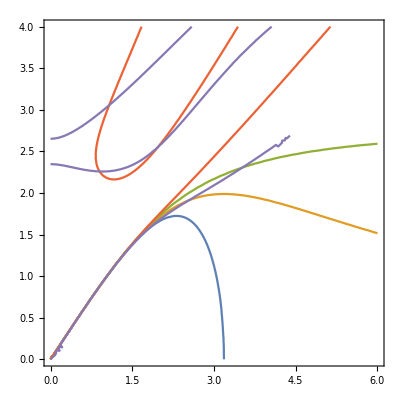

```mathematica
ContourPlot[{(Disp1/.{ν->1/3})==0,(Disp2/.{ν->1/3})==0,
(Disp3/.{ν->1/3})==0,(DispAll/.{ν->1/3})==0,
(Disp/.{ν->1/3})==0},{k,0,6},{ω,0,4}]
```

#### Exact elimination of V1

```mathematica
ClearAll[U2,V3,U4]
```

```mathematica
ClearAll[λ,μ,s]
```

```mathematica
a0=2 (λ+μ);
a1=4 l+2 m+3 (λ+μ);
a2=4 l-2 m+n+λ;
a3=λ/4;
a4=2 s^2 (2 λ+3 μ) ρ/(8 (λ+2 μ));
a5=(2 l+λ)/2;
a6=-s^2 ρ(λ+3 μ)/(8 (λ+2 μ));
a7=(λ+3 μ)/8;

b1=a2/2;
b2=2a5;
b3=-(3 λ^2+8 λ μ+4 μ^2)/(8(λ+2μ));
b4=s^2 (λ^2+4 λ μ+2 μ^2) ρ/(8μ(λ+2μ));
b5=s^2 ρ/2;
b6=(λ+2 μ)/2;
b7=(2 l+4 m+3 λ+6 μ)/4;
b8=-s^4 ρ^2/(16μ);
b9=s^2 ρ(λ^2+7λ μ+8 μ^2)/(16 μ (λ+2 μ));
b10=-(3 λ^2+10λ μ+8 μ^2)/(16(λ+2μ));
```

```mathematica
(* left linear *)
L10[V_,x_,t_]:=a0 V[x,t]+δ^2(a3 D[V[x,t], x,x]+a4 D[V[x,t], t,t]);
L10arg[V_,x_,t_]:=a0 V+δ^2(a3 D[V, x,x]+a4 D[V, t,t]);
L20[V_,x_,t_]:=D[(λ V[x,t]+δ^2(b3 D[V[x,t], x,x]+b4 D[V[x,t], t,t])), x];
L20arg[V_,x_,t_]:=D[(λ V+δ^2(b3 D[V, x,x]+b4 D[V, t,t])), x];
(* left nonlinear *)
L11[V_,x_,t_]:=ε(a1 V[x,t]^2+a2 V[x,t]D[U0[x,t], x]);
L11arg[V_,x_,t_]:=ε(a1(V)^2+a2 (V) D[U0[x,t], x]);
L21[V_,x_,t_]:=ε D[(b1 V[x,t]^2+b2 V[x,t]D[U0[x,t], x]), x];
L21arg[V_,x_,t_]:=ε D[(b1 (V)^2+b2 (V)D[U0[x,t], x]), x];
(* right *)
M1[x,t]=Ε S[x,t]-λ D[U0[x,t], x]-ε a5 (D[U0[x,t], x])^2-δ^2(a6 D[U0[x,t], x,t,t]+a7 D[U0[x,t], x,x,x]);
M2[x,t]=-Ε T[x,t]+b5 D[U0[x,t], t,t]-b6 D[U0[x,t], x,x]-ε b7 D[((D[U0[x,t], x])^2), x]-δ^2(b8 D[U0[x,t], t,t,t,t]+b9 D[U0[x,t], x,x,t,t]+b10 D[U0[x,t], x,x,x,x]);
```

```mathematica
L10[V1,x,t]+L11[V1,x,t]-M1[x,t]-ndPrrFin/.r->δ//Simplify
L20[V1,x,t]+L21[V1,x,t]-M2[x,t]+ndPxrFin/.r->δ//Simplify
```

0

0

```mathematica
-Series[(L20arg[M1[x,t],x,t]-L10arg[M2[x,t],x,t])/(μ (3 λ+2 μ)),{δ,0,3},{ε,0,0}]//Simplify
```

(-1/(μ (3 λ+2 μ))(2 Ε (λ+μ) T[x,t]-s^2 (λ+μ) ρ U0^(0,2)[x,t]+Ε λ S^(1,0)[x,t]+3 λ μ U0^(2,0)[x,t]+2 μ^2 U0^(2,0)[x,t])+O[ε]^1)+(-((2 s^2 Ε μ (2 λ+3 μ) ρ T^(0,2)[x,t]-s^4 (λ^2+5 λ μ+5 μ^2) ρ^2 U0^(0,4)[x,t]+s^2 Ε λ^2 ρ S^(1,2)[x,t]+4 s^2 Ε λ μ ρ S^(1,2)[x,t]+2 s^2 Ε μ^2 ρ S^(1,2)[x,t]+2 Ε λ^2 μ T^(2,0)[x,t]+4 Ε λ μ^2 T^(2,0)[x,t]+6 s^2 λ^2 μ ρ U0^(2,2)[x,t]+21 s^2 λ μ^2 ρ U0^(2,2)[x,t]+14 s^2 μ^3 ρ U0^(2,2)[x,t]-3 Ε λ^2 μ S^(3,0)[x,t]-8 Ε λ μ^2 S^(3,0)[x,t]-4 Ε μ^3 S^(3,0)[x,t]-6 λ^2 μ^2 U0^(4,0)[x,t]-16 λ μ^3 U0^(4,0)[x,t]-8 μ^4 U0^(4,0)[x,t])/(8 (μ^2 (λ+2 μ) (3 λ+2 μ))))+O[ε]^1) δ^2+O[δ]^4

```mathematica
(3 λ+2 μ)(λ+2μ)//Expand
```

3 λ^2+8 λ μ+4 μ^2

Dispersion terms match Bostrom’s!

```mathematica
s=Sqrt[μ(3λ+2μ)/((λ+μ)ρ)];
```

```mathematica
ClearAll[s]
```

```mathematica
cl=CoefficientList[(L20arg[L10[V1,x,t]+L11[V1,x,t],x,t]-L10arg[L20[V1,x,t]+L21[V1,x,t],x,t]-(L20arg[M1[x,t],x,t]-L10arg[M2[x,t],x,t]))/(λ+μ),{ε,δ}];
Series[cl⟦1+0,1+0⟧+ε cl⟦1+1,1+0⟧+δ^2 cl⟦1+0,1+2⟧(*/(μ (3 λ+2 μ))*),{δ,0,3},{ε,0,1}]/.ForPrint/.ForPrint2/.ForLatex//Simplify
```

((s^2 ρ U_(0,t,t)-(λ+2 μ) U_(0,x,x)+(λ (-Ε S_x+λ U_(0,x,x)))/(λ+μ)-2 Ε T[x,t])+1/(2 (λ+μ)^3)(Ε S[x,t] (Ε (-n (λ+μ)+2 m (2 λ+μ)+2 (λ^2-2 l μ+λ μ)) S_x-(3 λ^3+5 λ^2 μ+4 l μ^2+2 λ μ^2-2 n λ (λ+μ)+2 m λ (3 λ+2 μ)) U_(0,x,x))-U_(0,x) (Ε (3 λ^3+5 λ^2 μ+4 l μ^2+2 λ μ^2-2 n λ (λ+μ)+2 m λ (3 λ+2 μ)) S_x+(3 n λ^2 (λ+μ)+2 μ (9 λ^3+24 λ^2 μ+21 λ μ^2+m (3 λ+2 μ)^2+2 μ^2 (l+3 μ))) U_(0,x,x))) ε+O[ε]^2)+1/(8 μ (λ+μ) (λ+2 μ))(-2 s^2 Ε μ (2 λ+3 μ) ρ T_(t,t)-2 Ε λ μ (λ+2 μ) T_(x,x)-s^2 Ε λ^2 ρ S_(x,t,t)-4 s^2 Ε λ μ ρ S_(x,t,t)-2 s^2 Ε μ^2 ρ S_(x,t,t)+3 Ε λ^2 μ S_(x,x,x)+8 Ε λ μ^2 S_(x,x,x)+4 Ε μ^3 S_(x,x,x)+s^4 λ^2 ρ^2 U_(0,t,t,t,t)+5 s^4 λ μ ρ^2 U_(0,t,t,t,t)+5 s^4 μ^2 ρ^2 U_(0,t,t,t,t)-6 s^2 λ^2 μ ρ U_(0,x,x,t,t)-21 s^2 λ μ^2 ρ U_(0,x,x,t,t)-14 s^2 μ^3 ρ U_(0,x,x,t,t)+6 λ^2 μ^2 U_(0,x,x,x,x)+16 λ μ^3 U_(0,x,x,x,x)+8 μ^4 U_(0,x,x,x,x)) δ^2+O[δ]^4

```mathematica
(-s^2 λ^2 ρ Subscript[S, x,t,t]-4 s^2 λ μ ρ Subscript[S, x,t,t]-2 s^2 μ^2 ρ Subscript[S, x,t,t]+3 λ^2 μ Subscript[S, x,x,x]+8 λ μ^2 Subscript[S, x,x,x]+4 μ^3 Subscript[S, x,x,x]+s^4 λ^2 ρ^2 Subscript[U, 0,t,t,t,t]+5 s^4 λ μ ρ^2 Subscript[U, 0,t,t,t,t]+5 s^4 μ^2 ρ^2 Subscript[U, 0,t,t,t,t]-6 s^2 λ^2 μ ρ Subscript[U, 0,x,x,t,t]-21 s^2 λ μ^2 ρ Subscript[U, 0,x,x,t,t]-14 s^2 μ^3 ρ Subscript[U, 0,x,x,t,t]+6 λ^2 μ^2 Subscript[U, 0,x,x,x,x]+16 λ μ^3 Subscript[U, 0,x,x,x,x]+8 μ^4 Subscript[U, 0,x,x,x,x])//FullSimplify
```

-s^2 (λ^2+4 λ μ+2 μ^2) ρ S_(x,t,t)+μ (λ+2 μ) (3 λ+2 μ) S_(x,x,x)+s^2 ρ (s^2 (λ^2+5 λ μ+5 μ^2) ρ U_(0,t,t,t,t)-μ (6 λ^2+21 λ μ+14 μ^2) U_(0,x,x,t,t))+2 μ^2 (λ+2 μ) (3 λ+2 μ) U_(0,x,x,x,x)

```mathematica
λ=(Ε ν)/((1+ν)(1-2ν));
μ=Ε/(2(1+ν));
```

```mathematica
(Coefficient[(L20arg[L11[V1,x,t],x,t]-L10arg[L21[V1,x,t],x,t])δ-(L20arg[M1[x,t],x,t]-L10arg[M2[x,t],x,t])δ,ε δ])2(λ+μ)/(μ(3λ+2μ))//FullSimplify
```

((3 Ε+6 n ν^2-4 m (1+ν)^2 (-1+2 ν)-2 l (-1+2 ν)^3) U0^(1,0)[x,t] U0^(2,0)[x,t])/(-1+ν+2 ν^2)

```mathematica
V1[x_,t_]=(S[x,t]-λ D[U0[x,t], x])/(2(λ+μ));
```

```mathematica
(*-2(-1+ν+2 ν^2)/Ε^2*)1/Ε Series[cl⟦1+0,1+0⟧+ε cl⟦1+1,1+0⟧+δ^2 cl⟦1+0,1+2⟧,{δ,0,3},{ε,0,1}]/.ForPrint/.ForPrint2//Simplify
```

((-2 ν S_x+U_0_tt-U_0_xx-2 T[x,t])+1/Ε(U_0_x (2 (1+ν) (2 l (-1+2 ν)^3+ν (2 n-Ε-4 n ν+4 m (-1+ν+2 ν^2))) S_x+(4 m (1+ν)^2 (-1+2 ν)+2 l (-1+2 ν)^3-3 (Ε+2 n ν^2)) U_0_xx)+2 (1+ν) S[x,t] ((-1+2 ν) (n-n ν-2 Ε ν-2 n ν^2+4 l (1-3 ν+4 ν^3)+m (-2-2 ν+8 ν^2+8 ν^3)) S_x+(2 l (-1+2 ν)^3+ν (2 n-Ε-4 n ν+4 m (-1+ν+2 ν^2))) U_0_xx)) ε+O[ε]^2)+1/(8 (-1+ν))((2+2 ν-4 ν^2-4 ν^3) S_xtt+2 (-1+ν^2) S_xxx+6 T_tt-10 ν T_tt-8 ν^2 T_tt+8 ν^3 T_tt+4 ν T_xx-4 ν^2 T_xx-5 U_0_tttt+5 ν U_0_tttt+6 ν^2 U_0_tttt-4 ν^3 U_0_tttt+7 U_0_xxtt-7 ν U_0_xxtt-2 ν^2 U_0_xxtt-2 U_0_xxxx+2 ν U_0_xxxx) δ^2+O[δ]^4

```mathematica
6 Subscript[T, tt]-10 ν Subscript[T, tt]-8 ν^2 Subscript[T, tt]+8 ν^3 Subscript[T, tt]+4 ν Subscript[T, xx]-4 ν^2 Subscript[T, xx]-5 Ε Subscript[Subscript[U, 0], tttt]+5 Ε ν Subscript[Subscript[U, 0], tttt]+6 Ε ν^2 Subscript[Subscript[U, 0], tttt]-4 Ε ν^3 Subscript[Subscript[U, 0], tttt]+7 Ε Subscript[Subscript[U, 0], xxtt]-7 Ε ν Subscript[Subscript[U, 0], xxtt]-2 Ε ν^2 Subscript[Subscript[U, 0], xxtt]-2 Ε Subscript[Subscript[U, 0], xxxx]+2 Ε ν Subscript[Subscript[U, 0], xxxx]//Simplify
```

2 (3-5 ν-4 ν^2+4 ν^3) T_tt-4 (-1+ν) ν T_xx+Ε ((-5+5 ν+6 ν^2-4 ν^3) U_0_tttt+(7-7 ν-2 ν^2) U_0_xxtt+2 (-1+ν) U_0_xxxx)

```mathematica
Manipulate[(-(7-7 ν-2 ν^2)-Sqrt[(7-7 ν-2 ν^2)^2-4(-5+5 ν+6 ν^2-4 ν^3)2 (-1+ν)])/(2(-5+5 ν+6 ν^2-4 ν^3)),{ν,0,0.5}]
```

#### Final equations (dimensional)

```mathematica
InvScales={Derivative[i_,k_][U0][x_,t_]->(Derivative[i,k][U0][x,t])/(ε L)L^(i+k) s^-k,
U0[x,t]->U0[x,t]/(ε L),δ->R/L};
```

```mathematica
Eq=D[U0[x,t], t,t]-D[U0[x,t], x,x]+(ε (4 m (1+ν)^2 (-1+2 ν)+2 l (-1+2 ν)^3-3 (Ε+2 n ν^2)) D[U0[x,t], x] D[U0[x,t], x,x])/Ε+1/4 δ^2 ((1+ν) D[U0[x,t], t,t,t,t]-2 (1+ν+ν^2) D[U0[x,t], t,t,x,x]+(1+ν)D[U0[x,t], x,x,x,x]);
EqReg=D[U0[x,t], t,t]-D[U0[x,t], x,x]+(ε (4 m (1+ν)^2 (-1+2 ν)+2 l (-1+2 ν)^3-3 (Ε+2 n ν^2)) D[U0[x,t], x] D[U0[x,t], x,x])/Ε-ν^2/2 δ^2 ( D[U0[x,t], t,t,x,x]);
```

```mathematica
λ=(Ε ν)/((1+ν)(1-2ν));
μ=Ε/(2(1+ν));
ε Ε EqReg/L/ρ/.InvScales/.ForPrint//Simplify
```

U_tt-((Ε+(-4 m (1+ν)^2 (-1+2 ν)-2 l (-1+2 ν)^3+3 (Ε+2 n ν^2)) U_x) U_xx)/ρ-1/2 R^2 ν^2 U_xxtt

```mathematica
s^2 ε ρ Eq/L/ρ/.InvScales/.ForPrint//Simplify
```

U_tt-(s^2 (Ε+(-4 m (1+ν)^2 (-1+2 ν)-2 l (-1+2 ν)^3+3 (Ε+2 n ν^2)) U_x) U_xx)/Ε+(R^2 ((1+ν) U_tttt-2 s^2 (1+ν+ν^2) U_xxtt+s^4 (1+ν) U_xxxx))/(4 s^2)

#### Soliton analysis

```mathematica
EqTempl=D[u[x,t], t,t]-c^2 D[u[x,t], x,x]-β/(2ρ) D[u[x,t]^2,x,x]+(a/c^2 D[u[x,t], t,t,t,t]+b D[u[x,t], t,t,x,x]+d c^2 D[u[x,t], x,x,x,x])R^2;
```

```mathematica
u[x_,t_]=A Cosh[(x-v t)B]^-2;
```

```mathematica
EqTempl//Simplify
```

1/(2 c^2 ρ)A B^2 (3 (4 A c^2 β+(c^4 (1+44 B^2 d R^2)+c^2 (-1+44 b B^2 R^2) v^2+44 a B^2 R^2 v^4) ρ)-2 (4 A c^2 β+(c^4 (-1+52 B^2 d R^2)+c^2 (1+52 b B^2 R^2) v^2+52 a B^2 R^2 v^4) ρ) Cosh[2 B (-t v+x)]+(c^4 (-1+4 B^2 d R^2)+c^2 (1+4 b B^2 R^2) v^2+4 a B^2 R^2 v^4) ρ Cosh[4 B (-t v+x)]) Sech[B (-t v+x)]^6

```mathematica
Solve[4 A c^2 β+(c^4 (1+44 B^2 d R^2)+c^2 (-1+44 b B^2 R^2) v^2+44 a B^2 R^2 v^4) ρ==0&&4 A c^2 β+(c^4 (-1+52 B^2 d R^2)+c^2 (1+52 b B^2 R^2) v^2+52 a B^2 R^2 v^4) ρ==0&&c^4 (-1+4 B^2 d R^2)+c^2 (1+4 b B^2 R^2) v^2+4 a B^2 R^2 v^4==0,{v,B}]//Simplify
```

{{v→-(√(A β+3 c^2 ρ))/(√3 √ρ),B→-(√3 √A c √β √ρ)/(2 √(-R^2 (a (A β+3 c^2 ρ)^2+3 c^2 ρ (A b β+3 c^2 (b+d) ρ))))},{v→-(√(A β+3 c^2 ρ))/(√3 √ρ),B→(√3 √A c √β √ρ)/(2 √(-R^2 (a (A β+3 c^2 ρ)^2+3 c^2 ρ (A b β+3 c^2 (b+d) ρ))))},{v→(√(A β+3 c^2 ρ))/(√3 √ρ),B→-(√3 √A c √β √ρ)/(2 √(-R^2 (a (A β+3 c^2 ρ)^2+3 c^2 ρ (A b β+3 c^2 (b+d) ρ))))},{v→(√(A β+3 c^2 ρ))/(√3 √ρ),B→(√3 √A c √β √ρ)/(2 √(-R^2 (a (A β+3 c^2 ρ)^2+3 c^2 ρ (A b β+3 c^2 (b+d) ρ))))}}

```mathematica
Solve[4 A c^2 β+(c^4 (1+44 B^2 d R^2)+c^2 (-1+44 b B^2 R^2) v^2+44 a B^2 R^2 v^4) ρ==0&&4 A c^2 β+(c^4 (-1+52 B^2 d R^2)+c^2 (1+52 b B^2 R^2) v^2+52 a B^2 R^2 v^4) ρ==0&&c^4 (-1+4 B^2 d R^2)+c^2 (1+4 b B^2 R^2) v^2+4 a B^2 R^2 v^4==0,{A,B}]//Simplify
```

{{A→(3 (-c^2+v^2) ρ)/β,B→-(c √(c^2-v^2))/(2 √(R^2 (c^4 d+b c^2 v^2+a v^4)))},{A→(3 (-c^2+v^2) ρ)/β,B→(c √(c^2-v^2))/(2 √(R^2 (c^4 d+b c^2 v^2+a v^4)))}}

```mathematica
Solve[c^4 d+b c^2 v2+a v2^2==0,v2]
```

{{v2→(-b c^2-√(b^2 c^4-4 a c^4 d))/(2 a)},{v2→(-b c^2+√(b^2 c^4-4 a c^4 d))/(2 a)}}

```mathematica
EqTemplDimless=D[u[x,t], t,t]-D[u[x,t], x,x]-ε β/(2Ε) D[u[x,t]^2,x,x]+δ^2(a D[u[x,t], t,t,t,t]+b D[u[x,t], t,t,x,x]+d D[u[x,t], x,x,x,x]);
```

```mathematica
u[x_,t_]=A Cosh[(x-v t)B]^-2;
```

```mathematica
EqTemplDimless//Simplify
```

1/(2 Ε)A B^2 (3 (4 A β ε+(1+44 B^2 d δ^2+44 a B^2 v^4 δ^2+v^2 (-1+44 b B^2 δ^2)) Ε)-2 (4 A β ε+(-1+v^2+52 B^2 d δ^2+52 b B^2 v^2 δ^2+52 a B^2 v^4 δ^2) Ε) Cosh[2 B (-t v+x)]+(-1+4 B^2 d δ^2+4 a B^2 v^4 δ^2+v^2 (1+4 b B^2 δ^2)) Ε Cosh[4 B (-t v+x)]) Sech[B (-t v+x)]^6

```mathematica
Solve[4 A β ε+(1+44 B^2 d δ^2+44 a B^2 v^4 δ^2+v^2 (-1+44 b B^2 δ^2)) Ε==0&&4 A β ε+(-1+v^2+52 B^2 d δ^2+52 b B^2 v^2 δ^2+52 a B^2 v^4 δ^2) Ε==0&&-1+4 B^2 d δ^2+4 a B^2 v^4 δ^2+v^2 (1+4 b B^2 δ^2)==0,{v,B}]//Simplify
```

{{v→-(√(A β ε+3 Ε))/(√3 √Ε),B→-((√3 √A √β √ε √Ε)/(2 √(-δ^2 (a (A β ε+3 Ε)^2+3 Ε (A b β ε+3 (b+d) Ε)))))},{v→-(√(A β ε+3 Ε))/(√3 √Ε),B→(√3 √A √β √ε √Ε)/(2 √(-δ^2 (a (A β ε+3 Ε)^2+3 Ε (A b β ε+3 (b+d) Ε))))},{v→(√(A β ε+3 Ε))/(√3 √Ε),B→-((√3 √A √β √ε √Ε)/(2 √(-δ^2 (a (A β ε+3 Ε)^2+3 Ε (A b β ε+3 (b+d) Ε)))))},{v→(√(A β ε+3 Ε))/(√3 √Ε),B→(√3 √A √β √ε √Ε)/(2 √(-δ^2 (a (A β ε+3 Ε)^2+3 Ε (A b β ε+3 (b+d) Ε))))}}

```mathematica
u[x_,t_]=A Cosh[(x-v t)B]^-2;
D[u[x,t],t]//Simplify
D[u[x,t],t,t]//Simplify
D[u[x,t],t,t,t]//Simplify
```

2 A B v Sech[B (-t v+x)]^2 Tanh[B (-t v+x)]

2 A B^2 v^2 (-2+Cosh[2 B (-t v+x)]) Sech[B (-t v+x)]^4

4 A B^3 v^3 (-5+Cosh[2 B (-t v+x)]) Sech[B (-t v+x)]^4 Tanh[B (-t v+x)]

```mathematica
(* PS *)
 ρ=1060; Ε=3.7*10^9; ν=0.34;
l =-18.9*10^9; m= -13.3*10^9; n=-10*10^9;
```

```mathematica
(* PMMA *)
ρ=1180; Ε=4.9*10^9; ν=0.34;
l =-10.93*10^9; m= -7.73*10^9; n=-1.41*10^9;
```

```mathematica
β=3Ε+2l(1-2 ν)^3+4 m (1+ν)^2 (1-2ν) + 6 n ν^2
c=Sqrt[Ε/ρ];
```

-2.76429×10^10

```mathematica
R=0.01;
```

```mathematica
B[A_,a_,b_,d_]=Sqrt[(3A β c^2 ρ)/(-4 R^2 (a (A β+3 c^2 ρ)^2+3 c^2 ρ (A b β+3 c^2 (b+d) ρ)))];
V=Sqrt[(A β+3 c^2 ρ)/(3ρ)];
```

```mathematica
u1[A_] =  A (Cosh [B[A,(1+ν)/4,(-1-ν-ν^2)/2,(1+ν)/4] x])^-2;
u12[A_]=A (Cosh [B[A, (5-5ν-6 ν^2+4 ν^3)/(8(1-ν)),(-7+7ν+2 ν^2)/(8(1-ν)),1/4]x])^-2;
```

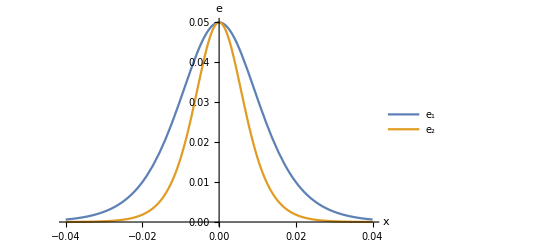

```mathematica
Amp=-0.05;
fig=Plot[{-u1[Amp], -u12[Amp]}, {x, -0.04, 0.04}, AxesLabel->{x,e}, PlotLegends->{"e_1","e_2"}(*TicksStyle->Medium*)]
```

```mathematica
Manipulate[Plot[{u1[A], u12[A]}, {x, -0.04, 0.04}, AxesLabel->{x,e},PlotRange->{0,.5}, PlotLegends->{"e_1","e_2"}],{A,0.1,0.5}]
```

```mathematica
(* Upper velocity limit *)
α11=(1+ν)/4;α21=(-1-ν-ν^2)/2;α31=α11;
α12=(5-5ν-6 ν^2+4 ν^3)/(8(1-ν));α22=-(7-7ν-2 ν^2)/(8(1-ν));α32=1/4;
c=Sqrt[Ε/ρ];
v[a_,b_,d_]=Sqrt[(-b +√(b^2-4 a d))/(2 a)c^2];
β=3Ε+2l(1-2 ν)^3+4 m (1+ν)^2 (1-2ν) + 6 n ν^2;
```

```mathematica
(* PS *)
 ρ=1060; Ε=3.7*10^9; ν=0.34;
l =-18.9*10^9; m= -13.3*10^9; n=-10*10^9;
```

```mathematica
v[α11,α21,α31]^2/c^2-1
v[α12,α22,α32]^2/c^2-1
```

0.510509

0.184995

```mathematica
(3 (-c^2+v[α11,α21,α31]^2) ρ)/β//FullSimplify
(3 (-c^2+v[α12,α22,α32]^2) ρ)/β//FullSimplify
```

-0.204994

-0.0742847

### 2nd Method: multiscale expansion

```mathematica
USeries[x_,r_,t_]=U0[x,r,t](*+U1[x,r,t]δ*)+U2[x,r,t] δ^2(*+U3[x,r,t] δ^3*)+U4[x,r,t] δ^4;
VSeries[x_,r_,t_]=V0[x,r,t]+V1[x,r,t]δ(*+V2[x,r,t] δ^2*)+V3[x,r,t] δ^3(*+V4[x,r,t] δ^4*)+V5[x,r,t] δ^5;
```

```mathematica
V0[x_,r_,t_]=CV0[x,t]r+ε FV0[x,r,t];
```

```mathematica
U0[x_,r_,t_]=U0[x,t]+ε FU0[x,r,t];
```

```mathematica
CV0[x_,t_]=0;
FV0[x_,r_,t_]=0;
FU0[x_,r_,t_]=0;
```

```mathematica
V1[x_,r_,t_]=CV1[x,t]r+ε FV1[x,r,t];
(* CV1[x_,t_]=(μ(3λ+2μ)S[x,t]-λ(λ+μ)∂_x U0[x,t])/(2(λ+μ)^2) *)
(*FV1[x_,r_,t_]=CFV1[x,t]r;*)
(*CFV1[x_,t_]=1/(8 (λ+μ)^5)(-μ^2 (3 λ+2 μ)^2 (4 l+2 m+3 (λ+μ)) S[x,t]^2+2 μ (3 λ^2+5 λ μ+2 μ^2) (-n (λ+μ)+2 m (2 λ+μ)+2 (λ^2-2 l μ+λ μ)) S[x,t]∂_x U0[x,t]-(λ+μ)^2 (3 λ^3+5 λ^2 μ+4 l μ^2+2 λ μ^2-2 n λ (λ+μ)+2 m λ (3 λ+2 μ)) (∂_x U0[x,t])^2);*)
```

```mathematica
ClearAll[CFV1, FV1, V1];
```

```mathematica
ClearAll[U2];
```

```mathematica
U2[x_,r_,t_]=r^2/4(1/μ s^2 ρ D[U0[x,t], t,t]-2 D[U0[x,t], x,x]-(3 λ+2 μ)/(λ+μ)D[S[x,t], x])+ε FU2[x,r,t];
(*FU2[x_,r_,t_]=1/(16 μ^2 (λ+μ)^2)(-r^2 s^2 (λ+μ) (n λ+4 μ (m+2 (λ+μ))) ρ U0^(0,2)[x,t] U0^(1,0)[x,t]+n r^2 λ^2 S^(1,0)[x,t] U0^(1,0)[x,t]-8 m r^2 λ μ S^(1,0)[x,t] U0^(1,0)[x,t]+4 n r^2 λ μ S^(1,0)[x,t] U0^(1,0)[x,t]+2 r^2 λ^2 μ S^(1,0)[x,t] U0^(1,0)[x,t]-4 m r^2 μ^2 S^(1,0)[x,t] U0^(1,0)[x,t]+2 n r^2 μ^2 S^(1,0)[x,t] U0^(1,0)[x,t]+6 r^2 λ μ^2 S^(1,0)[x,t] U0^(1,0)[x,t]+4 r^2 μ^3 S^(1,0)[x,t] U0^(1,0)[x,t]-3 n r^2 λ^2 μ U0^(1,0)[x,t] U0^(2,0)[x,t]-12 m r^2 λ μ^2 U0^(1,0)[x,t] U0^(2,0)[x,t]-2 n r^2 λ μ^2 U0^(1,0)[x,t] U0^(2,0)[x,t]-12 r^2 λ^2 μ^2 U0^(1,0)[x,t] U0^(2,0)[x,t]-8 m r^2 μ^3 U0^(1,0)[x,t] U0^(2,0)[x,t]-20 r^2 λ μ^3 U0^(1,0)[x,t] U0^(2,0)[x,t]-8 r^2 μ^4 U0^(1,0)[x,t] U0^(2,0)[x,t]+r^2 S[x,t] (-(4 m-n) s^2 (λ+μ) ρ U0^(0,2)[x,t]+(4 m-n) (λ+2 μ) S^(1,0)[x,t]+μ (n λ-2 (λ^2-2 m μ+λ μ)) U0^(2,0)[x,t]));*)
```

```mathematica
n r^2 λ^2 Derivative[1,0][S][x,t] Derivative[1,0][U0][x,t]-8 m r^2 λ μ Derivative[1,0][S][x,t] Derivative[1,0][U0][x,t]+4 n r^2 λ μ Derivative[1,0][S][x,t] Derivative[1,0][U0][x,t]+2 r^2 λ^2 μ Derivative[1,0][S][x,t] Derivative[1,0][U0][x,t]-4 m r^2 μ^2 Derivative[1,0][S][x,t] Derivative[1,0][U0][x,t]+2 n r^2 μ^2 Derivative[1,0][S][x,t] Derivative[1,0][U0][x,t]+6 r^2 λ μ^2 Derivative[1,0][S][x,t] Derivative[1,0][U0][x,t]+4 r^2 μ^3 Derivative[1,0][S][x,t] Derivative[1,0][U0][x,t]//Simplify
```

r^2 (n (λ^2+4 λ μ+2 μ^2)+2 μ (λ^2+3 λ μ+2 μ^2-2 m (2 λ+μ))) S^(1,0)[x,t] U0^(1,0)[x,t]

```mathematica
c1[x_,t_]=1/(16 (λ+μ)^2 (λ+2 μ))(-2 s^2 λ ρ Derivative[0,2][S][x,t]-3 s^2 μ ρ Derivative[0,2][S][x,t]+3 s^2 λ^2 ρ Derivative[1,2][U0][x,t]+7 s^2 λ μ ρ Derivative[1,2][U0][x,t]+3 s^2 μ^2 ρ Derivative[1,2][U0][x,t]-λ^2 Derivative[2,0][S][x,t]-2 λ μ Derivative[2,0][S][x,t]-4 λ^2 μ Derivative[3,0][U0][x,t]-11 λ μ^2 Derivative[3,0][U0][x,t]-6 μ^3 Derivative[3,0][U0][x,t]);
V3[x_,r_,t_]=1/(16 μ (λ^2+3 λ μ+2 μ^2))(s^2 μ ρ Derivative[0,2][S][x,t]-s^2 λ^2 ρ Derivative[1,2][U0][x,t]-3 s^2 λ μ ρ Derivative[1,2][U0][x,t]-s^2 μ^2 ρ Derivative[1,2][U0][x,t]+λ^2 Derivative[2,0][S][x,t]+2 λ μ Derivative[2,0][S][x,t]+2 λ^2 μ Derivative[3,0][U0][x,t]+5 λ μ^2 Derivative[3,0][U0][x,t]+2 μ^3 Derivative[3,0][U0][x,t])r^3+c1[x,t]r+ε FV3[x,r,t];
```

```mathematica
U4[x_,r_,t_]=1/(64 μ^2 (λ+μ) (λ+2 μ))(r^4 s^4 (λ^2+3 λ μ+2 μ^2) ρ^2 Derivative[0,4][U0][x,t]-r^2 s^2 (-2 μ (2 λ+3 μ)+r^2 (λ^2+4 λ μ+3 μ^2)) ρ Derivative[1,2][S][x,t]+μ (-r^2 s^2 (3 (2+r^2) λ^2+2 (7+5 r^2) λ μ+(6+7 r^2) μ^2) ρ Derivative[2,2][U0][x,t]+(λ+2 μ) (2 r^2 (λ+r^2 λ+r^2 μ) Derivative[3,0][S][x,t]+r^2 μ ((8+3 r^2) λ+3 (2+r^2) μ) Derivative[4,0][U0][x,t])))+ε FU4[x,r,t];
```

```mathematica
ClearAll[V1,U2,V3,U4,c1];
```

```mathematica
1/(64 μ^2 (λ+μ) (λ+2 μ))(r^4 s^4 (λ^2+3 λ μ+2 μ^2) ρ^2 Derivative[0,4][U0][x,t]+μ (-r^2 s^2 (3 (2+r^2) λ^2+2 (7+5 r^2) λ μ+(6+7 r^2) μ^2) ρ Derivative[2,2][U0][x,t]+μ (λ+2 μ) (r^2 ((8+3 r^2) λ+3 (2+r^2) μ) Derivative[4,0][U0][x,t])))/.ForPrint/.ForPrint2/.ForLatex//Simplify
```

```mathematica
FU2[x,r,t]/.ForPrint/.ForPrint2
```

1/(16 μ^2 (λ+μ)^2)(n r^2 λ^2 S_x U_0_x-8 m r^2 λ μ S_x U_0_x+4 n r^2 λ μ S_x U_0_x+2 r^2 λ^2 μ S_x U_0_x-4 m r^2 μ^2 S_x U_0_x+2 n r^2 μ^2 S_x U_0_x+6 r^2 λ μ^2 S_x U_0_x+4 r^2 μ^3 S_x U_0_x-r^2 s^2 (λ+μ) (n λ+4 μ (m+2 (λ+μ))) ρ U_0_x U_0_tt-3 n r^2 λ^2 μ U_0_x U_0_xx-12 m r^2 λ μ^2 U_0_x U_0_xx-2 n r^2 λ μ^2 U_0_x U_0_xx-12 r^2 λ^2 μ^2 U_0_x U_0_xx-8 m r^2 μ^3 U_0_x U_0_xx-20 r^2 λ μ^3 U_0_x U_0_xx-8 r^2 μ^4 U_0_x U_0_xx+r^2 S[x,t] ((4 m-n) (λ+2 μ) S_x+(-4 m+n) s^2 (λ+μ) ρ U_0_tt+μ (n λ-2 (λ^2-2 m μ+λ μ)) U_0_xx))

```mathematica
V3[x,r,t]/.ForPrint/.ForPrint2/.ForLatex//FullSimplify
```

ε FV3[x,r,t]+1/(16 μ (λ+μ)^2 (λ+2 μ))r (s^2 μ ((-2+r^2) λ+(-3+r^2) μ) ρ S_(t,t)+λ (λ+2 μ) (-μ+r^2 (λ+μ)) S_(x,x)-s^2 (r^2 (λ+μ) (λ^2+3 λ μ+μ^2)-μ (3 λ^2+7 λ μ+3 μ^2)) ρ U_(0,x,t,t)+μ (λ+2 μ) (r^2 (λ+μ) (2 λ+μ)-μ (4 λ+3 μ)) U_(0,x,x,x))

```mathematica
r^2 (λ+μ) (λ^2+3 λ μ+μ^2)-μ (3 λ^2+7 λ μ+3 μ^2)-(λ+2μ)(r^2 (λ+μ) (2 λ+μ)-μ (4 λ+3 μ))//Simplify
```

-(λ+μ) (r^2 (λ+μ)^2-μ (λ+3 μ))

#### Equations

```mathematica
ClearAll[U4]
```

```mathematica
ClearAll[U,V];
divPK=RotateRight[Div[RotateLeft[P,{1,1}],{r,ϕ,x},"Cylindrical"],1];
ndEq1=(ρ D[U[x,r,t], t,t]-divPK⟦1⟧)L/ε/.Scales2;
ndEq2=(ρ D[V[x,r,t], t,t]-divPK⟦2⟧) L/ε/.Scales2;
ndEq1=Coefficient[ndEq1,ε,0]+Coefficient[ndEq1,ε,1]ε;
ndEq2=Coefficient[ndEq2,ε,0]+Coefficient[ndEq2,ε,1]ε;
U[x_,r_,t_]=USeries[x,r,t];
V[x_,r_,t_]=VSeries[x,r,t];
```

```mathematica
Coefficient[ndEq1,δ,-2]//Simplify
```

-1/(2 r)ε (FU0^(0,2,0)[x,r,t] (ε (2 m-n+2 λ) V1[x,r,t]+2 r (μ+ε (m+λ+2 μ) U0^(1,0)[x,t]+ε (m+λ+2 μ) V1^(0,1,0)[x,r,t]+m ε^2 FU0^(1,0,0)[x,r,t]+ε^2 λ FU0^(1,0,0)[x,r,t]+2 ε^2 μ FU0^(1,0,0)[x,r,t]))+FU0^(0,1,0)[x,r,t] (2 ε (m+λ+2 μ) U0^(1,0)[x,t]+ε (4 m-n+4 (λ+μ)) V1^(0,1,0)[x,r,t]+2 (μ+r ε (m+λ+2 μ) V1^(0,2,0)[x,r,t]+ε^2 (m+λ+2 μ) FU0^(1,0,0)[x,r,t]+2 m r ε^2 FU0^(1,1,0)[x,r,t]+2 r ε^2 λ FU0^(1,1,0)[x,r,t]+4 r ε^2 μ FU0^(1,1,0)[x,r,t])))

```mathematica
cl1=CoefficientList[ndEq1 δ,{ε,δ},{2,4}];
cl2=CoefficientList[ndEq2 δ,{ε,δ},{3,4}];
```

```mathematica
ndEq1red=cl1⟦1,1⟧+cl1⟦2,1⟧ε+cl1⟦1,2⟧δ+cl1⟦1,3⟧δ^2;
CoefficientList[ndEq1red,{ε,δ},{2,4}]/.ForPrint/.ForPrint2/.ForLatex//Simplify
```

{{0,(-μ U_(2,r)-(λ+μ) V_(1,x)+r (s^2 ρ U_(0,t,t)-(λ+2 μ) U_(0,x,x)-μ U_(2,r,r)-λ V_(1,x,r)-μ V_(1,x,r)))/r,0,0},{0,0,0,0}}

```mathematica
ndEq2red=cl2⟦1,1⟧+cl2⟦2,1⟧ε+cl2⟦1,2⟧δ+cl2⟦1,3⟧δ^2;
CoefficientList[ndEq2red,{ε,δ},{2,4}]/.ForPrint/.ForPrint2/.ForLatex//Simplify
```

{{((λ+2 μ) (V_1-r (V_(1,r)+r V_(1,r,r))))/r^2,0,((λ+2 μ) V_3-r ((λ+2 μ) V_(3,r)+r ((λ+μ) U_(2,x,r)-s^2 ρ V_(1,t,t)+μ V_(1,x,x)+λ V_(3,r,r)+2 μ V_(3,r,r))))/r^2,0},{1/r^3((2 l+2 m+2 λ+3 μ) V_1^2+r (2 l+λ) V_1 (U_(0,x)-r V_(1,r,r))-r^2 ((2 l+λ) U_(0,x) (V_(1,r)+r V_(1,r,r))+V_(1,r) ((2 l+2 m+2 λ+3 μ) V_(1,r)+r (2 l+4 m+3 λ+6 μ) V_(1,r,r)))),0,0,0}}

```mathematica
Coefficient[cl2⟦1+1,1+0⟧, Derivative[1,0][U0][x,t]]/.ForPrint/.ForPrint2/.ForLatex//Simplify
```

((2 l+λ) (V_1-r (V_(1,r)+r V_(1,r,r))))/r^2

```mathematica
Coefficient[cl2⟦1+1,1+0⟧, Derivative[1,0][U0][x,t],0]/.ForPrint/.ForPrint2/.ForLatex//Simplify
```

((2 l+2 m+2 λ+3 μ) V_1^2-r^2 (2 l+λ) V_1 V_(1,r,r)-r^2 V_(1,r) ((2 l+2 m+2 λ+3 μ) V_(1,r)+r (2 l+4 m+3 λ+6 μ) V_(1,r,r)))/r^3

```mathematica
Solve[-128 r^2 μ^2 (λ^2+3 λ μ+2 μ^2) c2[x,t]-32 μ^2 (λ^2+3 λ μ+2 μ^2) c3[x,t]+2 r^2 s^4 λ^2 ρ^2 Derivative[0,4][U0][x,t]+6 r^2 s^4 λ μ ρ^2 Derivative[0,4][U0][x,t]+4 r^2 s^4 μ^2 ρ^2 Derivative[0,4][U0][x,t]-2 r^2 s^2 λ^2 ρ Derivative[1,2][S][x,t]+2 s^2 λ μ ρ Derivative[1,2][S][x,t]-8 r^2 s^2 λ μ ρ Derivative[1,2][S][x,t]+3 s^2 μ^2 ρ Derivative[1,2][S][x,t]-6 r^2 s^2 μ^2 ρ Derivative[1,2][S][x,t]-3 s^2 λ^2 μ ρ Derivative[2,2][U0][x,t]-6 r^2 s^2 λ^2 μ ρ Derivative[2,2][U0][x,t]-7 s^2 λ μ^2 ρ Derivative[2,2][U0][x,t]-20 r^2 s^2 λ μ^2 ρ Derivative[2,2][U0][x,t]-3 s^2 μ^3 ρ Derivative[2,2][U0][x,t]-14 r^2 s^2 μ^3 ρ Derivative[2,2][U0][x,t]+λ^2 μ Derivative[3,0][S][x,t]+4 r^2 λ^2 μ Derivative[3,0][S][x,t]+2 λ μ^2 Derivative[3,0][S][x,t]+12 r^2 λ μ^2 Derivative[3,0][S][x,t]+8 r^2 μ^3 Derivative[3,0][S][x,t]+4 λ^2 μ^2 Derivative[4,0][U0][x,t]+6 r^2 λ^2 μ^2 Derivative[4,0][U0][x,t]+11 λ μ^3 Derivative[4,0][U0][x,t]+18 r^2 λ μ^3 Derivative[4,0][U0][x,t]+6 μ^4 Derivative[4,0][U0][x,t]+12 r^2 μ^4 Derivative[4,0][U0][x,t]==0,c1]
```

{{c1→1/(16 (λ+μ)^2 (λ+2 μ))(-2 s^2 λ ρ S^(0,2)[x,t]-3 s^2 μ ρ S^(0,2)[x,t]+3 s^2 λ^2 ρ U0^(1,2)[x,t]+7 s^2 λ μ ρ U0^(1,2)[x,t]+3 s^2 μ^2 ρ U0^(1,2)[x,t]-λ^2 S^(2,0)[x,t]-2 λ μ S^(2,0)[x,t]-4 λ^2 μ U0^(3,0)[x,t]-11 λ μ^2 U0^(3,0)[x,t]-6 μ^3 U0^(3,0)[x,t])}}

```mathematica
DSolve[2 r^3 s^4 (λ^2+3 λ μ+2 μ^2) ρ^2 Derivative[0,4][U0][x,t]+r s^2 (μ (2 λ+3 μ)-2 r^2 (λ^2+4 λ μ+3 μ^2)) ρ Derivative[1,2][S][x,t]+μ (-r s^2 ((3+6 r^2) λ^2+(7+20 r^2) λ μ+(3+14 r^2) μ^2) ρ Derivative[2,2][U0][x,t]+(λ+2 μ) (r (λ+4 r^2 λ+4 r^2 μ) Derivative[3,0][S][x,t]+r μ (4 λ+6 r^2 λ+3 μ+6 r^2 μ) Derivative[4,0][U0][x,t]-8 μ (λ+μ) (f'[r]+r f''[r])))==0,f,r]
```

{{f→Function[{r},C[2]+1/(64 μ^2 (λ+μ) (λ+2 μ))(r^4 s^4 (λ^2+3 λ μ+2 μ^2) ρ^2 U0^(0,4)[x,t]-r^2 s^2 (-2 μ (2 λ+3 μ)+r^2 (λ^2+4 λ μ+3 μ^2)) ρ S^(1,2)[x,t]+μ (-r^2 s^2 (3 (2+r^2) λ^2+2 (7+5 r^2) λ μ+(6+7 r^2) μ^2) ρ U0^(2,2)[x,t]+(λ+2 μ) (64 μ (λ+μ) C[1] Log[r]+2 r^2 (λ+r^2 λ+r^2 μ) S^(3,0)[x,t]+r^2 μ ((8+3 r^2) λ+3 (2+r^2) μ) U0^(4,0)[x,t])))]}}

```mathematica
DSolve[-1/(4 r μ (λ+μ)^2)(r s^2 (λ+μ) (n λ+4 μ (m+2 (λ+μ))) ρ Derivative[0,2][U0][x,t] Derivative[1,0][U0][x,t]+μ (r (3 λ+2 μ) (n λ+4 μ (m+λ+μ)) Derivative[1,0][U0][x,t] Derivative[2,0][U0][x,t]+4 μ (λ+μ)^2 (f'[r]+r f''[r])))==0,f,r]//Simplify
```

{{f→Function[{r},C[2]+1/(16 μ^2 (λ+μ)^2)(-r^2 s^2 (λ+μ) (n λ+4 μ (m+2 (λ+μ))) ρ U0^(0,2)[x,t] U0^(1,0)[x,t]+μ (16 μ (λ+μ)^2 C[1] Log[r]-r^2 (3 λ+2 μ) (n λ+4 μ (m+λ+μ)) U0^(1,0)[x,t] U0^(2,0)[x,t]))]}}

#### Piola-Kirchhoff

```mathematica
ClearAll[U,V]
ndP=Coefficient[P/.Scales2,ε,1]+Coefficient[P/.Scales2,ε,2]ε;
U[x_,r_,t_]=USeries[x,r,t];
V[x_,r_,t_]=VSeries[x,r,t];
```

```mathematica
cl=CoefficientList[(ndP⟦2,2⟧-μ(3λ+2μ)/(λ+μ)S[x,t])δ δ /.r->1,{ε,δ},{2,3}];
cl/.ForPrint/.ForPrint2/.ForLatex//Simplify
```

{{0,0,-(μ (3 λ+2 μ) S[x,t])/(λ+μ)+λ V_1+λ U_(0,x)+λ V_(1,1)+2 μ V_(1,1)},{0,λ FV0[x,1,t]+(λ+2 μ) FV0_1,λ FU0_x+(l+λ/2) V_1^2+l U_(0,x)^2+1/2 λ U_(0,x)^2+2 l U_(0,x) V_(1,1)+λ U_(0,x) V_(1,1)+l V_(1,1)^2+2 m V_(1,1)^2+3/2 λ V_(1,1)^2+3 μ V_(1,1)^2+V_1 ((2 l-2 m+n) U_(0,x)+(2 l+λ) V_(1,1))}}

```mathematica
ClearAll[s,λ,μ]
```

```mathematica
(* here would be the equation *)
cl=CoefficientList[(ndP⟦1,2⟧/δ-μ(3λ+2μ)/(λ+μ)T[x,t])2δ δ δ/.r->1,{ε,δ},{2,4}];
cl/.ForPrint/.ForPrint2/.ForLatex//Simplify
```

{{0,0,0,2 μ (U_(2,1)+V_(1,x)-((3 λ+2 μ) T[x,t])/(λ+μ))},{0,2 μ FU0_1,2 μ FV0_x,V_1 ((2 m-n+2 λ) U_(2,1)+(2 m-n) V_(1,x))+2 (U_(0,x)+V_(1,1)) ((m+λ+2 μ) U_(2,1)+(m+μ) V_(1,x))}}

```mathematica
Solve[(16 (λ+μ)^2 (λ+2 μ) c1[x,t]-s^2 (3 λ^2+7 λ μ+3 μ^2) ρ Derivative[1,2][U0][x,t]+μ (4 λ^2+11 λ μ+6 μ^2) Derivative[3,0][U0][x,t])/(8 (λ+μ) (λ+2 μ))==0,c1[x,t]]//Simplify
```

{{c1[x,t]→(s^2 (3 λ^2+7 λ μ+3 μ^2) ρ U0^(1,2)[x,t]-μ (4 λ^2+11 λ μ+6 μ^2) U0^(3,0)[x,t])/(16 (λ+μ)^2 (λ+2 μ))}}

#### Final equation

```mathematica
λ=(Ε ν)/((1+ν)(1-2ν));
μ=Ε/(2(1+ν));
```

```mathematica
s=Sqrt[Ε/ρ];
```

```mathematica
cl=CoefficientList[(2ndP⟦2,1⟧/.r->1)/ε/δ/Ε,{ε,δ},{2,4}];
Series[cl⟦1,1⟧+cl⟦2,1⟧ε+cl⟦1,3⟧δ^2,{δ,0,2},{ε,0,1}]/.ForPrint/.ForPrint2//Simplify
```

((U_0_tt-U_0_xx)+((4 m (1+ν)^2 (-1+2 ν)+2 l (-1+2 ν)^3-3 (Ε+2 n ν^2)) U_0_x U_0_xx ε)/Ε+O[ε]^2)+1/4 ((1+ν) U_0_tttt-2 (1+ν+ν^2) U_0_xxtt+(1+ν) U_0_xxxx) δ^2+O[δ]^3

### 3rd Method: variational method (Lagrangian, incorrect)

```mathematica
ClearAll[U,V];
Lagr=r(ρ Total[(D[Displace, t])^2]/2-Pot);
VarSubst={
Derivative[i__][U][x__]-> (Derivative[i][U][x]+δ Derivative[i][δU][x]),
Derivative[i__][V][x__]-> (Derivative[i][V][x]+δ Derivative[i][δV][x]),
U[x__]->U[x]+δ δU[x],V[x__]->V[x]+δ δV[x]};
δLagr=Coefficient[(Lagr/.VarSubst)-Lagr,δ]//Simplify;
δLagr/.ForPrint/.ForPrint2
```

-1/(4 r^5)(-4 r^6 ρ (U_t δU_t+V_t δV_t)+2 r^2 (λ+2 μ) (2 r V+V^2+r^2 (U_r^2+2 U_x+U_x^2+2 V_r+V_r^2+V_x^2)) (r^2 (U_r δU_r+δU_x+U_x δU_x+(1+V_r) δV_r+V_x δV_x)+(r+V) δV[x,r,t])+(l+2 m) (2 r V+V^2+r^2 (U_r^2+2 U_x+U_x^2+2 V_r+V_r^2+V_x^2))^2 (r^2 (U_r δU_r+δU_x+U_x δU_x+(1+V_r) δV_r+V_x δV_x)+(r+V) δV[x,r,t])+n r^4 (-V (2 r+V) (U_r (1+U_x)+(1+V_r) V_x) ((1+U_x) δU_r+U_r δU_x+V_x δV_r+δV_x+V_r δV_x)+V (2 r+V) ((2 U_x+U_x^2+V_x^2) (U_r δU_r+(1+V_r) δV_r)+(U_r^2+V_r (2+V_r)) ((1+U_x) δU_x+V_x δV_x))-(r+V) (U_r (1+U_x)+(1+V_r) V_x)^2 δV[x,r,t]+(r+V) (U_r^2+V_r (2+V_r)) (2 U_x+U_x^2+V_x^2) δV[x,r,t])-4 r^4 μ (V (2 r+V) δV_r+2 r^2 V_r δV_r-r^2 (U_r^2+V_r^2) δV_r+2 r^2 U_x (U_r δU_r+V_r δV_r)-2 r^2 V_r (U_r δU_r+(1+V_r) δV_r)-r^2 (U_r (1+U_x)+(1+V_r) V_x) ((1+U_x) δU_r+U_r δU_x+V_x δV_r+δV_x+V_r δV_x)-2 r^2 U_x ((1+U_x) δU_x+V_x δV_x)+(2 r V+V^2+2 r^2 V_r) (U_r δU_r+δU_x+U_x δU_x+V_r δV_r+V_x δV_x)+r^2 ((U_x^2+V_x^2) (U_r δU_r+V_r δV_r)+(U_r^2+2 U_x+V_r^2) ((1+U_x) δU_x+V_x δV_x))+2 (r+V) V_r δV[x,r,t]+(U_r^2+2 U_x+U_x^2+V_r^2+V_x^2) (r^2 δV_r+(r+V) δV[x,r,t]))-2 m r^2 ((-2 r^2 U_r (1+U_x) (1+V_r) V_x+r^2 (2 U_x (2+U_x) V_r+U_x (2+U_x) V_r^2-V_x^2)+2 r V (2 U_x+U_x^2+2 V_r+V_r^2+V_x^2)+V^2 (2 U_x+U_x^2+2 V_r+V_r^2+V_x^2)+U_r^2 (2 r V+V^2+r^2 (-1+V_x^2))) (r^2 (U_r δU_r+δU_x+U_x δU_x+(1+V_r) δV_r+V_x δV_x)+(r+V) δV[x,r,t])+(2 r V+V^2+r^2 (U_r^2+2 U_x+U_x^2+2 V_r+V_r^2+V_x^2)) (V (2 r+V) δV_r+2 r^2 V_r δV_r-r^2 (U_r^2+V_r^2) δV_r+2 r^2 U_x (U_r δU_r+V_r δV_r)-2 r^2 V_r (U_r δU_r+(1+V_r) δV_r)-r^2 (U_r (1+U_x)+(1+V_r) V_x) ((1+U_x) δU_r+U_r δU_x+V_x δV_r+δV_x+V_r δV_x)-2 r^2 U_x ((1+U_x) δU_x+V_x δV_x)+(2 r V+V^2+2 r^2 V_r) (U_r δU_r+δU_x+U_x δU_x+V_r δV_r+V_x δV_x)+r^2 ((U_x^2+V_x^2) (U_r δU_r+V_r δV_r)+(U_r^2+2 U_x+V_r^2) ((1+U_x) δU_x+V_x δV_x))+2 (r+V) V_r δV[x,r,t]+(U_r^2+2 U_x+U_x^2+V_r^2+V_x^2) (r^2 δV_r+(r+V) δV[x,r,t]))))

```mathematica
CUt=Coefficient[δLagr,D[δU[x,r,t], t]];
CVt=Coefficient[δLagr,D[δV[x,r,t], t]];
CU=Coefficient[δLagr,δU[x,r,t]]//Simplify;
CV=Coefficient[δLagr,δV[x,r,t]]//Simplify;
CUx=Coefficient[δLagr,D[δU[x,r,t], x]]//Simplify;
CVr=Coefficient[δLagr,D[δV[x,r,t], r]]//Simplify;
CUr=Coefficient[δLagr,D[δU[x,r,t], r]]//Simplify;
CVx=Coefficient[δLagr,D[δV[x,r,t], x]]//Simplify;
```

#### Equations

```mathematica
USeries[x_,r_,t_]=U0[x,t]+U2[x,t] r^2(*δ^2*)+U4[x,t] r^4(*δ^4*);
VSeries[x_,r_,t_]=V1[x,t]r (*δ*)(*+V2[x,t] r^2 δ^2*)+V3[x,t] r^3(*δ^3*);
```

```mathematica
ClearAll[U,V]
Eq1=D[CUt, t]-CU+D[CUx, x]+D[CUr, r];
Eq2=D[CVt, t]-CV+D[CVx, x]+D[CVr, r];
ndEq1=(Eq1/.Scales2)/ε/r;
ndEq2=(Eq2/.Scales2)/ε/r/r;
U[x_,r_,t_]=USeries[x,r,t];
V[x_,r_,t_]=VSeries[x,r,t];
cl1=CoefficientList[ndEq1,{ε,r},{2,3}];
cl2=CoefficientList[ndEq2,{ε,r},{2,3}];
ndEq1Red=cl1⟦1,1⟧+cl1⟦2,1⟧ε+cl1⟦1,3⟧r^2;
ndEq2Red=cl2⟦1,1⟧+cl2⟦2,1⟧ε+cl2⟦1,3⟧r^2;
ndEq1Int=Integrate[ndEq1Red/δ,{r,0,δ}];
ndEq2Int=Integrate[ndEq2Red/δ,{r,0,δ}];
cl1=CoefficientList[ndEq1Int,{ε,δ},{2,3}];
cl2=CoefficientList[ndEq2Int,{ε,δ},{2,3}];
```

```mathematica
cl1//Simplify
cl2//Simplify
```

{{-4 μ U2[x,t]+s^2 ρ U0^(0,2)[x,t]-2 λ V1^(1,0)[x,t]-2 μ V1^(1,0)[x,t]-λ U0^(2,0)[x,t]-2 μ U0^(2,0)[x,t],0,-16 μ U4[x,t]+s^2 ρ U2^(0,2)[x,t]-4 λ V3^(1,0)[x,t]-4 μ V3^(1,0)[x,t]-λ U2^(2,0)[x,t]-2 μ U2^(2,0)[x,t]},{-2 U2[x,t] ((4 m-n+4 (λ+μ)) V1[x,t]+2 (m+λ+2 μ) U0^(1,0)[x,t])-V1[x,t] ((8 l+n+2 (λ+μ)) V1^(1,0)[x,t]+2 (2 l+λ) U0^(2,0)[x,t])-U0^(1,0)[x,t] (2 (2 l+m+λ+μ) V1^(1,0)[x,t]+(2 l+4 m+3 λ+6 μ) U0^(2,0)[x,t]),0,0}}

{{-8 (λ+2 μ) V3[x,t]+s^2 ρ V1^(0,2)[x,t]-2 λ U2^(1,0)[x,t]-2 μ U2^(1,0)[x,t]-μ V1^(2,0)[x,t],0,s^2 ρ V3^(0,2)[x,t]-4 (λ+μ) U4^(1,0)[x,t]-μ V3^(2,0)[x,t]},{-(4 m+n+4 (λ+3 μ)) U2[x,t]^2-16 l V3[x,t] U0^(1,0)[x,t]-8 λ V3[x,t] U0^(1,0)[x,t]-4 l U0^(1,0)[x,t] U2^(1,0)[x,t]-2 m U0^(1,0)[x,t] U2^(1,0)[x,t]-2 λ U0^(1,0)[x,t] U2^(1,0)[x,t]-2 μ U0^(1,0)[x,t] U2^(1,0)[x,t]-3 m (V1^(1,0)[x,t])^2+1/4 n (V1^(1,0)[x,t])^2-3 λ (V1^(1,0)[x,t])^2-5 μ (V1^(1,0)[x,t])^2-m V1^(1,0)[x,t] U0^(2,0)[x,t]-λ V1^(1,0)[x,t] U0^(2,0)[x,t]-2 μ V1^(1,0)[x,t] U0^(2,0)[x,t]-2 (m+μ) U2[x,t] (4 V1^(1,0)[x,t]+U0^(2,0)[x,t])-m U0^(1,0)[x,t] V1^(2,0)[x,t]-λ U0^(1,0)[x,t] V1^(2,0)[x,t]-2 μ U0^(1,0)[x,t] V1^(2,0)[x,t]-1/2 V1[x,t] (32 (2 l+2 m+2 λ+3 μ) V3[x,t]+2 (8 l+n+2 (λ+μ)) U2^(1,0)[x,t]+(4 m-n+4 (λ+μ)) V1^(2,0)[x,t]),0,0}}

```mathematica
ClearAll[V1,U2,V3,U4,FV3,FU2]
```

```mathematica
U4[x_,t_]=Solve[cl1⟦1,3⟧==0,U4[x,t]]⟦1,1,2⟧;
```

```mathematica
V3[x_,t_]=Solve[cl2⟦1,1⟧==0,V3[x,t]]⟦1,1,2⟧+ε FV3[x,t];
cl2=CoefficientList[ndEq2Int,{ε,δ},{2,3}];
FV3[x_,t_]=Solve[cl2⟦2,1⟧==0,FV3[x,t]]⟦1,1,2⟧;
```

```mathematica
U2[x_,t_]=Solve[cl1⟦1,1⟧==0,U2[x,t]]⟦1,1,2⟧+ε FU2[x,t];
cl1=CoefficientList[ndEq1Int,{ε,δ},{2,3}];
FU2[x_,t_]=Solve[cl1⟦2,1⟧==0,FU2[x,t]]⟦1,1,2⟧;
```

The terms above coincides with those derived by the 1st method

```mathematica
U2[x_,t_]=U2[x,t]//Simplify;
V3[x_,t_]=V3[x,t]//Simplify;
```

#### Boundary conditions

```mathematica
ClearAll[U,V,V1,f]
```

```mathematica
bound={r->δ};
```

```mathematica
ClearAll[U,V,V1,f]
bound={r->δ};
ndBC1=((-CUr/.Scales2/.bound)/ε/L/δ/δ-μ(3λ+2μ)/(λ+μ) T[x,t])//Simplify;
ndBC2=((-CVr/.Scales2/.bound)/ε/L/δ-μ(3λ+2μ)/(λ+μ) S[x,t])//Simplify;
U[x_,r_,t_]=USeries[x,r,t];
V[x_,r_,t_]=VSeries[x,r,t];
ndBC1Red=Coefficient[ndBC1,ε,0]+Coefficient[ndBC1,ε,1]ε;
ndBC2Red=Coefficient[ndBC2,ε,0]+Coefficient[ndBC2,ε,1]ε;
cl1=CoefficientList[2ndBC1Red,{ε,δ},{2,3}];
cl2=CoefficientList[ndBC2Red,{ε,δ},{2,3}];
ndBC1RedRed=cl1⟦1,1⟧+cl1⟦2,1⟧ε+cl1⟦1,3⟧δ^2;
ndBC2RedRed=cl2⟦1,1⟧+cl2⟦2,1⟧ε+cl2⟦1,3⟧δ^2;
```

```mathematica
ClearAll[V1,f,g]
```

```mathematica
V1[x_,t_]=((Solve[cl2⟦1,1⟧==0,V1[x,t]]⟦1,1,2⟧//Simplify)
+f[x,t] δ^2+g[x,t]ε);
cl2=CoefficientList[ndBC2RedRed,{ε,δ},{2,3}];
f[x_,t_]=Solve[cl2⟦1,3⟧==0,f[x,t]]⟦1,1,2⟧//Simplify;
cl2=CoefficientList[ndBC2RedRed,{ε,δ},{2,3}];
g[x_,t_]=Solve[cl2⟦2,1⟧==0,g[x,t]]⟦1,1,2⟧//Simplify;
V1[x,t]/.ForPrint/.ForPrint2
```

(μ (3 λ+2 μ) S[x,t]-λ (λ+μ) U_0_x)/(2 (λ+μ)^2)-1/(8 (λ+μ)^5)ε (μ^2 (3 λ+2 μ)^2 (4 l+2 m+3 (λ+μ)) S[x,t]^2-2 μ (3 λ^2+5 λ μ+2 μ^2) (-n (λ+μ)+2 m (2 λ+μ)+2 (λ^2-2 l μ+λ μ)) S[x,t] U_0_x+(λ+μ)^2 (3 λ^3+5 λ^2 μ+4 l μ^2+2 λ μ^2-2 n λ (λ+μ)+2 m λ (3 λ+2 μ)) (U_0)_x^2)-1/(16 (λ+μ)^3 (λ+2 μ))δ^2 (s^2 μ (6 λ^2+13 λ μ+6 μ^2) ρ S_tt-s^2 (3 λ^3+10 λ^2 μ+10 λ μ^2+3 μ^3) ρ U_0_xtt+μ (λ+2 μ) (λ (3 λ+2 μ) S_xx+(4 λ^2+7 λ μ+3 μ^2) U_0_xxx))

```mathematica
cl1=CoefficientList[-ndBC1RedRed,{ε,δ},{2,3}];
ndBC1RedRed=cl1⟦1,1⟧+cl1⟦2,1⟧ε+cl1⟦1,3⟧δ^2;
cl1=CoefficientList[ndBC1RedRed,{ε,δ},{2,3}]//Simplify
```

{{1/(λ+μ)^2(2 μ (3 λ^2+5 λ μ+2 μ^2) T[x,t]-s^2 (λ+μ)^2 ρ U0^(0,2)[x,t]+μ (3 λ+2 μ) (λ S^(1,0)[x,t]+(λ+μ) U0^(2,0)[x,t])),0,1/8 (-(s^4 ρ^2 U0^(0,4)[x,t])/μ+1/(λ+μ)^3(s^2 (3 λ^3+5 λ^2 μ+5 λ μ^2+2 μ^3) ρ S^(1,2)[x,t]+s^2 (7 λ^3+17 λ^2 μ+14 λ μ^2+4 μ^3) ρ U0^(2,2)[x,t]-μ (3 λ+2 μ) ((4 λ^2+5 λ μ+2 μ^2) S^(3,0)[x,t]+(3 λ^2+5 λ μ+2 μ^2) U0^(4,0)[x,t])))},{1/(2 (λ+μ)^5)(μ (3 λ+2 μ) S[x,t] (-μ (3 λ+2 μ) (-n (λ+μ)+2 m (2 λ+μ)+2 (λ^2-2 l μ+λ μ)) S^(1,0)[x,t]+(λ+μ) (3 λ^3+5 λ^2 μ+4 l μ^2+2 λ μ^2-2 n λ (λ+μ)+2 m λ (3 λ+2 μ)) U0^(2,0)[x,t])+(λ+μ) U0^(1,0)[x,t] (μ (3 λ+2 μ) (3 λ^3+5 λ^2 μ+4 l μ^2+2 λ μ^2-2 n λ (λ+μ)+2 m λ (3 λ+2 μ)) S^(1,0)[x,t]+(λ+μ) (3 n λ^2 (λ+μ)+2 μ (9 λ^3+24 λ^2 μ+21 λ μ^2+m (3 λ+2 μ)^2+2 μ^2 (l+3 μ))) U0^(2,0)[x,t])),0,0}}

```mathematica
s=Sqrt[μ(3λ+2μ)/(λ+μ)/ρ];
λ=Ε ν/(1+ν)/(1-2ν);
μ=Ε/(1+ν)/2;
cl1=cl1/Ε//FullSimplify;
```

```mathematica
cl1/.ForPrint
```

{{2 ν S_x-U0_tt+U0_xx+2 T[x,t],0,1/4 ((1+ν) (1-2 ν+4 ν^2) S_xtt-S_xxx-(1+ν) U0_tttt+2 U0_xxtt+ν (-(1+2 ν) S_xxx+2 (1+ν) U0_xxtt-U0_xxxx)-U0_xxxx)},{1/Ε(U0_x (-2 (1+ν) (2 l (-1+2 ν)^3+ν (2 n-Ε-4 n ν+4 m (-1+ν+2 ν^2))) S_x+(4 m+3 Ε-2 l (-1+2 ν)^3-2 ν^2 (-3 n+m (6+4 ν))) U0_xx)-2 (1+ν) S[x,t] ((-1+2 ν) (n+2 m (1+ν) (-1+2 ν) (1+2 ν)-ν (n+2 Ε+2 n ν)+4 l (1-3 ν+4 ν^3)) S_x+(2 l (-1+2 ν)^3+ν (2 n-Ε-4 n ν+4 m (-1+ν+2 ν^2))) U0_xx)),0,0}}

```mathematica
(* Dispersive coefficients *)
c1=Coefficient[cl1⟦1,3⟧, Derivative[0,4][U0][x,t]]
c2=Coefficient[cl1⟦1,3⟧, Derivative[2,2][U0][x,t]]//Simplify
c3=Coefficient[cl1⟦1,3⟧, Derivative[4,0][U0][x,t]]//Simplify
c1+c2+c3//Simplify
```

1/4 (-1-ν)

1/2 (1+ν+ν^2)

1/4 (-1-ν)

ν^2/2

```mathematica
(* Nonlinear coefficients *)
b1=Coefficient[cl1⟦2,1⟧, Derivative[1,0][U0][x,t]Derivative[2,0][U0][x,t]]//FullSimplify
```

(3 Ε+6 n ν^2-4 m (1+ν)^2 (-1+2 ν)-2 l (-1+2 ν)^3)/Ε

### Plot

#### PS constants

```mathematica
ρ=1060;
Ε=3.7*10^9;
ν=0.34;
l =-1.89*10^10;
m= -1.33*10^10;
n=-10^10;
```

#### PMMA constants

```mathematica
ρ=1180;
Ε=4.9*10^9;
ν=0.34;
l =-10.93*10^9;
m= -7.73*10^9;
n=-1.41*10^9;
```

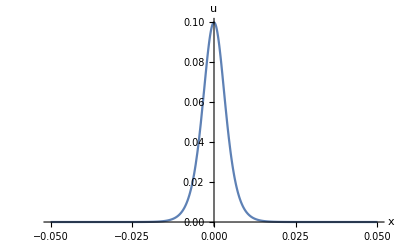

```mathematica
A=-0.1;
R=5*10^-3;
c=Sqrt[Ε/ρ];
β=3Ε+2l(1-2 ν)^3+4 m (1+ν)^2 (1-2ν) + 6 n ν^2;
d=β/(2ρ);
a=-((ν+1)R^2)/4;
b=(ν^2+ν+1)R^2/2;
u[x_,t_]=A Sech[(√(3/2) √(A d)c)/(√(b (9 c^4+6 A c^2 d)+2 a (9 c^4+6 A c^2 d+2 A^2 d^2)))(x-Sqrt[c^2+2/3 A d] t)]^2;
(*u0[x_,l_,m_,n_]=A Sech[Sqrt[(A d)/(6(a c^2+b+2/3 A d a))](x)]^2;*)
Plot[-u[x,0],{x,-0.05,0.05},PlotRange->All,AxesLabel->{x,u}]
```

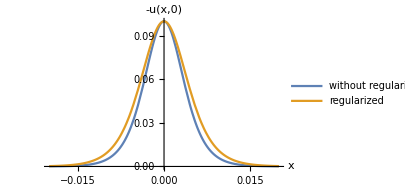

```mathematica
b=ν^2 R^2/2;
uReg[x_,t_]=A Sech[Sqrt[(A d)/(2b (3 c^2+2 A d))](x-Sqrt[c^2+2/3 A d] t)]^2;
fig=Plot[{-u[x,0],-uReg[x,0]},{x,-0.02,0.02},PlotRange->All,PlotLegends->Placed[{"without regularization", "regularized"},Bottom],PlotRange->All,AxesLabel->{x,"-u(x,0)"},ImageSize->300]
```

```mathematica
Export["reg_nonreg_compar.eps",fig]
Directory[]
```

reg_nonreg_compar.eps

/home/feodor

```mathematica
Directory[]
```

/home/theodor

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/theodor/Dropbox/Ioffe/Wolfram Mathematica code

### Dispersive relation

```mathematica
ClearAll[u,eq]
```

```mathematica
eq=D[u[x,t], t,t]-D[u[x,t], x,x]-1/2 δ^2(ν^2+ν+1)D[u[x,t], x,x,t,t]+1/4(1+ν)δ^2(D[u[x,t], t,t,t,t]+D[u[x,t], x,x,x,x]);
```

```mathematica
eq=D[u[x,t], t,t]-c^2 D[u[x,t], x,x]+R^2(b D[u[x,t], x,x,t,t]+a/c^2 D[u[x,t], t,t,t,t]+d c^2 D[u[x,t], x,x,x,x]);
```

```mathematica
u[x_,t_]=Exp[I(k/R x - ω c/R t)];
disp=eq/Exp[I(k/R x - ω c/R t)]//Simplify
```

(c^2 (k^2+d k^4-ω^2+b k^2 ω^2+a ω^4))/R^2

```mathematica
Solve[disp==0,ω]//Simplify
```

{{ω→-(√(-(-1+b k^2+√((-1+b k^2)^2-4 a (k^2+d k^4)))/a))/(√2)},{ω→(√(-(-1+b k^2+√((-1+b k^2)^2-4 a (k^2+d k^4)))/a))/(√2)},{ω→-(√((1-b k^2+√((-1+b k^2)^2-4 a (k^2+d k^4)))/a))/(√2)},{ω→(√((1-b k^2+√((-1+b k^2)^2-4 a (k^2+d k^4)))/a))/(√2)}}

```mathematica
Series[(2+δ^2 (1+ν+ν^2) ω^2-√(4+4 δ^2 ν^2 ω^2+δ^4 ν^2 (2+2 ν+ν^2) ω^4))/(δ^2 (1+ν)),{δ,0,2}]
```

ω^2-1/2 (ν^2 ω^4) δ^2+O[δ]^3

```mathematica
(2+δ^2 (1+ν+ν^2) ω^2)^2-(4+4 δ^2 ν^2 ω^2+δ^4 ν^2 (2+2 ν+ν^2) ω^4)//Simplify
```

δ^2 (1+ν) ω^2 (4+δ^2 (1+ν) ω^2)

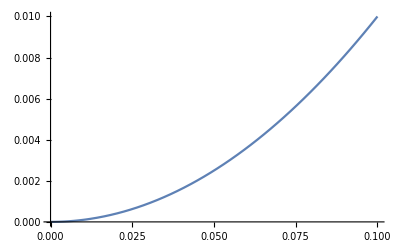

```mathematica
k2=(2+δ^2 (1+ν+ν^2) ω^2-√(4+4 δ^2 ν^2 ω^2+δ^4 ν^2 (2+2 ν+ν^2) ω^4))/(δ^2 (1+ν))/.{δ->0.5,ν->1/3};
Plot[k2,{ω,0,0.1}]
```

```mathematica
eqreg=D[u[x,t], t,t]-D[u[x,t], x,x]-1/2 δ^2 ν^2 D[u[x,t], x,x,t,t];
dispreg=eqreg/ⅇ^(k x-t ω)//Simplify
Solve[dispreg==0,k]//Simplify
```

ω^2-1/2 k^2 (2+δ^2 ν^2 ω^2)

{{k→-ω/(√(1+1/2 δ^2 ν^2 ω^2))},{k→ω/(√(1+1/2 δ^2 ν^2 ω^2))}}

### Plasticity

```mathematica
ndPred={
{ndPxxRed,ndPxrRed,0},
{ndPxrRed,ndPrrRed,0},
{0,0,0}
};
```

```mathematica
For[i=1,i<3,i++,
For[j=1,j<3,j++,
cl=CoefficientList[ndPred⟦i,j⟧,{ε,δ},{2,4}];
ndPred⟦i,j⟧=cl⟦1+0,1+0⟧+cl⟦1+1,1+0⟧ε+cl⟦1+0,1+2⟧δ^2;
];
];
Clear[i,j];
```

```mathematica
InvScales={Derivative[i_,k_][U0][x_,t_]->(Derivative[i,k][U0][x,t])/(ε L)L^(i+k) s^-k,
U0[x,t]->U0[x,t]/(ε L),δ->R/L,γ->γ/ε};
```

```mathematica
ClearAll[U0,ν,l,m,n,Ε,ρ,R,A]
```

```mathematica
(* Compute only once *)
ndPred⟦1,2⟧=δ ndPred⟦1,2⟧;
ndPred⟦2,1⟧=δ ndPred⟦2,1⟧;
ndPred=ε ndPred;
```

```mathematica
Pred=ndPred/.InvScales//Simplify;
```

```mathematica
VonMises[x_,r_,t_]=-3Inv2[Pred-IdentityMatrix[3]*Tr[Pred]/3]//Simplify;
```

```mathematica
λ=(Ε ν)/((1+ν)(1-2ν));μ=Ε/(2(1+ν));
β=3Ε+2l(1-2 ν)^3+4 m (1+ν)^2 (1-2ν) + 6 n ν^2;
```

```mathematica
s=Sqrt[(Ε+γ β)/ρ];
B[a_,b_,d_]=Sqrt[(3A β s^2 ρ)/(-4 R^2 (a (A β+3 s^2 ρ)^2+3 s^2 ρ (A b β+3 s^2 (b+d) ρ)))];
v=Sqrt[s^2+(A β)/(3ρ)];
```

```mathematica
u0[x_,t_]=(A-3γ) (Cosh [B[(1+ν)/4,(-1-ν-ν^2)/2,(1+ν)/4](x-v t)])^-2;
```

```mathematica
U0[x_,t_]=Integrate[u0[x,t],x];
```

```mathematica
R=0.01;
```

```mathematica
(* PS *)
 ρ=1060; Ε=3.7*10^9; ν=0.34;
l =-18.9*10^9; m= -13.3*10^9; n=-10*10^9;
```

```mathematica
(* PMMA *)
ρ=1180; Ε=4.9*10^9; ν=0.34;
l =-10.93*10^9; m= -7.73*10^9; n=-1.41*10^9;
```

```mathematica
VonMisesA[A_,γ_,x_,r_,t_]=VonMises[x,r,t];
```

```mathematica
Manipulate[{Sqrt[VonMisesA[A,γ,0,0,0]],A-3γ},{A,-0.1,0.3},{γ,-0.1,0.1}]
```

```mathematica
xarr=Array[#&,11,{-.2,.2}];
vmarr=Array[VonMises[xarr,#,0]&,5,{0,R}];
Max[vmarr]
```

2.51452×10^17

Soliton of extension is not elastic in PS rod.
PS yield stress: 86 MPa (extension),  114 MPa (compression).

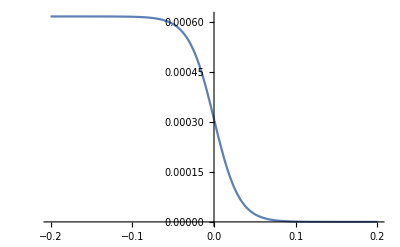

```mathematica
Plot[U0[x,0,0],{x,-.2,.2}]
```

```mathematica
(* Linear stress tensor *)
Displace0={U0[x,r,t],V01[x,r,t],0};
Deform0=RotateRight[Grad[RotateLeft[Displace0,1],{r,ϕ,x},"Cylindrical"],{1,1}];
SGr0=(Transpose[Deform0]+Deform0)/2;
P0=λ Inv1[SGr0]IdentityMatrix[3]+2μ SGr0//Simplify;
```

```mathematica
P0
```

{{-(3.7×10^7)/(1. Cosh[61425.3 t] Cosh[32.4757 x]-1. Sinh[61425.3 t] Sinh[32.4757 x])^2,-3.04883×10^8 r Sech[32.4757 (-1891.43 t+x)]^2 Tanh[32.4757 (-1891.43 t+x)],0.},{-3.04883×10^8 r Sech[32.4757 (-1891.43 t+x)]^2 Tanh[32.4757 (-1891.43 t+x)],0.,0.},{0.,0.,0.}}

```mathematica
(* Von Mises stress *)
VonMises[x_,r_,t_]=-3Inv2[P0-IdentityMatrix[3]*Tr[P0]/3]//Simplify
```

-(1.369×10^15)/(1. Cosh[61425.3 t] Cosh[32.4757 x]-1. Sinh[61425.3 t] Sinh[32.4757 x])^4-2.78862×10^17 r^2 Sech[32.4757 (-1891.43 t+x)]^4 Tanh[32.4757 (-1891.43 t+x)]^2

```mathematica
xarr=Array[#&,101,{-.2,.2}];
vmarr=Array[VonMises[xarr,#,0]&,11,{0,R}];
Max[vmarr]
```

### Test

```mathematica
Displace={U[x,r,ϕ],V[x,r,ϕ],W[x,r,ϕ]};
Deform=RotateRight[Grad[RotateLeft[Displace,1],{r,ϕ,x},"Cylindrical"],{1,1}];
Deform//MatrixForm
```

(U^(1,0,0)[x,r,ϕ] | U^(0,1,0)[x,r,ϕ] | (U^(0,0,1)[x,r,ϕ])/r
V^(1,0,0)[x,r,ϕ] | V^(0,1,0)[x,r,ϕ] | (-W[x,r,ϕ]+V^(0,0,1)[x,r,ϕ])/r
W^(1,0,0)[x,r,ϕ] | W^(0,1,0)[x,r,ϕ] | (V[x,r,ϕ]+W^(0,0,1)[x,r,ϕ])/r)

```mathematica
SGrD=DiagonalMatrix[{l1, l2, l3}];
I1 = Inv1[SGrD];
I2 = Inv2[SGrD];
I3 = Inv3[SGrD];
Pot[l1_,l2_,l3_]=(λ+2 μ)/2 I1^2-2 μ I2+(l+2 m)/3 I1^3-2 m I1 I2+n I3
```

-(l1+l2+l3) (-l1^2-l2^2-l3^2+(l1+l2+l3)^2) m+1/3 (l1+l2+l3)^3 (l+2 m)+l1 l2 l3 n-(-l1^2-l2^2-l3^2+(l1+l2+l3)^2) μ+1/2 (l1+l2+l3)^2 (λ+2 μ)

```mathematica
Pot[ε,γ,ε]//Simplify
```

n γ ε^2+2/3 m (γ-ε)^2 (γ+2 ε)+1/3 l (γ+2 ε)^3+(γ^2 λ)/2+2 γ ε λ+2 ε^2 λ+γ^2 μ+2 ε^2 μ

```mathematica
(1-(D[Pot[ε,γ,ε], γ,ε])^2/(D[Pot[ε,γ,ε], γ,γ]D[Pot[ε,γ,ε], ε,ε]))D[Pot[ε,γ,ε], γ,γ]/.{ε->-λ/(2(λ+μ)) γ(*,γ->0*)}//FullSimplify
```

(γ λ^2 (-(-6 m+n)^2 γ+6 n λ)+4 λ ((3 l n+4 m (-3 m+n)) γ^2+3 (m+n) γ λ+3 λ^2) μ+2 (4 m (-2 m+n) γ^2+5 (2 m+n) γ λ+16 λ^2+2 l γ (6 m γ+n γ+6 λ)) μ^2+4 ((6 l+2 m+n) γ+7 λ) μ^3+8 μ^4)/(2 (λ+μ) (4 l γ μ+n γ (λ+μ)+2 (λ+μ)^2-2 m γ (2 λ+μ)))

```mathematica
γ/(γ^2-ε^2) D[Pot[ε,γ,ε], γ]/.{ε->-λ/(2(λ+μ)) γ(*,γ->0*)}//Simplify
```

(n γ λ^2+4 μ (3 λ^2+l γ μ+5 λ μ+2 μ^2)+2 m γ (3 λ^2+8 λ μ+4 μ^2))/(3 λ^2+8 λ μ+4 μ^2)